```mathematica
?ScalarMixedSpins
```

package for scalar and mixed ...
Designations(7): d t it p pp collectPP pTimes
Symbolic(8): expandSigma expandSigTimes HBasis basisH coordinates matrixTransform fullCoordinates(...) fullTransform(...) 
Traces(4): fastTr1 fastTr gramMatrix symGramMatrix
RhoGen(15): lastKP firstKP nextKP listKPs compoze swapToPerm generateGroup normolizeKP KPToExpr invariantKPsets KPsetsToExpr rhoGen invariantKPTsets listKPTs depsGen
Linerear algebra(8): RowReduceUpTo RowReduceUpToShow RowReduceInfo LinDeps ApplyLinDeps LinDependent LinIndependent DeleteReduced
ExplicitMatrices(13): getSi getSz getSp getSm getSx getSy KP scalar scalarSparse mixed mixedSparse explicit explicitSparse
Utilities(5):  FE foundQ firstFound printTo plusToList

```mathematica
?ScalarMixedSpins`*
```

## 4 spins

```mathematica
x=d[1,2]d[3,4];
```

```mathematica
y=d[1,3]d[2,4];
```

```mathematica
z=d[1,4]d[2,3];
```

```mathematica
fastTr[x,y]
```

3

```mathematica
fastTr[x,z]
```

3

```mathematica
fastTr[y,y]
```

9

```mathematica
fastTr[y,z]
```

3

```mathematica
fastTr[z,z]
```

9

```mathematica
Det[{{9, 3, 3}, {3, 9, 3}, {3, 3, 9}}]
```

540

## 6 spins

```mathematica
b6=KPToExpr/@listKPs[3,6]
```

{d[1,4] d[2,5] d[3,6],d[1,4] d[2,6] d[3,5],d[1,5] d[2,4] d[3,6],d[1,5] d[2,6] d[3,4],d[1,6] d[2,4] d[3,5],d[1,6] d[2,5] d[3,4],d[1,3] d[2,5] d[4,6],d[1,3] d[2,6] d[4,5],d[1,5] d[2,3] d[4,6],d[1,6] d[2,3] d[4,5],d[1,3] d[2,4] d[5,6],d[1,4] d[2,3] d[5,6],d[1,2] d[3,5] d[4,6],d[1,2] d[3,6] d[4,5],d[1,2] d[3,4] d[5,6]}

```mathematica
b6//TableForm
```

d[1,4] d[2,5] d[3,6]
d[1,4] d[2,6] d[3,5]
d[1,5] d[2,4] d[3,6]
d[1,5] d[2,6] d[3,4]
d[1,6] d[2,4] d[3,5]
d[1,6] d[2,5] d[3,4]
d[1,3] d[2,5] d[4,6]
d[1,3] d[2,6] d[4,5]
d[1,5] d[2,3] d[4,6]
d[1,6] d[2,3] d[4,5]
d[1,3] d[2,4] d[5,6]
d[1,4] d[2,3] d[5,6]
d[1,2] d[3,5] d[4,6]
d[1,2] d[3,6] d[4,5]
d[1,2] d[3,4] d[5,6]

```mathematica
fastTr1[d[1,2] d[3,4] d[5,6],d[1,3] d[2,6] d[4,5]]
```

3

```mathematica
m6=Array[fastTr1[b6[[#1]],bbb[[#2]]]&,{15,15}];
```

```mathematica
m6//MatrixForm
```

(27 | 9 | 9 | 3 | 3 | 9 | 9 | 3 | 3 | 3 | 3 | 9 | 3 | 9 | 3
9 | 27 | 3 | 9 | 9 | 3 | 3 | 9 | 3 | 3 | 3 | 9 | 9 | 3 | 3
9 | 3 | 27 | 9 | 9 | 3 | 3 | 3 | 9 | 3 | 9 | 3 | 3 | 9 | 3
3 | 9 | 9 | 27 | 3 | 9 | 3 | 9 | 9 | 3 | 3 | 3 | 3 | 3 | 9
3 | 9 | 9 | 3 | 27 | 9 | 3 | 3 | 3 | 9 | 9 | 3 | 9 | 3 | 3
9 | 3 | 3 | 9 | 9 | 27 | 9 | 3 | 3 | 9 | 3 | 3 | 3 | 3 | 9
9 | 3 | 3 | 3 | 3 | 9 | 27 | 9 | 9 | 3 | 9 | 3 | 9 | 3 | 3
3 | 9 | 3 | 9 | 3 | 3 | 9 | 27 | 3 | 9 | 9 | 3 | 3 | 9 | 3
3 | 3 | 9 | 9 | 3 | 3 | 9 | 3 | 27 | 9 | 3 | 9 | 9 | 3 | 3
3 | 3 | 3 | 3 | 9 | 9 | 3 | 9 | 9 | 27 | 3 | 9 | 3 | 9 | 3
3 | 3 | 9 | 3 | 9 | 3 | 9 | 9 | 3 | 3 | 27 | 9 | 3 | 3 | 9
9 | 9 | 3 | 3 | 3 | 3 | 3 | 3 | 9 | 9 | 9 | 27 | 3 | 3 | 9
3 | 9 | 3 | 3 | 9 | 3 | 9 | 3 | 9 | 3 | 3 | 3 | 27 | 9 | 9
9 | 3 | 9 | 3 | 3 | 3 | 3 | 9 | 3 | 9 | 3 | 3 | 9 | 27 | 9
3 | 3 | 3 | 9 | 3 | 9 | 3 | 3 | 3 | 3 | 9 | 9 | 9 | 9 | 27)

```mathematica
PositiveDefiniteMatrixQ[m6]
```

True

## 8 spins

```mathematica
b8=KPToExpr/@listKPs[4,8]
```

{d[1,5] d[2,6] d[3,7] d[4,8],d[1,5] d[2,6] d[3,8] d[4,7],d[1,5] d[2,7] d[3,6] d[4,8],d[1,5] d[2,7] d[3,8] d[4,6],d[1,5] d[2,8] d[3,6] d[4,7],d[1,5] d[2,8] d[3,7] d[4,6],d[1,6] d[2,5] d[3,7] d[4,8],d[1,6] d[2,5] d[3,8] d[4,7],d[1,6] d[2,7] d[3,5] d[4,8],d[1,6] d[2,7] d[3,8] d[4,5],d[1,6] d[2,8] d[3,5] d[4,7],d[1,6] d[2,8] d[3,7] d[4,5],d[1,7] d[2,5] d[3,6] d[4,8],d[1,7] d[2,5] d[3,8] d[4,6],d[1,7] d[2,6] d[3,5] d[4,8],d[1,7] d[2,6] d[3,8] d[4,5],d[1,7] d[2,8] d[3,5] d[4,6],d[1,7] d[2,8] d[3,6] d[4,5],d[1,8] d[2,5] d[3,6] d[4,7],d[1,8] d[2,5] d[3,7] d[4,6],d[1,8] d[2,6] d[3,5] d[4,7],d[1,8] d[2,6] d[3,7] d[4,5],d[1,8] d[2,7] d[3,5] d[4,6],d[1,8] d[2,7] d[3,6] d[4,5],d[1,4] d[2,6] d[3,7] d[5,8],d[1,4] d[2,6] d[3,8] d[5,7],d[1,4] d[2,7] d[3,6] d[5,8],d[1,4] d[2,7] d[3,8] d[5,6],d[1,4] d[2,8] d[3,6] d[5,7],d[1,4] d[2,8] d[3,7] d[5,6],d[1,6] d[2,4] d[3,7] d[5,8],d[1,6] d[2,4] d[3,8] d[5,7],d[1,6] d[2,7] d[3,4] d[5,8],d[1,6] d[2,8] d[3,4] d[5,7],d[1,7] d[2,4] d[3,6] d[5,8],d[1,7] d[2,4] d[3,8] d[5,6],d[1,7] d[2,6] d[3,4] d[5,8],d[1,7] d[2,8] d[3,4] d[5,6],d[1,8] d[2,4] d[3,6] d[5,7],d[1,8] d[2,4] d[3,7] d[5,6],d[1,8] d[2,6] d[3,4] d[5,7],d[1,8] d[2,7] d[3,4] d[5,6],d[1,4] d[2,5] d[3,7] d[6,8],d[1,4] d[2,5] d[3,8] d[6,7],d[1,4] d[2,7] d[3,5] d[6,8],d[1,4] d[2,8] d[3,5] d[6,7],d[1,5] d[2,4] d[3,7] d[6,8],d[1,5] d[2,4] d[3,8] d[6,7],d[1,5] d[2,7] d[3,4] d[6,8],d[1,5] d[2,8] d[3,4] d[6,7],d[1,7] d[2,4] d[3,5] d[6,8],d[1,7] d[2,5] d[3,4] d[6,8],d[1,8] d[2,4] d[3,5] d[6,7],d[1,8] d[2,5] d[3,4] d[6,7],d[1,4] d[2,5] d[3,6] d[7,8],d[1,4] d[2,6] d[3,5] d[7,8],d[1,5] d[2,4] d[3,6] d[7,8],d[1,5] d[2,6] d[3,4] d[7,8],d[1,6] d[2,4] d[3,5] d[7,8],d[1,6] d[2,5] d[3,4] d[7,8],d[1,3] d[2,6] d[4,7] d[5,8],d[1,3] d[2,6] d[4,8] d[5,7],d[1,3] d[2,7] d[4,6] d[5,8],d[1,3] d[2,7] d[4,8] d[5,6],d[1,3] d[2,8] d[4,6] d[5,7],d[1,3] d[2,8] d[4,7] d[5,6],d[1,6] d[2,3] d[4,7] d[5,8],d[1,6] d[2,3] d[4,8] d[5,7],d[1,7] d[2,3] d[4,6] d[5,8],d[1,7] d[2,3] d[4,8] d[5,6],d[1,8] d[2,3] d[4,6] d[5,7],d[1,8] d[2,3] d[4,7] d[5,6],d[1,3] d[2,5] d[4,7] d[6,8],d[1,3] d[2,5] d[4,8] d[6,7],d[1,3] d[2,7] d[4,5] d[6,8],d[1,3] d[2,8] d[4,5] d[6,7],d[1,5] d[2,3] d[4,7] d[6,8],d[1,5] d[2,3] d[4,8] d[6,7],d[1,7] d[2,3] d[4,5] d[6,8],d[1,8] d[2,3] d[4,5] d[6,7],d[1,3] d[2,5] d[4,6] d[7,8],d[1,3] d[2,6] d[4,5] d[7,8],d[1,5] d[2,3] d[4,6] d[7,8],d[1,6] d[2,3] d[4,5] d[7,8],d[1,3] d[2,4] d[5,7] d[6,8],d[1,3] d[2,4] d[5,8] d[6,7],d[1,4] d[2,3] d[5,7] d[6,8],d[1,4] d[2,3] d[5,8] d[6,7],d[1,3] d[2,4] d[5,6] d[7,8],d[1,4] d[2,3] d[5,6] d[7,8],d[1,2] d[3,6] d[4,7] d[5,8],d[1,2] d[3,6] d[4,8] d[5,7],d[1,2] d[3,7] d[4,6] d[5,8],d[1,2] d[3,7] d[4,8] d[5,6],d[1,2] d[3,8] d[4,6] d[5,7],d[1,2] d[3,8] d[4,7] d[5,6],d[1,2] d[3,5] d[4,7] d[6,8],d[1,2] d[3,5] d[4,8] d[6,7],d[1,2] d[3,7] d[4,5] d[6,8],d[1,2] d[3,8] d[4,5] d[6,7],d[1,2] d[3,5] d[4,6] d[7,8],d[1,2] d[3,6] d[4,5] d[7,8],d[1,2] d[3,4] d[5,7] d[6,8],d[1,2] d[3,4] d[5,8] d[6,7],d[1,2] d[3,4] d[5,6] d[7,8]}

```mathematica
m8=Monitor[Array[(l=#1;fastTr1[b8[[#1]],b8[[#2]]])&,{b8//Length,b8//Length}],ProgressIndicator[l/Length[b8]]]
```

{{81,27,27,9,9,27,27,9,9,3,3,9,9,3,27,9,9,3,3,9,9,27,3,9,27,9,9,3,3,9,9,3,3,3,3,3,9,3,3,9,9,3,9,3,3,3,27,9,9,9,9,3,3,3,3,9,9,27,3,9,9,27,3,9,9,3,3,9,3,9,3,3,3,9,3,3,9,27,3,9,3,9,9,3,9,3,3,9,3,3,3,9,9,27,3,9,3,9,9,3,3,3,3,3,9},103,{9,9,3,3,3,3,9,9,3,3,3,3,3,3,3,3,9,9,3,3,3,3,9,9,3,3,3,9,3,9,3,3,9,9,3,9,9,27,3,9,9,27,3,3,3,3,3,3,9,9,3,9,3,9,9,9,9,27,9,27,3,3,3,9,3,9,3,3,3,9,3,9,3,3,3,3,3,3,3,3,9,9,9,9,9,9,9,9,27,27,9,9,9,27,9,27,9,9,9,9,27,27,27,27,81}}
 |  |  |  |

```mathematica
test[arr_]:=PositiveDefiniteMatrixQ[m8[[arr,arr]]]
```

```mathematica
test[{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,43,44,45,46,47,48,49,50,51,52,53,55,56,57,58,59,61,62,63,64,65,66,67,68,69,70,71,73,74,75,76,77,78,79,81,82,83,85,86,87,89,91,92,93,94,95,97,98,99,101,103}]
```

True

```mathematica
b8//Length
```

105

## 5 spins

```mathematica
b5=KPToExpr/@listKPs[1,5]
```

{d[1,2],d[1,3],d[1,4],d[1,5],d[2,3],d[2,4],d[2,5],d[3,4],d[3,5],d[4,5]}

```mathematica
b5={
d[1,2]t[3,4,5],
d[1,3]t[2,4,5],
d[1,4]t[2,3,5],
d[1,5]t[2,3,4],
d[2,3]t[1,4,5],
d[2,4]t[1,3,5],
d[2,5]t[1,3,4],
d[3,4]t[1,2,5],
d[3,5]t[1,2,4],
d[4,5]t[1,2,3]
}
```

{d[1,2] t[3,4,5],d[1,3] t[2,4,5],d[1,4] t[2,3,5],d[1,5] t[2,3,4],d[2,3] t[1,4,5],d[2,4] t[1,3,5],d[2,5] t[1,3,4],d[3,4] t[1,2,5],d[3,5] t[1,2,4],d[4,5] t[1,2,3]}

```mathematica
m5=Array[(If[#1==#2,Print[#1," ",#2]];fastTr1[b5[[#1]],b5[[#2]]])&,{b5//Length,b5//Length}]
```

1 1

2 2

3 3

4 4

5 5

6 6

7 7

8 8

9 9

10 10

{{18,6,-6,6,6,-6,6,0,0,0},{6,18,6,-6,6,0,0,-6,6,0},{-6,6,18,6,0,6,0,-6,0,6},{6,-6,6,18,0,0,6,0,-6,6},{6,6,0,0,18,6,-6,6,-6,0},{-6,0,6,0,6,18,6,6,0,-6},{6,0,0,6,-6,6,18,0,6,-6},{0,-6,-6,0,6,6,0,18,6,6},{0,6,0,-6,-6,0,6,6,18,6},{0,0,6,6,0,-6,-6,6,6,18}}

```mathematica
m5//MatrixForm
```

(18 | 6 | -6 | 6 | 6 | -6 | 6 | 0 | 0 | 0
6 | 18 | 6 | -6 | 6 | 0 | 0 | -6 | 6 | 0
-6 | 6 | 18 | 6 | 0 | 6 | 0 | -6 | 0 | 6
6 | -6 | 6 | 18 | 0 | 0 | 6 | 0 | -6 | 6
6 | 6 | 0 | 0 | 18 | 6 | -6 | 6 | -6 | 0
-6 | 0 | 6 | 0 | 6 | 18 | 6 | 6 | 0 | -6
6 | 0 | 0 | 6 | -6 | 6 | 18 | 0 | 6 | -6
0 | -6 | -6 | 0 | 6 | 6 | 0 | 18 | 6 | 6
0 | 6 | 0 | -6 | -6 | 0 | 6 | 6 | 18 | 6
0 | 0 | 6 | 6 | 0 | -6 | -6 | 6 | 6 | 18)

```mathematica
PositiveDefiniteMatrixQ[m5]
```

False

```mathematica
PositiveSemidefiniteMatrixQ[m5]
```

True

## 5 spins auto

```mathematica
(c5h=listKPs[1,5]~FE~KPToExpr~FE~(# t@@Complement[Range[5],#/.d[a_,b_]:>{a,b}]&))//TableForm
```

d[1,2] t[3,4,5]
d[1,3] t[2,4,5]
d[1,4] t[2,3,5]
d[1,5] t[2,3,4]
d[2,3] t[1,4,5]
d[2,4] t[1,3,5]
d[2,5] t[1,3,4]
d[3,4] t[1,2,5]
d[3,5] t[1,2,4]
d[4,5] t[1,2,3]

```mathematica
(c5=listKPTs[1,5]/.it[a_,b_,c_]:>t[a,b,c])//TableForm
```

d[4,5] t[1,2,3]
d[3,5] t[1,2,4]
d[3,4] t[1,2,5]
d[2,5] t[1,3,4]
d[2,4] t[1,3,5]
d[2,3] t[1,4,5]
d[1,5] t[2,3,4]
d[1,4] t[2,3,5]
d[1,3] t[2,4,5]
d[1,2] t[3,4,5]

```mathematica
(g5=symGramMatrix[c5h])//TableForm
```

18 | 6 | -6 | 6 | 6 | -6 | 6 | 0 | 0 | 0
6 | 18 | 6 | -6 | 6 | 0 | 0 | -6 | 6 | 0
-6 | 6 | 18 | 6 | 0 | 6 | 0 | -6 | 0 | 6
6 | -6 | 6 | 18 | 0 | 0 | 6 | 0 | -6 | 6
6 | 6 | 0 | 0 | 18 | 6 | -6 | 6 | -6 | 0
-6 | 0 | 6 | 0 | 6 | 18 | 6 | 6 | 0 | -6
6 | 0 | 0 | 6 | -6 | 6 | 18 | 0 | 6 | -6
0 | -6 | -6 | 0 | 6 | 6 | 0 | 18 | 6 | 6
0 | 6 | 0 | -6 | -6 | 0 | 6 | 6 | 18 | 6
0 | 0 | 6 | 6 | 0 | -6 | -6 | 6 | 6 | 18

```mathematica
RowReduce[g5]//TableForm
```

1 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0
0 | 1 | 0 | -1 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 0 | -1 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0

```mathematica
(deps5=LinDeps[g5])//TableForm
```

-1 | 0 | 0 | 0 | 1 | -1 | 1 | 0 | 0 | 0
-1 | 1 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 1 | 0 | 0 | -1 | 1 | 0
0 | 0 | -1 | 0 | 0 | 1 | 0 | -1 | 0 | 1

```mathematica
LinIndependent[g5]
```

{1,2,3,5,6,8}

```mathematica
c5p={};
c5used={};
Print["from ",Length[c5]," vectors"];
For[i=1,i≤Length[c5],i++,
(*Print[c5p];*)
tmpused=Append[c5used,i];
If[Det[g5[[tmpused,tmpused]]]≠0,
c5used=tmpused;
AppendTo[c5p,Unique["p"]]
,
Print[(Solve[g5[[c5used,tmpused]].Append[c5p,-1]==Array[0&,Length[c5used]],c5p][[1]]/.(a_->b_):>b).c5n[[c5used]]==c5n[[i]]]
]
];
Remove@@c5p;
Remove[c5p];
c5used
```

from 10 vectors

v1-v2+v3==v4

v1-v5+v6==v7

v2-v5+v8==v9

v3-v6+v8==v10

{1,2,3,5,6,8}

## 7 spins auto

```mathematica
c7=listKPs[2,6]~FE~KPToExpr~FE~(# t@@Complement[Range[7],#/.d[a_,b_]d[c_,d_]:>{a,b,c,d}]&)
```

{d[1,3] d[2,4] t[5,6,7],d[1,3] d[2,5] t[4,6,7],d[1,3] d[2,6] t[4,5,7],d[1,4] d[2,3] t[5,6,7],d[1,4] d[2,5] t[3,6,7],d[1,4] d[2,6] t[3,5,7],d[1,5] d[2,3] t[4,6,7],d[1,5] d[2,4] t[3,6,7],d[1,5] d[2,6] t[3,4,7],d[1,6] d[2,3] t[4,5,7],d[1,6] d[2,4] t[3,5,7],d[1,6] d[2,5] t[3,4,7],d[1,2] d[3,4] t[5,6,7],d[1,2] d[3,5] t[4,6,7],d[1,2] d[3,6] t[4,5,7],d[1,4] d[3,5] t[2,6,7],d[1,4] d[3,6] t[2,5,7],d[1,5] d[3,4] t[2,6,7],d[1,5] d[3,6] t[2,4,7],d[1,6] d[3,4] t[2,5,7],d[1,6] d[3,5] t[2,4,7],d[1,2] d[4,5] t[3,6,7],d[1,2] d[4,6] t[3,5,7],d[1,3] d[4,5] t[2,6,7],d[1,3] d[4,6] t[2,5,7],d[1,5] d[4,6] t[2,3,7],d[1,6] d[4,5] t[2,3,7],d[1,2] d[5,6] t[3,4,7],d[1,3] d[5,6] t[2,4,7],d[1,4] d[5,6] t[2,3,7],d[2,4] d[3,5] t[1,6,7],d[2,4] d[3,6] t[1,5,7],d[2,5] d[3,4] t[1,6,7],d[2,5] d[3,6] t[1,4,7],d[2,6] d[3,4] t[1,5,7],d[2,6] d[3,5] t[1,4,7],d[2,3] d[4,5] t[1,6,7],d[2,3] d[4,6] t[1,5,7],d[2,5] d[4,6] t[1,3,7],d[2,6] d[4,5] t[1,3,7],d[2,3] d[5,6] t[1,4,7],d[2,4] d[5,6] t[1,3,7],d[3,5] d[4,6] t[1,2,7],d[3,6] d[4,5] t[1,2,7],d[3,4] d[5,6] t[1,2,7]}

```mathematica
g7x1=Monitor[Array[(l=#1;fastTr1[c7[[#1]],c7[[#2]]])&,{c7//Length,c7//Length}],ProgressIndicator[l/Length[c7]]];
```

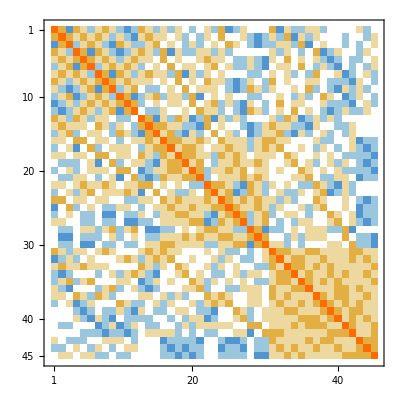

```mathematica
g7x1//MatrixPlot
```

```mathematica
myRowReduce[m_]:=Module[{r=RowReduce[Transpose[Join[Transpose[g7x1],IdentityMatrix[Length[m]]]]],l=Length[m[[1]]]},{r[[All,;;l]],r[[All,l+1;;]]}]
```

```mathematica
{rr,rm}=myRowReduce[g7x1];
```

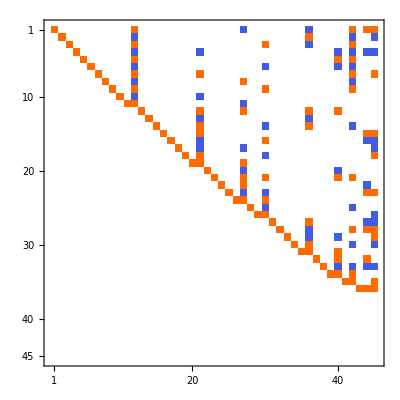

```mathematica
rr//MatrixPlot
```

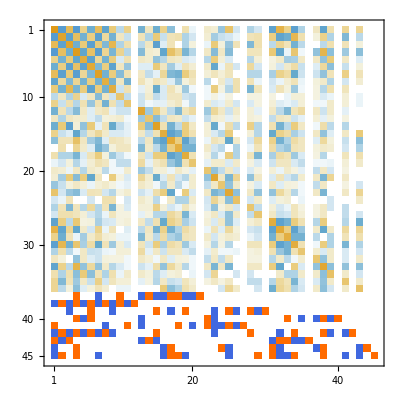

```mathematica
rm//MatrixPlot
```

```mathematica
c7nx1=Range[Length[c7x1]]~FE~("v"<>ToString[#]&)
```

{v1,v2,v3,v4,v5,v6,v7,v8,v9,v10,v11,v12,v13,v14,v15,v16,v17,v18,v19,v20,v21,v22,v23,v24,v25,v26,v27,v28,v29,v30,v31,v32,v33,v34,v35,v36,v37,v38,v39,v40,v41,v42,v43,v44,v45}

```mathematica
end={34,35,36,38,37,40,39,43,42,41,44,45};
perm=Join[Complement[Range[Length[c7x1]],end],end];
c7=c7x1[[perm]];
c7n=c7nx1[[perm]];g7=g7x1[[perm,perm]];
```

```mathematica
c7p={};
c7v={};
c7used={};
Print["from ",Length[c7]," vectors"];
For[i=1,i≤Length[c7],i++,
(*Print[c5p];*)
tmpused=Append[c7used,i];
If[Det[g7[[tmpused,tmpused]]]≠0,
c7used=tmpused;
AppendTo[c7p,Unique["p"]]
,
tmp=(Solve[g7[[c7used,tmpused]].Append[c7p,-1]==Array[0&,Length[c7used]],c7p][[1]]/.(a_->b_):>b);
AppendTo[c7v,tmp];
Print[i,") ",tmp.c7[[c7used]]==c7[[i]]]
]
];
Remove@@c7p;
Remove[c7p];
c7used
```

from 45 vectors

12) d[1,5] d[2,6] t[3,4,7]+d[1,6] d[2,4] t[3,5,7]-d[1,4] d[2,6] t[3,5,7]-d[1,5] d[2,4] t[3,6,7]+d[1,4] d[2,5] t[3,6,7]-d[1,6] d[2,3] t[4,5,7]+d[1,3] d[2,6] t[4,5,7]+d[1,5] d[2,3] t[4,6,7]-d[1,3] d[2,5] t[4,6,7]-d[1,4] d[2,3] t[5,6,7]+d[1,3] d[2,4] t[5,6,7]==d[1,6] d[2,5] t[3,4,7]

21) d[1,5] d[3,6] t[2,4,7]+d[1,6] d[3,4] t[2,5,7]-d[1,4] d[3,6] t[2,5,7]-d[1,5] d[3,4] t[2,6,7]+d[1,4] d[3,5] t[2,6,7]-d[1,6] d[2,3] t[4,5,7]+d[1,2] d[3,6] t[4,5,7]+d[1,5] d[2,3] t[4,6,7]-d[1,2] d[3,5] t[4,6,7]-d[1,4] d[2,3] t[5,6,7]+d[1,2] d[3,4] t[5,6,7]==d[1,6] d[3,5] t[2,4,7]

27) d[1,5] d[4,6] t[2,3,7]+d[1,6] d[3,4] t[2,5,7]-d[1,3] d[4,6] t[2,5,7]-d[1,5] d[3,4] t[2,6,7]+d[1,3] d[4,5] t[2,6,7]-d[1,6] d[2,4] t[3,5,7]+d[1,2] d[4,6] t[3,5,7]+d[1,5] d[2,4] t[3,6,7]-d[1,2] d[4,5] t[3,6,7]-d[1,3] d[2,4] t[5,6,7]+d[1,2] d[3,4] t[5,6,7]==d[1,6] d[4,5] t[2,3,7]

30) d[1,5] d[4,6] t[2,3,7]-d[1,5] d[3,6] t[2,4,7]+d[1,3] d[5,6] t[2,4,7]+d[1,4] d[3,6] t[2,5,7]-d[1,3] d[4,6] t[2,5,7]+d[1,5] d[2,6] t[3,4,7]-d[1,2] d[5,6] t[3,4,7]-d[1,4] d[2,6] t[3,5,7]+d[1,2] d[4,6] t[3,5,7]+d[1,3] d[2,6] t[4,5,7]-d[1,2] d[3,6] t[4,5,7]==d[1,4] d[5,6] t[2,3,7]

36) d[2,5] d[3,6] t[1,4,7]+d[2,6] d[3,4] t[1,5,7]-d[2,4] d[3,6] t[1,5,7]-d[2,5] d[3,4] t[1,6,7]+d[2,4] d[3,5] t[1,6,7]-d[1,3] d[2,6] t[4,5,7]+d[1,2] d[3,6] t[4,5,7]+d[1,3] d[2,5] t[4,6,7]-d[1,2] d[3,5] t[4,6,7]-d[1,3] d[2,4] t[5,6,7]+d[1,2] d[3,4] t[5,6,7]==d[2,6] d[3,5] t[1,4,7]

40) d[2,6] d[4,5] t[1,3,7]+d[2,6] d[3,4] t[1,5,7]+d[2,3] d[4,6] t[1,5,7]-d[2,5] d[3,4] t[1,6,7]-d[2,3] d[4,5] t[1,6,7]-d[1,4] d[2,6] t[3,5,7]+d[1,2] d[4,6] t[3,5,7]+d[1,4] d[2,5] t[3,6,7]-d[1,2] d[4,5] t[3,6,7]-d[1,4] d[2,3] t[5,6,7]+d[1,2] d[3,4] t[5,6,7]==d[2,5] d[4,6] t[1,3,7]

42) d[3,5] d[4,6] t[1,2,7]+d[2,6] d[4,5] t[1,3,7]-d[2,5] d[3,6] t[1,4,7]+d[2,4] d[3,6] t[1,5,7]-d[2,3] d[4,5] t[1,6,7]+d[1,5] d[2,6] t[3,4,7]-d[1,2] d[5,6] t[3,4,7]-d[1,4] d[2,6] t[3,5,7]+d[1,2] d[4,6] t[3,5,7]-d[1,5] d[2,4] t[3,6,7]+d[1,4] d[2,5] t[3,6,7]+d[1,3] d[2,6] t[4,5,7]-d[1,2] d[3,6] t[4,5,7]+d[1,5] d[2,3] t[4,6,7]-d[1,3] d[2,5] t[4,6,7]-d[1,4] d[2,3] t[5,6,7]+d[1,3] d[2,4] t[5,6,7]==d[2,4] d[5,6] t[1,3,7]

44) d[2,3] d[5,6] t[1,4,7]+d[2,4] d[3,6] t[1,5,7]+d[2,3] d[4,6] t[1,5,7]-d[2,4] d[3,5] t[1,6,7]-d[2,3] d[4,5] t[1,6,7]-d[1,4] d[3,6] t[2,5,7]+d[1,3] d[4,6] t[2,5,7]+d[1,4] d[3,5] t[2,6,7]-d[1,3] d[4,5] t[2,6,7]-d[1,4] d[2,3] t[5,6,7]+d[1,3] d[2,4] t[5,6,7]==d[3,6] d[4,5] t[1,2,7]

45) d[3,5] d[4,6] t[1,2,7]-d[2,5] d[3,6] t[1,4,7]+d[2,3] d[5,6] t[1,4,7]+d[2,4] d[3,6] t[1,5,7]+d[2,5] d[3,4] t[1,6,7]-d[2,4] d[3,5] t[1,6,7]-d[2,3] d[4,5] t[1,6,7]+d[1,5] d[3,6] t[2,4,7]-d[1,3] d[5,6] t[2,4,7]-d[1,4] d[3,6] t[2,5,7]+d[1,3] d[4,6] t[2,5,7]-d[1,5] d[3,4] t[2,6,7]+d[1,4] d[3,5] t[2,6,7]+d[1,5] d[2,3] t[4,6,7]-d[1,3] d[2,5] t[4,6,7]-d[1,4] d[2,3] t[5,6,7]+d[1,3] d[2,4] t[5,6,7]==d[3,4] d[5,6] t[1,2,7]

{1,2,3,4,5,6,7,8,9,10,11,13,14,15,16,17,18,19,20,22,23,24,25,26,28,29,31,32,33,34,35,37,38,39,41,43}

```mathematica
c7v//TableForm
```

1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
0 | 0 | 0 | -1 | 0 | 0 | 1 | 0 | 0 | -1 | 0 | 1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | -1 | 0 | 1 | -1 | 1 | 1 | -1 | 1 |  |  |  |  |  |  |  |  |  |  |  | 
0 | 0 | 1 | 0 | 0 | -1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | -1 | 0 | 1 | 0 | -1 | 0 | 0 | 1 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 1 |  |  |  | 
1 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 1 | -1 | 0 | 0 | 0 | 0 | 1 |  |  | 
0 | 0 | 0 | 1 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | -1 | 1 | 0 | 0 | 0 | 1 |  | 
0 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | -1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | -1 | 0 | 1
1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | -1 | 1 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | -1 | -1 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 1 | 0 | 1 | 1 | -1 | -1 | 1 | 0 | -1 | 0 | 0 | 1 | 0 | -1 | 0 | 0 | 1 | 1 | -1 | 1 | -1 | 0 | -1 | 1 | 1

## 7 spins auto check

```mathematica
c7=listKPTs[2,7];
```

```mathematica
c7//Length
```

105

```mathematica
deps7=depsGen[7,c7];
```

return

```mathematica
{deps7//Length,deps7[[1]]//Length}
```

{84,105}

```mathematica
Timing[deps7a=RowReduceUpTo[deps7,Length[deps7[[1]]]]][[1]]/60
```

0.00312

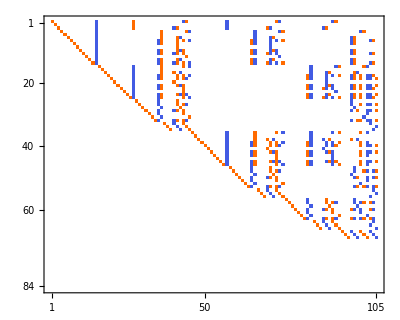

```mathematica
deps7a//MatrixPlot
```

```mathematica
deps7b=deps7a//DeleteReduced;
```

```mathematica
n=69;
deps7a[[n]]==deps7b[[n]]
```

True

```mathematica
deps7a[[70]]
```

SparseArray[<0>, {105}]

```mathematica
{deps7a//Length,deps7a[[1]]//Length}
```

{84,105}

```mathematica
deps7a//LinDependent
```

{15,27,35,36,40,41,42,43,44,45,57,65,66,70,71,72,73,74,75,83,84,88,89,90,91,92,93,97,98,99,100,101,102,103,104,105}

```mathematica
deps7b//LinDependent
```

{15,27,35,36,40,41,42,43,44,45,57,65,66,70,71,72,73,74,75,83,84,88,89,90,91,92,93,97,98,99,100,101,102,103,104,105}

```mathematica
c7i=c7[[deps7a//LinDependent]]
```

{d[3,4] d[5,6] t[1,2,7],d[2,4] d[5,6] t[1,3,7],d[2,6] d[3,5] t[1,4,7],d[2,3] d[5,6] t[1,4,7],d[2,4] d[3,6] t[1,5,7],d[2,6] d[3,4] t[1,5,7],d[2,3] d[4,6] t[1,5,7],d[2,4] d[3,5] t[1,6,7],d[2,5] d[3,4] t[1,6,7],d[2,3] d[4,5] t[1,6,7],d[1,4] d[5,6] t[2,3,7],d[1,6] d[3,5] t[2,4,7],d[1,3] d[5,6] t[2,4,7],d[1,4] d[3,6] t[2,5,7],d[1,6] d[3,4] t[2,5,7],d[1,3] d[4,6] t[2,5,7],d[1,4] d[3,5] t[2,6,7],d[1,5] d[3,4] t[2,6,7],d[1,3] d[4,5] t[2,6,7],d[1,6] d[2,5] t[3,4,7],d[1,2] d[5,6] t[3,4,7],d[1,4] d[2,6] t[3,5,7],d[1,6] d[2,4] t[3,5,7],d[1,2] d[4,6] t[3,5,7],d[1,4] d[2,5] t[3,6,7],d[1,5] d[2,4] t[3,6,7],d[1,2] d[4,5] t[3,6,7],d[1,3] d[2,6] t[4,5,7],d[1,6] d[2,3] t[4,5,7],d[1,2] d[3,6] t[4,5,7],d[1,3] d[2,5] t[4,6,7],d[1,5] d[2,3] t[4,6,7],d[1,2] d[3,5] t[4,6,7],d[1,3] d[2,4] t[5,6,7],d[1,4] d[2,3] t[5,6,7],d[1,2] d[3,4] t[5,6,7]}

```mathematica
c7i//Length
```

36

```mathematica
g7i=symGramMatrix[c7i];
```

```mathematica
LinDeps[g7i]~FE~(#.c7i&)
```

{}

```mathematica
MatrixRank[g7i]
```

36

```mathematica
g7=symGramMatrix[c7];
```

```mathematica
MatrixRank[g7]
```

36

## 8 spins auto

```mathematica
c7x1=listKPs[4,8]~FE~KPToExpr
```

{d[1,5] d[2,6] d[3,7] d[4,8],d[1,5] d[2,6] d[3,8] d[4,7],d[1,5] d[2,7] d[3,6] d[4,8],d[1,5] d[2,7] d[3,8] d[4,6],d[1,5] d[2,8] d[3,6] d[4,7],d[1,5] d[2,8] d[3,7] d[4,6],d[1,6] d[2,5] d[3,7] d[4,8],d[1,6] d[2,5] d[3,8] d[4,7],d[1,6] d[2,7] d[3,5] d[4,8],d[1,6] d[2,7] d[3,8] d[4,5],d[1,6] d[2,8] d[3,5] d[4,7],d[1,6] d[2,8] d[3,7] d[4,5],d[1,7] d[2,5] d[3,6] d[4,8],d[1,7] d[2,5] d[3,8] d[4,6],d[1,7] d[2,6] d[3,5] d[4,8],d[1,7] d[2,6] d[3,8] d[4,5],d[1,7] d[2,8] d[3,5] d[4,6],d[1,7] d[2,8] d[3,6] d[4,5],d[1,8] d[2,5] d[3,6] d[4,7],d[1,8] d[2,5] d[3,7] d[4,6],d[1,8] d[2,6] d[3,5] d[4,7],d[1,8] d[2,6] d[3,7] d[4,5],d[1,8] d[2,7] d[3,5] d[4,6],d[1,8] d[2,7] d[3,6] d[4,5],d[1,4] d[2,6] d[3,7] d[5,8],d[1,4] d[2,6] d[3,8] d[5,7],d[1,4] d[2,7] d[3,6] d[5,8],d[1,4] d[2,7] d[3,8] d[5,6],d[1,4] d[2,8] d[3,6] d[5,7],d[1,4] d[2,8] d[3,7] d[5,6],d[1,6] d[2,4] d[3,7] d[5,8],d[1,6] d[2,4] d[3,8] d[5,7],d[1,6] d[2,7] d[3,4] d[5,8],d[1,6] d[2,8] d[3,4] d[5,7],d[1,7] d[2,4] d[3,6] d[5,8],d[1,7] d[2,4] d[3,8] d[5,6],d[1,7] d[2,6] d[3,4] d[5,8],d[1,7] d[2,8] d[3,4] d[5,6],d[1,8] d[2,4] d[3,6] d[5,7],d[1,8] d[2,4] d[3,7] d[5,6],d[1,8] d[2,6] d[3,4] d[5,7],d[1,8] d[2,7] d[3,4] d[5,6],d[1,4] d[2,5] d[3,7] d[6,8],d[1,4] d[2,5] d[3,8] d[6,7],d[1,4] d[2,7] d[3,5] d[6,8],d[1,4] d[2,8] d[3,5] d[6,7],d[1,5] d[2,4] d[3,7] d[6,8],d[1,5] d[2,4] d[3,8] d[6,7],d[1,5] d[2,7] d[3,4] d[6,8],d[1,5] d[2,8] d[3,4] d[6,7],d[1,7] d[2,4] d[3,5] d[6,8],d[1,7] d[2,5] d[3,4] d[6,8],d[1,8] d[2,4] d[3,5] d[6,7],d[1,8] d[2,5] d[3,4] d[6,7],d[1,4] d[2,5] d[3,6] d[7,8],d[1,4] d[2,6] d[3,5] d[7,8],d[1,5] d[2,4] d[3,6] d[7,8],d[1,5] d[2,6] d[3,4] d[7,8],d[1,6] d[2,4] d[3,5] d[7,8],d[1,6] d[2,5] d[3,4] d[7,8],d[1,3] d[2,6] d[4,7] d[5,8],d[1,3] d[2,6] d[4,8] d[5,7],d[1,3] d[2,7] d[4,6] d[5,8],d[1,3] d[2,7] d[4,8] d[5,6],d[1,3] d[2,8] d[4,6] d[5,7],d[1,3] d[2,8] d[4,7] d[5,6],d[1,6] d[2,3] d[4,7] d[5,8],d[1,6] d[2,3] d[4,8] d[5,7],d[1,7] d[2,3] d[4,6] d[5,8],d[1,7] d[2,3] d[4,8] d[5,6],d[1,8] d[2,3] d[4,6] d[5,7],d[1,8] d[2,3] d[4,7] d[5,6],d[1,3] d[2,5] d[4,7] d[6,8],d[1,3] d[2,5] d[4,8] d[6,7],d[1,3] d[2,7] d[4,5] d[6,8],d[1,3] d[2,8] d[4,5] d[6,7],d[1,5] d[2,3] d[4,7] d[6,8],d[1,5] d[2,3] d[4,8] d[6,7],d[1,7] d[2,3] d[4,5] d[6,8],d[1,8] d[2,3] d[4,5] d[6,7],d[1,3] d[2,5] d[4,6] d[7,8],d[1,3] d[2,6] d[4,5] d[7,8],d[1,5] d[2,3] d[4,6] d[7,8],d[1,6] d[2,3] d[4,5] d[7,8],d[1,3] d[2,4] d[5,7] d[6,8],d[1,3] d[2,4] d[5,8] d[6,7],d[1,4] d[2,3] d[5,7] d[6,8],d[1,4] d[2,3] d[5,8] d[6,7],d[1,3] d[2,4] d[5,6] d[7,8],d[1,4] d[2,3] d[5,6] d[7,8],d[1,2] d[3,6] d[4,7] d[5,8],d[1,2] d[3,6] d[4,8] d[5,7],d[1,2] d[3,7] d[4,6] d[5,8],d[1,2] d[3,7] d[4,8] d[5,6],d[1,2] d[3,8] d[4,6] d[5,7],d[1,2] d[3,8] d[4,7] d[5,6],d[1,2] d[3,5] d[4,7] d[6,8],d[1,2] d[3,5] d[4,8] d[6,7],d[1,2] d[3,7] d[4,5] d[6,8],d[1,2] d[3,8] d[4,5] d[6,7],d[1,2] d[3,5] d[4,6] d[7,8],d[1,2] d[3,6] d[4,5] d[7,8],d[1,2] d[3,4] d[5,7] d[6,8],d[1,2] d[3,4] d[5,8] d[6,7],d[1,2] d[3,4] d[5,6] d[7,8]}

```mathematica
c7x2=c7x1[[Join[{24,60,88,96},Complement[Range[Length[c7x1]],{24,60,88,96}]]]];
```

```mathematica
c7x3=c7x2[[Join[{27,45,62,86,89,91,96,100},Complement[Range[Length[c7x2]],{27,45,62,86,89,91,96,100}]]]];
```

```mathematica
c7x4=c7x3[[Join[{34,63,67,92,93,97,102,104},Complement[Range[Length[c7x3]],{34,63,67,92,93,97,102,104}]]]];
```

```mathematica
c7x5=c7x4[[Join[{41,58,69,72,96,99,102,104},Complement[Range[Length[c7x4]],{41,58,69,72,96,99,102,104}]]]];
```

```mathematica
c7x6=c7x5[[Join[{48,64,76,88,92,94,101},Complement[Range[Length[c7x5]],{48,64,76,88,92,94,101}]]]];
```

```mathematica
c7x7=c7x6[[Join[{54,69,79,91,94,95,101},Complement[Range[Length[c7x6]],{54,69,79,91,94,95,101}]]]];
```

```mathematica
c7x8=c7x7[[Join[{60,84,89,94,96,98,103},Complement[Range[105],{60,84,89,94,96,98,103}]]]];
```

```mathematica
c7=c7x1;
```

```mathematica
g7=Monitor[Array[(l=#1;fastTr1[c7[[#1]],c7[[#2]]])&,{c7//Length,c7//Length}],ProgressIndicator[l/Length[c7]]]
```

{{81,27,27,9,9,27,27,9,9,3,3,9,9,3,27,9,9,3,3,9,9,27,3,9,27,9,9,3,3,9,9,3,3,3,3,3,9,3,3,9,9,3,9,3,3,3,27,9,9,9,9,3,3,3,3,9,9,27,3,9,9,27,3,9,9,3,3,9,3,9,3,3,3,9,3,3,9,27,3,9,3,9,9,3,9,3,3,9,3,3,3,9,9,27,3,9,3,9,9,3,3,3,3,3,9},103,{9,9,3,3,3,3,9,9,3,3,3,3,3,3,3,3,9,9,3,3,3,3,9,9,3,3,3,9,3,9,3,3,9,9,3,9,9,27,3,9,9,27,3,3,3,3,3,3,9,9,3,9,3,9,9,9,9,27,9,27,3,3,3,9,3,9,3,3,3,9,3,9,3,3,3,3,3,3,3,3,9,9,9,9,9,9,9,9,27,27,9,9,9,27,9,27,9,9,9,9,27,27,27,27,81}}
 |  |  |  |

```mathematica
c7p={};
c7used={};
Print["from ",Length[c7]," vectors"];
For[i=1,i≤Length[c7],i++,
(*Print[c5p];*)
tmpused=Append[c7used,i];
If[Det[g7[[tmpused,tmpused]]]≠0,
c7used=tmpused;
AppendTo[c7p,Unique["p"]]
,
Print[i,") ",(Solve[g7[[c7used,tmpused]].Append[c7p,-1]==Array[0&,Length[c7used]],c7p][[1]]/.(a_->b_):>b).c7[[c7used]]==c7[[i]]]
]
];
Remove@@c7p;
Remove[c7p];
c7[[c7used]]
```

from 105 vectors

24) d[1,7] d[2,8] d[3,6] d[4,5]+d[1,8] d[2,6] d[3,7] d[4,5]-d[1,6] d[2,8] d[3,7] d[4,5]-d[1,7] d[2,6] d[3,8] d[4,5]+d[1,6] d[2,7] d[3,8] d[4,5]+d[1,8] d[2,7] d[3,5] d[4,6]-d[1,7] d[2,8] d[3,5] d[4,6]-d[1,8] d[2,5] d[3,7] d[4,6]+d[1,5] d[2,8] d[3,7] d[4,6]+d[1,7] d[2,5] d[3,8] d[4,6]-d[1,5] d[2,7] d[3,8] d[4,6]-d[1,8] d[2,6] d[3,5] d[4,7]+d[1,6] d[2,8] d[3,5] d[4,7]+d[1,8] d[2,5] d[3,6] d[4,7]-d[1,5] d[2,8] d[3,6] d[4,7]-d[1,6] d[2,5] d[3,8] d[4,7]+d[1,5] d[2,6] d[3,8] d[4,7]+d[1,7] d[2,6] d[3,5] d[4,8]-d[1,6] d[2,7] d[3,5] d[4,8]-d[1,7] d[2,5] d[3,6] d[4,8]+d[1,5] d[2,7] d[3,6] d[4,8]+d[1,6] d[2,5] d[3,7] d[4,8]-d[1,5] d[2,6] d[3,7] d[4,8]==d[1,8] d[2,7] d[3,6] d[4,5]

42) d[1,8] d[2,7] d[3,5] d[4,6]-d[1,7] d[2,8] d[3,5] d[4,6]-d[1,8] d[2,5] d[3,7] d[4,6]+d[1,5] d[2,8] d[3,7] d[4,6]+d[1,7] d[2,5] d[3,8] d[4,6]-d[1,5] d[2,7] d[3,8] d[4,6]-d[1,8] d[2,6] d[3,5] d[4,7]+d[1,6] d[2,8] d[3,5] d[4,7]+d[1,8] d[2,5] d[3,6] d[4,7]-d[1,5] d[2,8] d[3,6] d[4,7]-d[1,6] d[2,5] d[3,8] d[4,7]+d[1,5] d[2,6] d[3,8] d[4,7]+d[1,7] d[2,6] d[3,5] d[4,8]-d[1,6] d[2,7] d[3,5] d[4,8]-d[1,7] d[2,5] d[3,6] d[4,8]+d[1,5] d[2,7] d[3,6] d[4,8]+d[1,6] d[2,5] d[3,7] d[4,8]-d[1,5] d[2,6] d[3,7] d[4,8]+d[1,7] d[2,8] d[3,4] d[5,6]+d[1,8] d[2,4] d[3,7] d[5,6]-d[1,4] d[2,8] d[3,7] d[5,6]-d[1,7] d[2,4] d[3,8] d[5,6]+d[1,4] d[2,7] d[3,8] d[5,6]+d[1,8] d[2,6] d[3,4] d[5,7]-d[1,6] d[2,8] d[3,4] d[5,7]-d[1,8] d[2,4] d[3,6] d[5,7]+d[1,4] d[2,8] d[3,6] d[5,7]+d[1,6] d[2,4] d[3,8] d[5,7]-d[1,4] d[2,6] d[3,8] d[5,7]-d[1,7] d[2,6] d[3,4] d[5,8]+d[1,6] d[2,7] d[3,4] d[5,8]+d[1,7] d[2,4] d[3,6] d[5,8]-d[1,4] d[2,7] d[3,6] d[5,8]-d[1,6] d[2,4] d[3,7] d[5,8]+d[1,4] d[2,6] d[3,7] d[5,8]==d[1,8] d[2,7] d[3,4] d[5,6]

54) -d[1,8] d[2,6] d[3,5] d[4,7]+d[1,6] d[2,8] d[3,5] d[4,7]+d[1,8] d[2,5] d[3,6] d[4,7]-d[1,5] d[2,8] d[3,6] d[4,7]-d[1,6] d[2,5] d[3,8] d[4,7]+d[1,5] d[2,6] d[3,8] d[4,7]+d[1,7] d[2,6] d[3,5] d[4,8]-d[1,6] d[2,7] d[3,5] d[4,8]-d[1,7] d[2,5] d[3,6] d[4,8]+d[1,5] d[2,7] d[3,6] d[4,8]+d[1,6] d[2,5] d[3,7] d[4,8]-d[1,5] d[2,6] d[3,7] d[4,8]+d[1,8] d[2,6] d[3,4] d[5,7]-d[1,6] d[2,8] d[3,4] d[5,7]-d[1,8] d[2,4] d[3,6] d[5,7]+d[1,4] d[2,8] d[3,6] d[5,7]+d[1,6] d[2,4] d[3,8] d[5,7]-d[1,4] d[2,6] d[3,8] d[5,7]-d[1,7] d[2,6] d[3,4] d[5,8]+d[1,6] d[2,7] d[3,4] d[5,8]+d[1,7] d[2,4] d[3,6] d[5,8]-d[1,4] d[2,7] d[3,6] d[5,8]-d[1,6] d[2,4] d[3,7] d[5,8]+d[1,4] d[2,6] d[3,7] d[5,8]+d[1,5] d[2,8] d[3,4] d[6,7]+d[1,8] d[2,4] d[3,5] d[6,7]-d[1,4] d[2,8] d[3,5] d[6,7]-d[1,5] d[2,4] d[3,8] d[6,7]+d[1,4] d[2,5] d[3,8] d[6,7]+d[1,7] d[2,5] d[3,4] d[6,8]-d[1,5] d[2,7] d[3,4] d[6,8]-d[1,7] d[2,4] d[3,5] d[6,8]+d[1,4] d[2,7] d[3,5] d[6,8]+d[1,5] d[2,4] d[3,7] d[6,8]-d[1,4] d[2,5] d[3,7] d[6,8]==d[1,8] d[2,5] d[3,4] d[6,7]

60) d[1,7] d[2,6] d[3,5] d[4,8]-d[1,6] d[2,7] d[3,5] d[4,8]-d[1,7] d[2,5] d[3,6] d[4,8]+d[1,5] d[2,7] d[3,6] d[4,8]+d[1,6] d[2,5] d[3,7] d[4,8]-d[1,5] d[2,6] d[3,7] d[4,8]-d[1,7] d[2,6] d[3,4] d[5,8]+d[1,6] d[2,7] d[3,4] d[5,8]+d[1,7] d[2,4] d[3,6] d[5,8]-d[1,4] d[2,7] d[3,6] d[5,8]-d[1,6] d[2,4] d[3,7] d[5,8]+d[1,4] d[2,6] d[3,7] d[5,8]+d[1,7] d[2,5] d[3,4] d[6,8]-d[1,5] d[2,7] d[3,4] d[6,8]-d[1,7] d[2,4] d[3,5] d[6,8]+d[1,4] d[2,7] d[3,5] d[6,8]+d[1,5] d[2,4] d[3,7] d[6,8]-d[1,4] d[2,5] d[3,7] d[6,8]+d[1,5] d[2,6] d[3,4] d[7,8]+d[1,6] d[2,4] d[3,5] d[7,8]-d[1,4] d[2,6] d[3,5] d[7,8]-d[1,5] d[2,4] d[3,6] d[7,8]+d[1,4] d[2,5] d[3,6] d[7,8]==d[1,6] d[2,5] d[3,4] d[7,8]

72) -d[1,8] d[2,5] d[3,7] d[4,6]+d[1,5] d[2,8] d[3,7] d[4,6]+d[1,7] d[2,5] d[3,8] d[4,6]-d[1,5] d[2,7] d[3,8] d[4,6]+d[1,8] d[2,5] d[3,6] d[4,7]-d[1,5] d[2,8] d[3,6] d[4,7]-d[1,6] d[2,5] d[3,8] d[4,7]+d[1,5] d[2,6] d[3,8] d[4,7]-d[1,7] d[2,5] d[3,6] d[4,8]+d[1,5] d[2,7] d[3,6] d[4,8]+d[1,6] d[2,5] d[3,7] d[4,8]-d[1,5] d[2,6] d[3,7] d[4,8]+d[1,8] d[2,4] d[3,7] d[5,6]-d[1,4] d[2,8] d[3,7] d[5,6]-d[1,7] d[2,4] d[3,8] d[5,6]+d[1,4] d[2,7] d[3,8] d[5,6]+d[1,3] d[2,8] d[4,7] d[5,6]+d[1,7] d[2,3] d[4,8] d[5,6]-d[1,3] d[2,7] d[4,8] d[5,6]-d[1,8] d[2,4] d[3,6] d[5,7]+d[1,4] d[2,8] d[3,6] d[5,7]+d[1,6] d[2,4] d[3,8] d[5,7]-d[1,4] d[2,6] d[3,8] d[5,7]+d[1,8] d[2,3] d[4,6] d[5,7]-d[1,3] d[2,8] d[4,6] d[5,7]-d[1,6] d[2,3] d[4,8] d[5,7]+d[1,3] d[2,6] d[4,8] d[5,7]+d[1,7] d[2,4] d[3,6] d[5,8]-d[1,4] d[2,7] d[3,6] d[5,8]-d[1,6] d[2,4] d[3,7] d[5,8]+d[1,4] d[2,6] d[3,7] d[5,8]-d[1,7] d[2,3] d[4,6] d[5,8]+d[1,3] d[2,7] d[4,6] d[5,8]+d[1,6] d[2,3] d[4,7] d[5,8]-d[1,3] d[2,6] d[4,7] d[5,8]==d[1,8] d[2,3] d[4,7] d[5,6]

80) d[1,8] d[2,6] d[3,7] d[4,5]-d[1,6] d[2,8] d[3,7] d[4,5]-d[1,7] d[2,6] d[3,8] d[4,5]+d[1,6] d[2,7] d[3,8] d[4,5]-d[1,8] d[2,5] d[3,7] d[4,6]+d[1,5] d[2,8] d[3,7] d[4,6]+d[1,7] d[2,5] d[3,8] d[4,6]-d[1,5] d[2,7] d[3,8] d[4,6]-d[1,8] d[2,6] d[3,5] d[4,7]+d[1,6] d[2,8] d[3,5] d[4,7]+d[1,8] d[2,5] d[3,6] d[4,7]-d[1,5] d[2,8] d[3,6] d[4,7]-2 d[1,6] d[2,5] d[3,8] d[4,7]+2 d[1,5] d[2,6] d[3,8] d[4,7]+d[1,7] d[2,6] d[3,5] d[4,8]-d[1,6] d[2,7] d[3,5] d[4,8]-d[1,7] d[2,5] d[3,6] d[4,8]+d[1,5] d[2,7] d[3,6] d[4,8]+2 d[1,6] d[2,5] d[3,7] d[4,8]-2 d[1,5] d[2,6] d[3,7] d[4,8]-d[1,8] d[2,4] d[3,6] d[5,7]+d[1,4] d[2,8] d[3,6] d[5,7]+d[1,6] d[2,4] d[3,8] d[5,7]-d[1,4] d[2,6] d[3,8] d[5,7]+d[1,8] d[2,3] d[4,6] d[5,7]-d[1,3] d[2,8] d[4,6] d[5,7]-d[1,6] d[2,3] d[4,8] d[5,7]+d[1,3] d[2,6] d[4,8] d[5,7]+d[1,7] d[2,4] d[3,6] d[5,8]-d[1,4] d[2,7] d[3,6] d[5,8]-d[1,6] d[2,4] d[3,7] d[5,8]+d[1,4] d[2,6] d[3,7] d[5,8]-d[1,7] d[2,3] d[4,6] d[5,8]+d[1,3] d[2,7] d[4,6] d[5,8]+d[1,6] d[2,3] d[4,7] d[5,8]-d[1,3] d[2,6] d[4,7] d[5,8]+d[1,8] d[2,4] d[3,5] d[6,7]-d[1,4] d[2,8] d[3,5] d[6,7]-d[1,5] d[2,4] d[3,8] d[6,7]+d[1,4] d[2,5] d[3,8] d[6,7]+d[1,3] d[2,8] d[4,5] d[6,7]+d[1,5] d[2,3] d[4,8] d[6,7]-d[1,3] d[2,5] d[4,8] d[6,7]-d[1,7] d[2,4] d[3,5] d[6,8]+d[1,4] d[2,7] d[3,5] d[6,8]+d[1,5] d[2,4] d[3,7] d[6,8]-d[1,4] d[2,5] d[3,7] d[6,8]+d[1,7] d[2,3] d[4,5] d[6,8]-d[1,3] d[2,7] d[4,5] d[6,8]-d[1,5] d[2,3] d[4,7] d[6,8]+d[1,3] d[2,5] d[4,7] d[6,8]==d[1,8] d[2,3] d[4,5] d[6,7]

84) -d[1,7] d[2,6] d[3,8] d[4,5]+d[1,6] d[2,7] d[3,8] d[4,5]+d[1,7] d[2,5] d[3,8] d[4,6]-d[1,5] d[2,7] d[3,8] d[4,6]-d[1,6] d[2,5] d[3,8] d[4,7]+d[1,5] d[2,6] d[3,8] d[4,7]+d[1,7] d[2,6] d[3,5] d[4,8]-d[1,6] d[2,7] d[3,5] d[4,8]-d[1,7] d[2,5] d[3,6] d[4,8]+d[1,5] d[2,7] d[3,6] d[4,8]+d[1,6] d[2,5] d[3,7] d[4,8]-d[1,5] d[2,6] d[3,7] d[4,8]+d[1,7] d[2,4] d[3,6] d[5,8]-d[1,4] d[2,7] d[3,6] d[5,8]-d[1,6] d[2,4] d[3,7] d[5,8]+d[1,4] d[2,6] d[3,7] d[5,8]-d[1,7] d[2,3] d[4,6] d[5,8]+d[1,3] d[2,7] d[4,6] d[5,8]+d[1,6] d[2,3] d[4,7] d[5,8]-d[1,3] d[2,6] d[4,7] d[5,8]-d[1,7] d[2,4] d[3,5] d[6,8]+d[1,4] d[2,7] d[3,5] d[6,8]+d[1,5] d[2,4] d[3,7] d[6,8]-d[1,4] d[2,5] d[3,7] d[6,8]+d[1,7] d[2,3] d[4,5] d[6,8]-d[1,3] d[2,7] d[4,5] d[6,8]-d[1,5] d[2,3] d[4,7] d[6,8]+d[1,3] d[2,5] d[4,7] d[6,8]+d[1,6] d[2,4] d[3,5] d[7,8]-d[1,4] d[2,6] d[3,5] d[7,8]-d[1,5] d[2,4] d[3,6] d[7,8]+d[1,4] d[2,5] d[3,6] d[7,8]+d[1,3] d[2,6] d[4,5] d[7,8]+d[1,5] d[2,3] d[4,6] d[7,8]-d[1,3] d[2,5] d[4,6] d[7,8]==d[1,6] d[2,3] d[4,5] d[7,8]

88) -d[1,6] d[2,5] d[3,8] d[4,7]+d[1,5] d[2,6] d[3,8] d[4,7]+d[1,6] d[2,5] d[3,7] d[4,8]-d[1,5] d[2,6] d[3,7] d[4,8]+d[1,6] d[2,4] d[3,8] d[5,7]-d[1,4] d[2,6] d[3,8] d[5,7]-d[1,6] d[2,3] d[4,8] d[5,7]+d[1,3] d[2,6] d[4,8] d[5,7]-d[1,6] d[2,4] d[3,7] d[5,8]+d[1,4] d[2,6] d[3,7] d[5,8]+d[1,6] d[2,3] d[4,7] d[5,8]-d[1,3] d[2,6] d[4,7] d[5,8]-d[1,5] d[2,4] d[3,8] d[6,7]+d[1,4] d[2,5] d[3,8] d[6,7]+d[1,5] d[2,3] d[4,8] d[6,7]-d[1,3] d[2,5] d[4,8] d[6,7]+d[1,3] d[2,4] d[5,8] d[6,7]+d[1,5] d[2,4] d[3,7] d[6,8]-d[1,4] d[2,5] d[3,7] d[6,8]-d[1,5] d[2,3] d[4,7] d[6,8]+d[1,3] d[2,5] d[4,7] d[6,8]+d[1,4] d[2,3] d[5,7] d[6,8]-d[1,3] d[2,4] d[5,7] d[6,8]==d[1,4] d[2,3] d[5,8] d[6,7]

90) d[1,7] d[2,5] d[3,8] d[4,6]-d[1,5] d[2,7] d[3,8] d[4,6]-d[1,6] d[2,5] d[3,8] d[4,7]+d[1,5] d[2,6] d[3,8] d[4,7]-d[1,7] d[2,5] d[3,6] d[4,8]+d[1,5] d[2,7] d[3,6] d[4,8]+d[1,6] d[2,5] d[3,7] d[4,8]-d[1,5] d[2,6] d[3,7] d[4,8]-d[1,7] d[2,4] d[3,8] d[5,6]+d[1,4] d[2,7] d[3,8] d[5,6]+d[1,7] d[2,3] d[4,8] d[5,6]-d[1,3] d[2,7] d[4,8] d[5,6]+d[1,6] d[2,4] d[3,8] d[5,7]-d[1,4] d[2,6] d[3,8] d[5,7]-d[1,6] d[2,3] d[4,8] d[5,7]+d[1,3] d[2,6] d[4,8] d[5,7]+d[1,7] d[2,4] d[3,6] d[5,8]-d[1,4] d[2,7] d[3,6] d[5,8]-d[1,6] d[2,4] d[3,7] d[5,8]+d[1,4] d[2,6] d[3,7] d[5,8]-d[1,7] d[2,3] d[4,6] d[5,8]+d[1,3] d[2,7] d[4,6] d[5,8]+d[1,6] d[2,3] d[4,7] d[5,8]-d[1,3] d[2,6] d[4,7] d[5,8]+d[1,5] d[2,4] d[3,7] d[6,8]-d[1,4] d[2,5] d[3,7] d[6,8]-d[1,5] d[2,3] d[4,7] d[6,8]+d[1,3] d[2,5] d[4,7] d[6,8]+d[1,4] d[2,3] d[5,7] d[6,8]-d[1,3] d[2,4] d[5,7] d[6,8]-d[1,5] d[2,4] d[3,6] d[7,8]+d[1,4] d[2,5] d[3,6] d[7,8]+d[1,5] d[2,3] d[4,6] d[7,8]-d[1,3] d[2,5] d[4,6] d[7,8]+d[1,3] d[2,4] d[5,6] d[7,8]==d[1,4] d[2,3] d[5,6] d[7,8]

96) d[1,5] d[2,8] d[3,7] d[4,6]-d[1,5] d[2,7] d[3,8] d[4,6]-d[1,5] d[2,8] d[3,6] d[4,7]+d[1,5] d[2,6] d[3,8] d[4,7]+d[1,5] d[2,7] d[3,6] d[4,8]-d[1,5] d[2,6] d[3,7] d[4,8]-d[1,4] d[2,8] d[3,7] d[5,6]+d[1,4] d[2,7] d[3,8] d[5,6]+d[1,3] d[2,8] d[4,7] d[5,6]-d[1,3] d[2,7] d[4,8] d[5,6]+d[1,2] d[3,7] d[4,8] d[5,6]+d[1,4] d[2,8] d[3,6] d[5,7]-d[1,4] d[2,6] d[3,8] d[5,7]-d[1,3] d[2,8] d[4,6] d[5,7]+d[1,2] d[3,8] d[4,6] d[5,7]+d[1,3] d[2,6] d[4,8] d[5,7]-d[1,2] d[3,6] d[4,8] d[5,7]-d[1,4] d[2,7] d[3,6] d[5,8]+d[1,4] d[2,6] d[3,7] d[5,8]+d[1,3] d[2,7] d[4,6] d[5,8]-d[1,2] d[3,7] d[4,6] d[5,8]-d[1,3] d[2,6] d[4,7] d[5,8]+d[1,2] d[3,6] d[4,7] d[5,8]==d[1,2] d[3,8] d[4,7] d[5,6]

100) -d[1,6] d[2,8] d[3,7] d[4,5]+d[1,6] d[2,7] d[3,8] d[4,5]+d[1,5] d[2,8] d[3,7] d[4,6]-d[1,5] d[2,7] d[3,8] d[4,6]+d[1,6] d[2,8] d[3,5] d[4,7]-d[1,5] d[2,8] d[3,6] d[4,7]-d[1,6] d[2,5] d[3,8] d[4,7]+d[1,5] d[2,6] d[3,8] d[4,7]-d[1,6] d[2,7] d[3,5] d[4,8]+d[1,5] d[2,7] d[3,6] d[4,8]+d[1,6] d[2,5] d[3,7] d[4,8]-d[1,5] d[2,6] d[3,7] d[4,8]+d[1,4] d[2,8] d[3,6] d[5,7]-d[1,4] d[2,6] d[3,8] d[5,7]-d[1,3] d[2,8] d[4,6] d[5,7]+d[1,2] d[3,8] d[4,6] d[5,7]+d[1,3] d[2,6] d[4,8] d[5,7]-d[1,2] d[3,6] d[4,8] d[5,7]-d[1,4] d[2,7] d[3,6] d[5,8]+d[1,4] d[2,6] d[3,7] d[5,8]+d[1,3] d[2,7] d[4,6] d[5,8]-d[1,2] d[3,7] d[4,6] d[5,8]-d[1,3] d[2,6] d[4,7] d[5,8]+d[1,2] d[3,6] d[4,7] d[5,8]-d[1,4] d[2,8] d[3,5] d[6,7]+d[1,4] d[2,5] d[3,8] d[6,7]+d[1,3] d[2,8] d[4,5] d[6,7]-d[1,3] d[2,5] d[4,8] d[6,7]+d[1,2] d[3,5] d[4,8] d[6,7]+d[1,4] d[2,7] d[3,5] d[6,8]-d[1,4] d[2,5] d[3,7] d[6,8]-d[1,3] d[2,7] d[4,5] d[6,8]+d[1,2] d[3,7] d[4,5] d[6,8]+d[1,3] d[2,5] d[4,7] d[6,8]-d[1,2] d[3,5] d[4,7] d[6,8]==d[1,2] d[3,8] d[4,5] d[6,7]

102) d[1,7] d[2,8] d[3,6] d[4,5]-d[1,6] d[2,8] d[3,7] d[4,5]-d[1,7] d[2,6] d[3,8] d[4,5]+d[1,6] d[2,7] d[3,8] d[4,5]-d[1,7] d[2,8] d[3,5] d[4,6]+d[1,5] d[2,8] d[3,7] d[4,6]+d[1,7] d[2,5] d[3,8] d[4,6]-d[1,5] d[2,7] d[3,8] d[4,6]+d[1,6] d[2,8] d[3,5] d[4,7]-d[1,5] d[2,8] d[3,6] d[4,7]-d[1,6] d[2,5] d[3,8] d[4,7]+d[1,5] d[2,6] d[3,8] d[4,7]+d[1,7] d[2,6] d[3,5] d[4,8]-d[1,6] d[2,7] d[3,5] d[4,8]-d[1,7] d[2,5] d[3,6] d[4,8]+d[1,5] d[2,7] d[3,6] d[4,8]+d[1,6] d[2,5] d[3,7] d[4,8]-d[1,5] d[2,6] d[3,7] d[4,8]-d[1,4] d[2,7] d[3,6] d[5,8]+d[1,4] d[2,6] d[3,7] d[5,8]+d[1,3] d[2,7] d[4,6] d[5,8]-d[1,2] d[3,7] d[4,6] d[5,8]-d[1,3] d[2,6] d[4,7] d[5,8]+d[1,2] d[3,6] d[4,7] d[5,8]+d[1,4] d[2,7] d[3,5] d[6,8]-d[1,4] d[2,5] d[3,7] d[6,8]-d[1,3] d[2,7] d[4,5] d[6,8]+d[1,2] d[3,7] d[4,5] d[6,8]+d[1,3] d[2,5] d[4,7] d[6,8]-d[1,2] d[3,5] d[4,7] d[6,8]-d[1,4] d[2,6] d[3,5] d[7,8]+d[1,4] d[2,5] d[3,6] d[7,8]+d[1,3] d[2,6] d[4,5] d[7,8]-d[1,3] d[2,5] d[4,6] d[7,8]+d[1,2] d[3,5] d[4,6] d[7,8]==d[1,2] d[3,6] d[4,5] d[7,8]

104) d[1,6] d[2,8] d[3,5] d[4,7]-d[1,5] d[2,8] d[3,6] d[4,7]-d[1,6] d[2,5] d[3,8] d[4,7]+d[1,5] d[2,6] d[3,8] d[4,7]-d[1,6] d[2,7] d[3,5] d[4,8]+d[1,5] d[2,7] d[3,6] d[4,8]+d[1,6] d[2,5] d[3,7] d[4,8]-d[1,5] d[2,6] d[3,7] d[4,8]-d[1,6] d[2,8] d[3,4] d[5,7]+d[1,4] d[2,8] d[3,6] d[5,7]+d[1,6] d[2,4] d[3,8] d[5,7]-d[1,4] d[2,6] d[3,8] d[5,7]+d[1,3] d[2,6] d[4,8] d[5,7]-d[1,2] d[3,6] d[4,8] d[5,7]+d[1,6] d[2,7] d[3,4] d[5,8]-d[1,4] d[2,7] d[3,6] d[5,8]-d[1,6] d[2,4] d[3,7] d[5,8]+d[1,4] d[2,6] d[3,7] d[5,8]-d[1,3] d[2,6] d[4,7] d[5,8]+d[1,2] d[3,6] d[4,7] d[5,8]+d[1,5] d[2,8] d[3,4] d[6,7]-d[1,4] d[2,8] d[3,5] d[6,7]-d[1,5] d[2,4] d[3,8] d[6,7]+d[1,4] d[2,5] d[3,8] d[6,7]-d[1,3] d[2,5] d[4,8] d[6,7]+d[1,2] d[3,5] d[4,8] d[6,7]+d[1,3] d[2,4] d[5,8] d[6,7]-d[1,5] d[2,7] d[3,4] d[6,8]+d[1,4] d[2,7] d[3,5] d[6,8]+d[1,5] d[2,4] d[3,7] d[6,8]-d[1,4] d[2,5] d[3,7] d[6,8]+d[1,3] d[2,5] d[4,7] d[6,8]-d[1,2] d[3,5] d[4,7] d[6,8]-d[1,3] d[2,4] d[5,7] d[6,8]+d[1,2] d[3,4] d[5,7] d[6,8]==d[1,2] d[3,4] d[5,8] d[6,7]

105) -d[1,7] d[2,8] d[3,5] d[4,6]+d[1,5] d[2,8] d[3,7] d[4,6]+d[1,7] d[2,5] d[3,8] d[4,6]-d[1,5] d[2,7] d[3,8] d[4,6]+d[1,6] d[2,8] d[3,5] d[4,7]-d[1,5] d[2,8] d[3,6] d[4,7]-d[1,6] d[2,5] d[3,8] d[4,7]+d[1,5] d[2,6] d[3,8] d[4,7]+d[1,7] d[2,6] d[3,5] d[4,8]-d[1,6] d[2,7] d[3,5] d[4,8]-d[1,7] d[2,5] d[3,6] d[4,8]+2 d[1,5] d[2,7] d[3,6] d[4,8]+d[1,6] d[2,5] d[3,7] d[4,8]-2 d[1,5] d[2,6] d[3,7] d[4,8]+d[1,7] d[2,8] d[3,4] d[5,6]-d[1,4] d[2,8] d[3,7] d[5,6]-d[1,7] d[2,4] d[3,8] d[5,6]+d[1,4] d[2,7] d[3,8] d[5,6]-d[1,3] d[2,7] d[4,8] d[5,6]+d[1,2] d[3,7] d[4,8] d[5,6]-d[1,6] d[2,8] d[3,4] d[5,7]+d[1,4] d[2,8] d[3,6] d[5,7]+d[1,6] d[2,4] d[3,8] d[5,7]-d[1,4] d[2,6] d[3,8] d[5,7]+d[1,3] d[2,6] d[4,8] d[5,7]-d[1,2] d[3,6] d[4,8] d[5,7]-d[1,7] d[2,6] d[3,4] d[5,8]+d[1,6] d[2,7] d[3,4] d[5,8]+d[1,7] d[2,4] d[3,6] d[5,8]-2 d[1,4] d[2,7] d[3,6] d[5,8]-d[1,6] d[2,4] d[3,7] d[5,8]+2 d[1,4] d[2,6] d[3,7] d[5,8]+d[1,3] d[2,7] d[4,6] d[5,8]-d[1,2] d[3,7] d[4,6] d[5,8]-d[1,3] d[2,6] d[4,7] d[5,8]+d[1,2] d[3,6] d[4,7] d[5,8]-d[1,5] d[2,7] d[3,4] d[6,8]+d[1,4] d[2,7] d[3,5] d[6,8]+d[1,5] d[2,4] d[3,7] d[6,8]-d[1,4] d[2,5] d[3,7] d[6,8]+d[1,3] d[2,5] d[4,7] d[6,8]-d[1,2] d[3,5] d[4,7] d[6,8]-d[1,3] d[2,4] d[5,7] d[6,8]+d[1,2] d[3,4] d[5,7] d[6,8]+d[1,5] d[2,6] d[3,4] d[7,8]-d[1,4] d[2,6] d[3,5] d[7,8]-d[1,5] d[2,4] d[3,6] d[7,8]+d[1,4] d[2,5] d[3,6] d[7,8]-d[1,3] d[2,5] d[4,6] d[7,8]+d[1,2] d[3,5] d[4,6] d[7,8]+d[1,3] d[2,4] d[5,6] d[7,8]==d[1,2] d[3,4] d[5,6] d[7,8]

{d[1,5] d[2,6] d[3,7] d[4,8],d[1,5] d[2,6] d[3,8] d[4,7],d[1,5] d[2,7] d[3,6] d[4,8],d[1,5] d[2,7] d[3,8] d[4,6],d[1,5] d[2,8] d[3,6] d[4,7],d[1,5] d[2,8] d[3,7] d[4,6],d[1,6] d[2,5] d[3,7] d[4,8],d[1,6] d[2,5] d[3,8] d[4,7],d[1,6] d[2,7] d[3,5] d[4,8],d[1,6] d[2,7] d[3,8] d[4,5],d[1,6] d[2,8] d[3,5] d[4,7],d[1,6] d[2,8] d[3,7] d[4,5],d[1,7] d[2,5] d[3,6] d[4,8],d[1,7] d[2,5] d[3,8] d[4,6],d[1,7] d[2,6] d[3,5] d[4,8],d[1,7] d[2,6] d[3,8] d[4,5],d[1,7] d[2,8] d[3,5] d[4,6],d[1,7] d[2,8] d[3,6] d[4,5],d[1,8] d[2,5] d[3,6] d[4,7],d[1,8] d[2,5] d[3,7] d[4,6],d[1,8] d[2,6] d[3,5] d[4,7],d[1,8] d[2,6] d[3,7] d[4,5],d[1,8] d[2,7] d[3,5] d[4,6],d[1,4] d[2,6] d[3,7] d[5,8],d[1,4] d[2,6] d[3,8] d[5,7],d[1,4] d[2,7] d[3,6] d[5,8],d[1,4] d[2,7] d[3,8] d[5,6],d[1,4] d[2,8] d[3,6] d[5,7],d[1,4] d[2,8] d[3,7] d[5,6],d[1,6] d[2,4] d[3,7] d[5,8],d[1,6] d[2,4] d[3,8] d[5,7],d[1,6] d[2,7] d[3,4] d[5,8],d[1,6] d[2,8] d[3,4] d[5,7],d[1,7] d[2,4] d[3,6] d[5,8],d[1,7] d[2,4] d[3,8] d[5,6],d[1,7] d[2,6] d[3,4] d[5,8],d[1,7] d[2,8] d[3,4] d[5,6],d[1,8] d[2,4] d[3,6] d[5,7],d[1,8] d[2,4] d[3,7] d[5,6],d[1,8] d[2,6] d[3,4] d[5,7],d[1,4] d[2,5] d[3,7] d[6,8],d[1,4] d[2,5] d[3,8] d[6,7],d[1,4] d[2,7] d[3,5] d[6,8],d[1,4] d[2,8] d[3,5] d[6,7],d[1,5] d[2,4] d[3,7] d[6,8],d[1,5] d[2,4] d[3,8] d[6,7],d[1,5] d[2,7] d[3,4] d[6,8],d[1,5] d[2,8] d[3,4] d[6,7],d[1,7] d[2,4] d[3,5] d[6,8],d[1,7] d[2,5] d[3,4] d[6,8],d[1,8] d[2,4] d[3,5] d[6,7],d[1,4] d[2,5] d[3,6] d[7,8],d[1,4] d[2,6] d[3,5] d[7,8],d[1,5] d[2,4] d[3,6] d[7,8],d[1,5] d[2,6] d[3,4] d[7,8],d[1,6] d[2,4] d[3,5] d[7,8],d[1,3] d[2,6] d[4,7] d[5,8],d[1,3] d[2,6] d[4,8] d[5,7],d[1,3] d[2,7] d[4,6] d[5,8],d[1,3] d[2,7] d[4,8] d[5,6],d[1,3] d[2,8] d[4,6] d[5,7],d[1,3] d[2,8] d[4,7] d[5,6],d[1,6] d[2,3] d[4,7] d[5,8],d[1,6] d[2,3] d[4,8] d[5,7],d[1,7] d[2,3] d[4,6] d[5,8],d[1,7] d[2,3] d[4,8] d[5,6],d[1,8] d[2,3] d[4,6] d[5,7],d[1,3] d[2,5] d[4,7] d[6,8],d[1,3] d[2,5] d[4,8] d[6,7],d[1,3] d[2,7] d[4,5] d[6,8],d[1,3] d[2,8] d[4,5] d[6,7],d[1,5] d[2,3] d[4,7] d[6,8],d[1,5] d[2,3] d[4,8] d[6,7],d[1,7] d[2,3] d[4,5] d[6,8],d[1,3] d[2,5] d[4,6] d[7,8],d[1,3] d[2,6] d[4,5] d[7,8],d[1,5] d[2,3] d[4,6] d[7,8],d[1,3] d[2,4] d[5,7] d[6,8],d[1,3] d[2,4] d[5,8] d[6,7],d[1,4] d[2,3] d[5,7] d[6,8],d[1,3] d[2,4] d[5,6] d[7,8],d[1,2] d[3,6] d[4,7] d[5,8],d[1,2] d[3,6] d[4,8] d[5,7],d[1,2] d[3,7] d[4,6] d[5,8],d[1,2] d[3,7] d[4,8] d[5,6],d[1,2] d[3,8] d[4,6] d[5,7],d[1,2] d[3,5] d[4,7] d[6,8],d[1,2] d[3,5] d[4,8] d[6,7],d[1,2] d[3,7] d[4,5] d[6,8],d[1,2] d[3,5] d[4,6] d[7,8],d[1,2] d[3,4] d[5,7] d[6,8]}

```mathematica
basis=%;
```

```mathematica
%//Length
```

91

## 8 spins auto check

```mathematica
listKPTs[0,3]
```

{t[1,2,3]}

```mathematica
c8=listKPs[4,8]~FE~KPToExpr
```

{d[1,5] d[2,6] d[3,7] d[4,8],d[1,5] d[2,6] d[3,8] d[4,7],d[1,5] d[2,7] d[3,6] d[4,8],d[1,5] d[2,7] d[3,8] d[4,6],d[1,5] d[2,8] d[3,6] d[4,7],d[1,5] d[2,8] d[3,7] d[4,6],d[1,6] d[2,5] d[3,7] d[4,8],d[1,6] d[2,5] d[3,8] d[4,7],d[1,6] d[2,7] d[3,5] d[4,8],d[1,6] d[2,7] d[3,8] d[4,5],d[1,6] d[2,8] d[3,5] d[4,7],d[1,6] d[2,8] d[3,7] d[4,5],d[1,7] d[2,5] d[3,6] d[4,8],d[1,7] d[2,5] d[3,8] d[4,6],d[1,7] d[2,6] d[3,5] d[4,8],d[1,7] d[2,6] d[3,8] d[4,5],d[1,7] d[2,8] d[3,5] d[4,6],d[1,7] d[2,8] d[3,6] d[4,5],d[1,8] d[2,5] d[3,6] d[4,7],d[1,8] d[2,5] d[3,7] d[4,6],d[1,8] d[2,6] d[3,5] d[4,7],d[1,8] d[2,6] d[3,7] d[4,5],d[1,8] d[2,7] d[3,5] d[4,6],d[1,8] d[2,7] d[3,6] d[4,5],d[1,4] d[2,6] d[3,7] d[5,8],d[1,4] d[2,6] d[3,8] d[5,7],d[1,4] d[2,7] d[3,6] d[5,8],d[1,4] d[2,7] d[3,8] d[5,6],d[1,4] d[2,8] d[3,6] d[5,7],d[1,4] d[2,8] d[3,7] d[5,6],d[1,6] d[2,4] d[3,7] d[5,8],d[1,6] d[2,4] d[3,8] d[5,7],d[1,6] d[2,7] d[3,4] d[5,8],d[1,6] d[2,8] d[3,4] d[5,7],d[1,7] d[2,4] d[3,6] d[5,8],d[1,7] d[2,4] d[3,8] d[5,6],d[1,7] d[2,6] d[3,4] d[5,8],d[1,7] d[2,8] d[3,4] d[5,6],d[1,8] d[2,4] d[3,6] d[5,7],d[1,8] d[2,4] d[3,7] d[5,6],d[1,8] d[2,6] d[3,4] d[5,7],d[1,8] d[2,7] d[3,4] d[5,6],d[1,4] d[2,5] d[3,7] d[6,8],d[1,4] d[2,5] d[3,8] d[6,7],d[1,4] d[2,7] d[3,5] d[6,8],d[1,4] d[2,8] d[3,5] d[6,7],d[1,5] d[2,4] d[3,7] d[6,8],d[1,5] d[2,4] d[3,8] d[6,7],d[1,5] d[2,7] d[3,4] d[6,8],d[1,5] d[2,8] d[3,4] d[6,7],d[1,7] d[2,4] d[3,5] d[6,8],d[1,7] d[2,5] d[3,4] d[6,8],d[1,8] d[2,4] d[3,5] d[6,7],d[1,8] d[2,5] d[3,4] d[6,7],d[1,4] d[2,5] d[3,6] d[7,8],d[1,4] d[2,6] d[3,5] d[7,8],d[1,5] d[2,4] d[3,6] d[7,8],d[1,5] d[2,6] d[3,4] d[7,8],d[1,6] d[2,4] d[3,5] d[7,8],d[1,6] d[2,5] d[3,4] d[7,8],d[1,3] d[2,6] d[4,7] d[5,8],d[1,3] d[2,6] d[4,8] d[5,7],d[1,3] d[2,7] d[4,6] d[5,8],d[1,3] d[2,7] d[4,8] d[5,6],d[1,3] d[2,8] d[4,6] d[5,7],d[1,3] d[2,8] d[4,7] d[5,6],d[1,6] d[2,3] d[4,7] d[5,8],d[1,6] d[2,3] d[4,8] d[5,7],d[1,7] d[2,3] d[4,6] d[5,8],d[1,7] d[2,3] d[4,8] d[5,6],d[1,8] d[2,3] d[4,6] d[5,7],d[1,8] d[2,3] d[4,7] d[5,6],d[1,3] d[2,5] d[4,7] d[6,8],d[1,3] d[2,5] d[4,8] d[6,7],d[1,3] d[2,7] d[4,5] d[6,8],d[1,3] d[2,8] d[4,5] d[6,7],d[1,5] d[2,3] d[4,7] d[6,8],d[1,5] d[2,3] d[4,8] d[6,7],d[1,7] d[2,3] d[4,5] d[6,8],d[1,8] d[2,3] d[4,5] d[6,7],d[1,3] d[2,5] d[4,6] d[7,8],d[1,3] d[2,6] d[4,5] d[7,8],d[1,5] d[2,3] d[4,6] d[7,8],d[1,6] d[2,3] d[4,5] d[7,8],d[1,3] d[2,4] d[5,7] d[6,8],d[1,3] d[2,4] d[5,8] d[6,7],d[1,4] d[2,3] d[5,7] d[6,8],d[1,4] d[2,3] d[5,8] d[6,7],d[1,3] d[2,4] d[5,6] d[7,8],d[1,4] d[2,3] d[5,6] d[7,8],d[1,2] d[3,6] d[4,7] d[5,8],d[1,2] d[3,6] d[4,8] d[5,7],d[1,2] d[3,7] d[4,6] d[5,8],d[1,2] d[3,7] d[4,8] d[5,6],d[1,2] d[3,8] d[4,6] d[5,7],d[1,2] d[3,8] d[4,7] d[5,6],d[1,2] d[3,5] d[4,7] d[6,8],d[1,2] d[3,5] d[4,8] d[6,7],d[1,2] d[3,7] d[4,5] d[6,8],d[1,2] d[3,8] d[4,5] d[6,7],d[1,2] d[3,5] d[4,6] d[7,8],d[1,2] d[3,6] d[4,5] d[7,8],d[1,2] d[3,4] d[5,7] d[6,8],d[1,2] d[3,4] d[5,8] d[6,7],d[1,2] d[3,4] d[5,6] d[7,8]}

```mathematica
c8//Length
```

105

```mathematica
deps=depsGen[8,c8];
```

```mathematica
depsGen[8,c8]//RowReduce//LinDependent//Length
```

91

```mathematica
c8i=c8[[depsGen[8,c8]//RowReduce//LinDependent]]
```

{d[1,5] d[2,8] d[3,7] d[4,6],d[1,6] d[2,8] d[3,7] d[4,5],d[1,7] d[2,6] d[3,5] d[4,8],d[1,7] d[2,6] d[3,8] d[4,5],d[1,7] d[2,8] d[3,6] d[4,5],d[1,8] d[2,5] d[3,7] d[4,6],d[1,8] d[2,6] d[3,5] d[4,7],d[1,8] d[2,6] d[3,7] d[4,5],d[1,8] d[2,7] d[3,5] d[4,6],d[1,8] d[2,7] d[3,6] d[4,5],d[1,4] d[2,6] d[3,7] d[5,8],d[1,4] d[2,6] d[3,8] d[5,7],d[1,4] d[2,7] d[3,6] d[5,8],d[1,4] d[2,7] d[3,8] d[5,6],d[1,4] d[2,8] d[3,6] d[5,7],d[1,4] d[2,8] d[3,7] d[5,6],d[1,6] d[2,4] d[3,7] d[5,8],d[1,6] d[2,4] d[3,8] d[5,7],d[1,6] d[2,7] d[3,4] d[5,8],d[1,6] d[2,8] d[3,4] d[5,7],d[1,7] d[2,4] d[3,6] d[5,8],d[1,7] d[2,4] d[3,8] d[5,6],d[1,7] d[2,6] d[3,4] d[5,8],d[1,7] d[2,8] d[3,4] d[5,6],d[1,8] d[2,4] d[3,6] d[5,7],d[1,8] d[2,4] d[3,7] d[5,6],d[1,8] d[2,6] d[3,4] d[5,7],d[1,8] d[2,7] d[3,4] d[5,6],d[1,4] d[2,5] d[3,7] d[6,8],d[1,4] d[2,5] d[3,8] d[6,7],d[1,4] d[2,7] d[3,5] d[6,8],d[1,4] d[2,8] d[3,5] d[6,7],d[1,5] d[2,4] d[3,7] d[6,8],d[1,5] d[2,4] d[3,8] d[6,7],d[1,5] d[2,7] d[3,4] d[6,8],d[1,5] d[2,8] d[3,4] d[6,7],d[1,7] d[2,4] d[3,5] d[6,8],d[1,7] d[2,5] d[3,4] d[6,8],d[1,8] d[2,4] d[3,5] d[6,7],d[1,8] d[2,5] d[3,4] d[6,7],d[1,4] d[2,5] d[3,6] d[7,8],d[1,4] d[2,6] d[3,5] d[7,8],d[1,5] d[2,4] d[3,6] d[7,8],d[1,5] d[2,6] d[3,4] d[7,8],d[1,6] d[2,4] d[3,5] d[7,8],d[1,6] d[2,5] d[3,4] d[7,8],d[1,3] d[2,6] d[4,7] d[5,8],d[1,3] d[2,6] d[4,8] d[5,7],d[1,3] d[2,7] d[4,6] d[5,8],d[1,3] d[2,7] d[4,8] d[5,6],d[1,3] d[2,8] d[4,6] d[5,7],d[1,3] d[2,8] d[4,7] d[5,6],d[1,6] d[2,3] d[4,7] d[5,8],d[1,6] d[2,3] d[4,8] d[5,7],d[1,7] d[2,3] d[4,6] d[5,8],d[1,7] d[2,3] d[4,8] d[5,6],d[1,8] d[2,3] d[4,6] d[5,7],d[1,8] d[2,3] d[4,7] d[5,6],d[1,3] d[2,5] d[4,7] d[6,8],d[1,3] d[2,5] d[4,8] d[6,7],d[1,3] d[2,7] d[4,5] d[6,8],d[1,3] d[2,8] d[4,5] d[6,7],d[1,5] d[2,3] d[4,7] d[6,8],d[1,5] d[2,3] d[4,8] d[6,7],d[1,7] d[2,3] d[4,5] d[6,8],d[1,8] d[2,3] d[4,5] d[6,7],d[1,3] d[2,5] d[4,6] d[7,8],d[1,3] d[2,6] d[4,5] d[7,8],d[1,5] d[2,3] d[4,6] d[7,8],d[1,6] d[2,3] d[4,5] d[7,8],d[1,3] d[2,4] d[5,7] d[6,8],d[1,3] d[2,4] d[5,8] d[6,7],d[1,4] d[2,3] d[5,7] d[6,8],d[1,4] d[2,3] d[5,8] d[6,7],d[1,3] d[2,4] d[5,6] d[7,8],d[1,4] d[2,3] d[5,6] d[7,8],d[1,2] d[3,6] d[4,7] d[5,8],d[1,2] d[3,6] d[4,8] d[5,7],d[1,2] d[3,7] d[4,6] d[5,8],d[1,2] d[3,7] d[4,8] d[5,6],d[1,2] d[3,8] d[4,6] d[5,7],d[1,2] d[3,8] d[4,7] d[5,6],d[1,2] d[3,5] d[4,7] d[6,8],d[1,2] d[3,5] d[4,8] d[6,7],d[1,2] d[3,7] d[4,5] d[6,8],d[1,2] d[3,8] d[4,5] d[6,7],d[1,2] d[3,5] d[4,6] d[7,8],d[1,2] d[3,6] d[4,5] d[7,8],d[1,2] d[3,4] d[5,7] d[6,8],d[1,2] d[3,4] d[5,8] d[6,7],d[1,2] d[3,4] d[5,6] d[7,8]}

```mathematica
c8i//Length
```

91

```mathematica
g8i=symGramMatrix[c8i];
```

```mathematica
LinDeps[g8i]~FE~(#.c8i&)
```

{}

```mathematica
MatrixRank[g8i]
```

91

```mathematica
g8=symGramMatrix[c8];
```

```mathematica
MatrixRank[g8]
```

91

## 9 spins auto with account 5 & 7 spins

```mathematica
c9=listKPs[3,8]~FE~KPToExpr~FE~(# t@@Complement[Range[9],#/.d[a_,b_]d[c_,d_]d[e_,f_]:>{a,b,c,d,e,f}]&);
```

```mathematica
g9=Monitor[Array[(l=#1;fastTr1[c9[[#1]],c9[[#2]]])&,{c9//Length,c9//Length}],ProgressIndicator[l/Length[c9]]];
```

```mathematica
MatrixRank[g9]
```

232

```mathematica
used=Range[420];
list=c9;
Module[{i,j,k,l,m,pos},
For[i=1,i≤7,i++,
For[j=i+1,j≤8,j++,
For[k=1,k≤8,k++,
If[k≠i&&k≠j,
For[l=k+1,l≤8,l++,
If[l≠i&&l≠j,
pos=Position[list,d[i,j]d[k,_]d[l,_]t[_,_,_],{1}];
If[Length[pos]≠0,
For[m=1,m≤Length[pos],m++,
list[[pos[[m,1]]]]=0;
];
used=Delete[used,FirstPosition[used,pos[[Length[pos],1]]][[1]]];
Print[i,j,k,l," delete ",c9[[pos[[Length[pos],1]]]]];
(*If[i==1&&j==6&&k==3,Print[i,j,k,l," rank=",MatrixRank[g9[[used,used]]]]]*)
(*,
Print[i,j,k,l," can't delete "];*)
]
]
]
];
(*If[i==1&&j==6,Print[i,j,k," rank=",MatrixRank[g9[[used,used]]]]]*)
];
(*Print[i,j," rank=",MatrixRank[g9[[used,used]]]]*)
]
]
]
```

```mathematica
used//Length
```

317

```mathematica
MatrixRank[g9[[used,used]]]
```

232

```mathematica
420-(Select[list,#==0&]//Length)
```

24

```mathematica
myerased=Position[listKPs[3,8],_List?step9Changed,{1}]//Flatten
```

{12,24,36,48,60,72,81,90,99,108,117,126,132,138,144,150,156,162,165,168,171,174,177,180,192,198,204,210,216,225,231,235,239,243,249,253,257,259,261,264,266,268,270,276,282,284,286,288,292,296,298,299,300,302,304,305,306,308,310,312,313,314,315,321,327,333,339,345,349,353,357,361,365,367,369,371,373,375,381,383,385,387,391,393,394,395,397,398,399,401,403,404,405,407,409,411,413,414,415,416,417,419,420}

```mathematica
erased=Complement[Range[420],used]
```

{12,24,36,48,60,72,81,90,99,108,117,126,132,138,144,150,156,162,165,168,171,174,177,180,192,198,204,210,216,225,231,235,239,243,249,253,257,259,261,264,266,268,270,276,282,284,286,288,292,296,298,299,300,302,304,305,306,308,310,312,313,314,315,321,327,333,339,345,349,353,357,361,365,367,369,371,373,375,381,383,385,387,391,393,394,395,397,398,399,401,403,404,405,407,409,411,413,414,415,416,417,419,420}

```mathematica
Complement[erased,myerased]
```

{}

после определения, что вектор переполняющий, пару в нем, содержащую наименьшую среди пар цифру, - выносим за скобки, и из оставшихся двух пар и тройки генерируем формулу.

```mathematica
step9Changed[KP_]:=Module[{next=nextKP[KP,8]},next[[1]]=!=KP[[1]]||next[[2,1]]=!=KP[[2,1]]]
```

```mathematica
c9=Select[listKPs[3,8],!step9Changed[#]&]~FE~KPToExpr~FE~(# t@@Complement[Range[9],#/.d[a_,b_]d[c_,d_]d[e_,f_]:>{a,b,c,d,e,f}]&);
```

```mathematica
c9//Length
```

317

```mathematica
g9full=g9;
```

```mathematica
g9=g9[[used,used]];
```

```mathematica
MatrixRank[g9]
```

232

```mathematica
c9p={};
c9v={};
c9used={};
Print["from ",Length[c9]," vectors"];
Monitor[For[i=1,i≤Length[c9],i++,
(*Print[i];*)
tmpused=Append[c9used,i];
If[Det[g9[[tmpused,tmpused]]]≠0,
c9used=tmpused;
AppendTo[c9p,Unique["p"]]
,
tmp=(Solve[g9[[c9used,tmpused]].Append[c9p,-1]==Array[0&,Length[c9used]],c9p][[1]]/.(a_->b_):>b);
AppendTo[c9v,tmp];
Print[i,") ",tmp.c9[[c9used]]==c9[[i]]]
]
],
ProgressIndicator[i/Length[c9]]];
Remove@@c9p;
Remove[c9p];
c9used
```

from 317 vectors

41) d[1,6] d[2,7] d[3,5] t[4,8,9]+d[1,7] d[2,5] d[3,6] t[4,8,9]-d[1,5] d[2,7] d[3,6] t[4,8,9]-d[1,6] d[2,5] d[3,7] t[4,8,9]+d[1,5] d[2,6] d[3,7] t[4,8,9]+d[1,7] d[2,6] d[3,4] t[5,8,9]-d[1,6] d[2,7] d[3,4] t[5,8,9]-d[1,7] d[2,4] d[3,6] t[5,8,9]+d[1,4] d[2,7] d[3,6] t[5,8,9]+d[1,6] d[2,4] d[3,7] t[5,8,9]-d[1,4] d[2,6] d[3,7] t[5,8,9]-d[1,7] d[2,5] d[3,4] t[6,8,9]+d[1,5] d[2,7] d[3,4] t[6,8,9]+d[1,7] d[2,4] d[3,5] t[6,8,9]-d[1,4] d[2,7] d[3,5] t[6,8,9]-d[1,5] d[2,4] d[3,7] t[6,8,9]+d[1,4] d[2,5] d[3,7] t[6,8,9]+d[1,6] d[2,5] d[3,4] t[7,8,9]-d[1,5] d[2,6] d[3,4] t[7,8,9]-d[1,6] d[2,4] d[3,5] t[7,8,9]+d[1,4] d[2,6] d[3,5] t[7,8,9]+d[1,5] d[2,4] d[3,6] t[7,8,9]-d[1,4] d[2,5] d[3,6] t[7,8,9]==d[1,7] d[2,6] d[3,5] t[4,8,9]

42) d[1,6] d[2,7] d[3,8] t[4,5,9]+d[1,7] d[2,5] d[3,8] t[4,6,9]-d[1,5] d[2,7] d[3,8] t[4,6,9]-d[1,6] d[2,5] d[3,8] t[4,7,9]+d[1,5] d[2,6] d[3,8] t[4,7,9]-d[1,7] d[2,4] d[3,8] t[5,6,9]+d[1,4] d[2,7] d[3,8] t[5,6,9]+d[1,6] d[2,4] d[3,8] t[5,7,9]-d[1,4] d[2,6] d[3,8] t[5,7,9]-d[1,5] d[2,4] d[3,8] t[6,7,9]+d[1,4] d[2,5] d[3,8] t[6,7,9]==d[1,7] d[2,6] d[3,8] t[4,5,9]

47) d[1,7] d[2,4] d[3,8] t[5,6,9]+d[1,8] d[2,4] d[3,6] t[5,7,9]-d[1,6] d[2,4] d[3,8] t[5,7,9]-d[1,7] d[2,4] d[3,6] t[5,8,9]+d[1,6] d[2,4] d[3,7] t[5,8,9]-d[1,8] d[2,4] d[3,5] t[6,7,9]+d[1,5] d[2,4] d[3,8] t[6,7,9]+d[1,7] d[2,4] d[3,5] t[6,8,9]-d[1,5] d[2,4] d[3,7] t[6,8,9]-d[1,6] d[2,4] d[3,5] t[7,8,9]+d[1,5] d[2,4] d[3,6] t[7,8,9]==d[1,8] d[2,4] d[3,7] t[5,6,9]

50) d[1,7] d[2,5] d[3,8] t[4,6,9]+d[1,8] d[2,5] d[3,6] t[4,7,9]-d[1,6] d[2,5] d[3,8] t[4,7,9]-d[1,7] d[2,5] d[3,6] t[4,8,9]+d[1,6] d[2,5] d[3,7] t[4,8,9]-d[1,8] d[2,5] d[3,4] t[6,7,9]+d[1,4] d[2,5] d[3,8] t[6,7,9]+d[1,7] d[2,5] d[3,4] t[6,8,9]-d[1,4] d[2,5] d[3,7] t[6,8,9]-d[1,6] d[2,5] d[3,4] t[7,8,9]+d[1,4] d[2,5] d[3,6] t[7,8,9]==d[1,8] d[2,5] d[3,7] t[4,6,9]

52) d[1,6] d[2,8] d[3,5] t[4,7,9]+d[1,8] d[2,5] d[3,6] t[4,7,9]-d[1,5] d[2,8] d[3,6] t[4,7,9]-d[1,6] d[2,5] d[3,8] t[4,7,9]+d[1,5] d[2,6] d[3,8] t[4,7,9]+d[1,8] d[2,6] d[3,4] t[5,7,9]-d[1,6] d[2,8] d[3,4] t[5,7,9]-d[1,8] d[2,4] d[3,6] t[5,7,9]+d[1,4] d[2,8] d[3,6] t[5,7,9]+d[1,6] d[2,4] d[3,8] t[5,7,9]-d[1,4] d[2,6] d[3,8] t[5,7,9]-d[1,8] d[2,5] d[3,4] t[6,7,9]+d[1,5] d[2,8] d[3,4] t[6,7,9]+d[1,8] d[2,4] d[3,5] t[6,7,9]-d[1,4] d[2,8] d[3,5] t[6,7,9]-d[1,5] d[2,4] d[3,8] t[6,7,9]+d[1,4] d[2,5] d[3,8] t[6,7,9]-d[1,6] d[2,5] d[3,4] t[7,8,9]+d[1,5] d[2,6] d[3,4] t[7,8,9]+d[1,6] d[2,4] d[3,5] t[7,8,9]-d[1,4] d[2,6] d[3,5] t[7,8,9]-d[1,5] d[2,4] d[3,6] t[7,8,9]+d[1,4] d[2,5] d[3,6] t[7,8,9]==d[1,8] d[2,6] d[3,5] t[4,7,9]

53) d[1,6] d[2,7] d[3,8] t[4,5,9]+d[1,7] d[2,5] d[3,8] t[4,6,9]-d[1,5] d[2,7] d[3,8] t[4,6,9]+d[1,6] d[2,8] d[3,5] t[4,7,9]+d[1,8] d[2,5] d[3,6] t[4,7,9]-d[1,5] d[2,8] d[3,6] t[4,7,9]-2 d[1,6] d[2,5] d[3,8] t[4,7,9]+d[1,5] d[2,6] d[3,8] t[4,7,9]-d[1,6] d[2,7] d[3,5] t[4,8,9]-d[1,7] d[2,5] d[3,6] t[4,8,9]+d[1,5] d[2,7] d[3,6] t[4,8,9]+d[1,6] d[2,5] d[3,7] t[4,8,9]-d[1,7] d[2,4] d[3,8] t[5,6,9]+d[1,4] d[2,7] d[3,8] t[5,6,9]-d[1,6] d[2,8] d[3,4] t[5,7,9]-d[1,8] d[2,4] d[3,6] t[5,7,9]+d[1,4] d[2,8] d[3,6] t[5,7,9]+2 d[1,6] d[2,4] d[3,8] t[5,7,9]-d[1,4] d[2,6] d[3,8] t[5,7,9]+d[1,6] d[2,7] d[3,4] t[5,8,9]+d[1,7] d[2,4] d[3,6] t[5,8,9]-d[1,4] d[2,7] d[3,6] t[5,8,9]-d[1,6] d[2,4] d[3,7] t[5,8,9]-d[1,8] d[2,5] d[3,4] t[6,7,9]+d[1,5] d[2,8] d[3,4] t[6,7,9]+d[1,8] d[2,4] d[3,5] t[6,7,9]-d[1,4] d[2,8] d[3,5] t[6,7,9]-2 d[1,5] d[2,4] d[3,8] t[6,7,9]+2 d[1,4] d[2,5] d[3,8] t[6,7,9]+d[1,7] d[2,5] d[3,4] t[6,8,9]-d[1,5] d[2,7] d[3,4] t[6,8,9]-d[1,7] d[2,4] d[3,5] t[6,8,9]+d[1,4] d[2,7] d[3,5] t[6,8,9]+d[1,5] d[2,4] d[3,7] t[6,8,9]-d[1,4] d[2,5] d[3,7] t[6,8,9]-2 d[1,6] d[2,5] d[3,4] t[7,8,9]+d[1,5] d[2,6] d[3,4] t[7,8,9]+2 d[1,6] d[2,4] d[3,5] t[7,8,9]-d[1,4] d[2,6] d[3,5] t[7,8,9]-2 d[1,5] d[2,4] d[3,6] t[7,8,9]+2 d[1,4] d[2,5] d[3,6] t[7,8,9]==d[1,8] d[2,6] d[3,7] t[4,5,9]

54) d[1,7] d[2,8] d[3,4] t[5,6,9]+d[1,8] d[2,6] d[3,4] t[5,7,9]-d[1,6] d[2,8] d[3,4] t[5,7,9]-d[1,7] d[2,6] d[3,4] t[5,8,9]+d[1,6] d[2,7] d[3,4] t[5,8,9]-d[1,8] d[2,5] d[3,4] t[6,7,9]+d[1,5] d[2,8] d[3,4] t[6,7,9]+d[1,7] d[2,5] d[3,4] t[6,8,9]-d[1,5] d[2,7] d[3,4] t[6,8,9]-d[1,6] d[2,5] d[3,4] t[7,8,9]+d[1,5] d[2,6] d[3,4] t[7,8,9]==d[1,8] d[2,7] d[3,4] t[5,6,9]

55) d[1,7] d[2,8] d[3,5] t[4,6,9]+d[1,8] d[2,5] d[3,6] t[4,7,9]-d[1,5] d[2,8] d[3,6] t[4,7,9]-d[1,6] d[2,5] d[3,8] t[4,7,9]+d[1,5] d[2,6] d[3,8] t[4,7,9]-d[1,7] d[2,5] d[3,6] t[4,8,9]+d[1,5] d[2,7] d[3,6] t[4,8,9]+d[1,6] d[2,5] d[3,7] t[4,8,9]-d[1,5] d[2,6] d[3,7] t[4,8,9]+d[1,8] d[2,6] d[3,4] t[5,7,9]-d[1,6] d[2,8] d[3,4] t[5,7,9]-d[1,8] d[2,4] d[3,6] t[5,7,9]+d[1,4] d[2,8] d[3,6] t[5,7,9]+d[1,6] d[2,4] d[3,8] t[5,7,9]-d[1,4] d[2,6] d[3,8] t[5,7,9]-d[1,7] d[2,6] d[3,4] t[5,8,9]+d[1,6] d[2,7] d[3,4] t[5,8,9]+d[1,7] d[2,4] d[3,6] t[5,8,9]-d[1,4] d[2,7] d[3,6] t[5,8,9]-d[1,6] d[2,4] d[3,7] t[5,8,9]+d[1,4] d[2,6] d[3,7] t[5,8,9]-d[1,8] d[2,5] d[3,4] t[6,7,9]+d[1,5] d[2,8] d[3,4] t[6,7,9]-d[1,5] d[2,4] d[3,8] t[6,7,9]+d[1,4] d[2,5] d[3,8] t[6,7,9]+d[1,7] d[2,5] d[3,4] t[6,8,9]-d[1,5] d[2,7] d[3,4] t[6,8,9]+d[1,5] d[2,4] d[3,7] t[6,8,9]-d[1,4] d[2,5] d[3,7] t[6,8,9]-2 d[1,6] d[2,5] d[3,4] t[7,8,9]+2 d[1,5] d[2,6] d[3,4] t[7,8,9]+d[1,6] d[2,4] d[3,5] t[7,8,9]-d[1,4] d[2,6] d[3,5] t[7,8,9]-2 d[1,5] d[2,4] d[3,6] t[7,8,9]+2 d[1,4] d[2,5] d[3,6] t[7,8,9]==d[1,8] d[2,7] d[3,5] t[4,6,9]

88) d[1,6] d[2,7] d[4,5] t[3,8,9]+d[1,7] d[2,5] d[4,6] t[3,8,9]-d[1,5] d[2,7] d[4,6] t[3,8,9]-d[1,6] d[2,5] d[4,7] t[3,8,9]+d[1,5] d[2,6] d[4,7] t[3,8,9]+d[1,7] d[2,6] d[3,4] t[5,8,9]-d[1,6] d[2,7] d[3,4] t[5,8,9]-d[1,7] d[2,3] d[4,6] t[5,8,9]+d[1,3] d[2,7] d[4,6] t[5,8,9]+d[1,6] d[2,3] d[4,7] t[5,8,9]-d[1,3] d[2,6] d[4,7] t[5,8,9]-d[1,7] d[2,5] d[3,4] t[6,8,9]+d[1,5] d[2,7] d[3,4] t[6,8,9]+d[1,7] d[2,3] d[4,5] t[6,8,9]-d[1,3] d[2,7] d[4,5] t[6,8,9]-d[1,5] d[2,3] d[4,7] t[6,8,9]+d[1,3] d[2,5] d[4,7] t[6,8,9]+d[1,6] d[2,5] d[3,4] t[7,8,9]-d[1,5] d[2,6] d[3,4] t[7,8,9]-d[1,6] d[2,3] d[4,5] t[7,8,9]+d[1,3] d[2,6] d[4,5] t[7,8,9]+d[1,5] d[2,3] d[4,6] t[7,8,9]-d[1,3] d[2,5] d[4,6] t[7,8,9]==d[1,7] d[2,6] d[4,5] t[3,8,9]

89) d[1,6] d[2,7] d[4,8] t[3,5,9]+d[1,7] d[2,5] d[4,8] t[3,6,9]-d[1,5] d[2,7] d[4,8] t[3,6,9]-d[1,6] d[2,5] d[4,8] t[3,7,9]+d[1,5] d[2,6] d[4,8] t[3,7,9]-d[1,7] d[2,3] d[4,8] t[5,6,9]+d[1,3] d[2,7] d[4,8] t[5,6,9]+d[1,6] d[2,3] d[4,8] t[5,7,9]-d[1,3] d[2,6] d[4,8] t[5,7,9]-d[1,5] d[2,3] d[4,8] t[6,7,9]+d[1,3] d[2,5] d[4,8] t[6,7,9]==d[1,7] d[2,6] d[4,8] t[3,5,9]

93) d[1,7] d[2,3] d[4,8] t[5,6,9]+d[1,8] d[2,3] d[4,6] t[5,7,9]-d[1,6] d[2,3] d[4,8] t[5,7,9]-d[1,7] d[2,3] d[4,6] t[5,8,9]+d[1,6] d[2,3] d[4,7] t[5,8,9]-d[1,8] d[2,3] d[4,5] t[6,7,9]+d[1,5] d[2,3] d[4,8] t[6,7,9]+d[1,7] d[2,3] d[4,5] t[6,8,9]-d[1,5] d[2,3] d[4,7] t[6,8,9]-d[1,6] d[2,3] d[4,5] t[7,8,9]+d[1,5] d[2,3] d[4,6] t[7,8,9]==d[1,8] d[2,3] d[4,7] t[5,6,9]

95) d[1,7] d[2,5] d[4,8] t[3,6,9]+d[1,8] d[2,5] d[4,6] t[3,7,9]-d[1,6] d[2,5] d[4,8] t[3,7,9]-d[1,7] d[2,5] d[4,6] t[3,8,9]+d[1,6] d[2,5] d[4,7] t[3,8,9]-d[1,8] d[2,5] d[3,4] t[6,7,9]+d[1,3] d[2,5] d[4,8] t[6,7,9]+d[1,7] d[2,5] d[3,4] t[6,8,9]-d[1,3] d[2,5] d[4,7] t[6,8,9]-d[1,6] d[2,5] d[3,4] t[7,8,9]+d[1,3] d[2,5] d[4,6] t[7,8,9]==d[1,8] d[2,5] d[4,7] t[3,6,9]

96) d[1,6] d[2,8] d[4,5] t[3,7,9]+d[1,8] d[2,5] d[4,6] t[3,7,9]-d[1,5] d[2,8] d[4,6] t[3,7,9]-d[1,6] d[2,5] d[4,8] t[3,7,9]+d[1,5] d[2,6] d[4,8] t[3,7,9]+d[1,8] d[2,6] d[3,4] t[5,7,9]-d[1,6] d[2,8] d[3,4] t[5,7,9]-d[1,8] d[2,3] d[4,6] t[5,7,9]+d[1,3] d[2,8] d[4,6] t[5,7,9]+d[1,6] d[2,3] d[4,8] t[5,7,9]-d[1,3] d[2,6] d[4,8] t[5,7,9]-d[1,8] d[2,5] d[3,4] t[6,7,9]+d[1,5] d[2,8] d[3,4] t[6,7,9]+d[1,8] d[2,3] d[4,5] t[6,7,9]-d[1,3] d[2,8] d[4,5] t[6,7,9]-d[1,5] d[2,3] d[4,8] t[6,7,9]+d[1,3] d[2,5] d[4,8] t[6,7,9]-d[1,6] d[2,5] d[3,4] t[7,8,9]+d[1,5] d[2,6] d[3,4] t[7,8,9]+d[1,6] d[2,3] d[4,5] t[7,8,9]-d[1,3] d[2,6] d[4,5] t[7,8,9]-d[1,5] d[2,3] d[4,6] t[7,8,9]+d[1,3] d[2,5] d[4,6] t[7,8,9]==d[1,8] d[2,6] d[4,5] t[3,7,9]

97) d[1,6] d[2,7] d[4,8] t[3,5,9]+d[1,7] d[2,5] d[4,8] t[3,6,9]-d[1,5] d[2,7] d[4,8] t[3,6,9]+d[1,6] d[2,8] d[4,5] t[3,7,9]+d[1,8] d[2,5] d[4,6] t[3,7,9]-d[1,5] d[2,8] d[4,6] t[3,7,9]-2 d[1,6] d[2,5] d[4,8] t[3,7,9]+d[1,5] d[2,6] d[4,8] t[3,7,9]-d[1,6] d[2,7] d[4,5] t[3,8,9]-d[1,7] d[2,5] d[4,6] t[3,8,9]+d[1,5] d[2,7] d[4,6] t[3,8,9]+d[1,6] d[2,5] d[4,7] t[3,8,9]-d[1,7] d[2,3] d[4,8] t[5,6,9]+d[1,3] d[2,7] d[4,8] t[5,6,9]-d[1,6] d[2,8] d[3,4] t[5,7,9]-d[1,8] d[2,3] d[4,6] t[5,7,9]+d[1,3] d[2,8] d[4,6] t[5,7,9]+2 d[1,6] d[2,3] d[4,8] t[5,7,9]-d[1,3] d[2,6] d[4,8] t[5,7,9]+d[1,6] d[2,7] d[3,4] t[5,8,9]+d[1,7] d[2,3] d[4,6] t[5,8,9]-d[1,3] d[2,7] d[4,6] t[5,8,9]-d[1,6] d[2,3] d[4,7] t[5,8,9]-d[1,8] d[2,5] d[3,4] t[6,7,9]+d[1,5] d[2,8] d[3,4] t[6,7,9]+d[1,8] d[2,3] d[4,5] t[6,7,9]-d[1,3] d[2,8] d[4,5] t[6,7,9]-2 d[1,5] d[2,3] d[4,8] t[6,7,9]+2 d[1,3] d[2,5] d[4,8] t[6,7,9]+d[1,7] d[2,5] d[3,4] t[6,8,9]-d[1,5] d[2,7] d[3,4] t[6,8,9]-d[1,7] d[2,3] d[4,5] t[6,8,9]+d[1,3] d[2,7] d[4,5] t[6,8,9]+d[1,5] d[2,3] d[4,7] t[6,8,9]-d[1,3] d[2,5] d[4,7] t[6,8,9]-2 d[1,6] d[2,5] d[3,4] t[7,8,9]+d[1,5] d[2,6] d[3,4] t[7,8,9]+2 d[1,6] d[2,3] d[4,5] t[7,8,9]-d[1,3] d[2,6] d[4,5] t[7,8,9]-2 d[1,5] d[2,3] d[4,6] t[7,8,9]+2 d[1,3] d[2,5] d[4,6] t[7,8,9]==d[1,8] d[2,6] d[4,7] t[3,5,9]

98) d[1,7] d[2,8] d[4,5] t[3,6,9]+d[1,8] d[2,5] d[4,6] t[3,7,9]-d[1,5] d[2,8] d[4,6] t[3,7,9]-d[1,6] d[2,5] d[4,8] t[3,7,9]+d[1,5] d[2,6] d[4,8] t[3,7,9]-d[1,7] d[2,5] d[4,6] t[3,8,9]+d[1,5] d[2,7] d[4,6] t[3,8,9]+d[1,6] d[2,5] d[4,7] t[3,8,9]-d[1,5] d[2,6] d[4,7] t[3,8,9]+d[1,8] d[2,6] d[3,4] t[5,7,9]-d[1,6] d[2,8] d[3,4] t[5,7,9]-d[1,8] d[2,3] d[4,6] t[5,7,9]+d[1,3] d[2,8] d[4,6] t[5,7,9]+d[1,6] d[2,3] d[4,8] t[5,7,9]-d[1,3] d[2,6] d[4,8] t[5,7,9]-d[1,7] d[2,6] d[3,4] t[5,8,9]+d[1,6] d[2,7] d[3,4] t[5,8,9]+d[1,7] d[2,3] d[4,6] t[5,8,9]-d[1,3] d[2,7] d[4,6] t[5,8,9]-d[1,6] d[2,3] d[4,7] t[5,8,9]+d[1,3] d[2,6] d[4,7] t[5,8,9]-d[1,8] d[2,5] d[3,4] t[6,7,9]+d[1,5] d[2,8] d[3,4] t[6,7,9]-d[1,5] d[2,3] d[4,8] t[6,7,9]+d[1,3] d[2,5] d[4,8] t[6,7,9]+d[1,7] d[2,5] d[3,4] t[6,8,9]-d[1,5] d[2,7] d[3,4] t[6,8,9]+d[1,5] d[2,3] d[4,7] t[6,8,9]-d[1,3] d[2,5] d[4,7] t[6,8,9]-2 d[1,6] d[2,5] d[3,4] t[7,8,9]+2 d[1,5] d[2,6] d[3,4] t[7,8,9]+d[1,6] d[2,3] d[4,5] t[7,8,9]-d[1,3] d[2,6] d[4,5] t[7,8,9]-2 d[1,5] d[2,3] d[4,6] t[7,8,9]+2 d[1,3] d[2,5] d[4,6] t[7,8,9]==d[1,8] d[2,7] d[4,5] t[3,6,9]

122) d[1,7] d[2,5] d[4,6] t[3,8,9]-d[1,5] d[2,7] d[4,6] t[3,8,9]-d[1,6] d[2,5] d[4,7] t[3,8,9]+d[1,5] d[2,6] d[4,7] t[3,8,9]+d[1,4] d[2,7] d[5,6] t[3,8,9]+d[1,6] d[2,4] d[5,7] t[3,8,9]-d[1,4] d[2,6] d[5,7] t[3,8,9]-d[1,7] d[2,5] d[3,6] t[4,8,9]+d[1,5] d[2,7] d[3,6] t[4,8,9]+d[1,6] d[2,5] d[3,7] t[4,8,9]-d[1,5] d[2,6] d[3,7] t[4,8,9]+d[1,7] d[2,3] d[5,6] t[4,8,9]-d[1,3] d[2,7] d[5,6] t[4,8,9]-d[1,6] d[2,3] d[5,7] t[4,8,9]+d[1,3] d[2,6] d[5,7] t[4,8,9]+d[1,7] d[2,4] d[3,6] t[5,8,9]-d[1,4] d[2,7] d[3,6] t[5,8,9]-d[1,6] d[2,4] d[3,7] t[5,8,9]+d[1,4] d[2,6] d[3,7] t[5,8,9]-d[1,7] d[2,3] d[4,6] t[5,8,9]+d[1,3] d[2,7] d[4,6] t[5,8,9]+d[1,6] d[2,3] d[4,7] t[5,8,9]-d[1,3] d[2,6] d[4,7] t[5,8,9]+d[1,5] d[2,4] d[3,7] t[6,8,9]-d[1,4] d[2,5] d[3,7] t[6,8,9]-d[1,5] d[2,3] d[4,7] t[6,8,9]+d[1,3] d[2,5] d[4,7] t[6,8,9]+d[1,4] d[2,3] d[5,7] t[6,8,9]-d[1,3] d[2,4] d[5,7] t[6,8,9]-d[1,5] d[2,4] d[3,6] t[7,8,9]+d[1,4] d[2,5] d[3,6] t[7,8,9]+d[1,5] d[2,3] d[4,6] t[7,8,9]-d[1,3] d[2,5] d[4,6] t[7,8,9]-d[1,4] d[2,3] d[5,6] t[7,8,9]+d[1,3] d[2,4] d[5,6] t[7,8,9]==d[1,7] d[2,4] d[5,6] t[3,8,9]

124) d[1,6] d[2,7] d[5,8] t[3,4,9]+d[1,7] d[2,4] d[5,8] t[3,6,9]-d[1,4] d[2,7] d[5,8] t[3,6,9]-d[1,6] d[2,4] d[5,8] t[3,7,9]+d[1,4] d[2,6] d[5,8] t[3,7,9]-d[1,7] d[2,3] d[5,8] t[4,6,9]+d[1,3] d[2,7] d[5,8] t[4,6,9]+d[1,6] d[2,3] d[5,8] t[4,7,9]-d[1,3] d[2,6] d[5,8] t[4,7,9]-d[1,4] d[2,3] d[5,8] t[6,7,9]+d[1,3] d[2,4] d[5,8] t[6,7,9]==d[1,7] d[2,6] d[5,8] t[3,4,9]

126) d[1,7] d[2,3] d[5,8] t[4,6,9]+d[1,8] d[2,3] d[5,6] t[4,7,9]-d[1,6] d[2,3] d[5,8] t[4,7,9]-d[1,7] d[2,3] d[5,6] t[4,8,9]+d[1,6] d[2,3] d[5,7] t[4,8,9]-d[1,8] d[2,3] d[4,5] t[6,7,9]+d[1,4] d[2,3] d[5,8] t[6,7,9]+d[1,7] d[2,3] d[4,5] t[6,8,9]-d[1,4] d[2,3] d[5,7] t[6,8,9]-d[1,6] d[2,3] d[4,5] t[7,8,9]+d[1,4] d[2,3] d[5,6] t[7,8,9]==d[1,8] d[2,3] d[5,7] t[4,6,9]

127) d[1,8] d[2,5] d[4,6] t[3,7,9]-d[1,5] d[2,8] d[4,6] t[3,7,9]-d[1,6] d[2,5] d[4,8] t[3,7,9]+d[1,5] d[2,6] d[4,8] t[3,7,9]+d[1,4] d[2,8] d[5,6] t[3,7,9]+d[1,6] d[2,4] d[5,8] t[3,7,9]-d[1,4] d[2,6] d[5,8] t[3,7,9]-d[1,8] d[2,5] d[3,6] t[4,7,9]+d[1,5] d[2,8] d[3,6] t[4,7,9]+d[1,6] d[2,5] d[3,8] t[4,7,9]-d[1,5] d[2,6] d[3,8] t[4,7,9]+d[1,8] d[2,3] d[5,6] t[4,7,9]-d[1,3] d[2,8] d[5,6] t[4,7,9]-d[1,6] d[2,3] d[5,8] t[4,7,9]+d[1,3] d[2,6] d[5,8] t[4,7,9]+d[1,8] d[2,4] d[3,6] t[5,7,9]-d[1,4] d[2,8] d[3,6] t[5,7,9]-d[1,6] d[2,4] d[3,8] t[5,7,9]+d[1,4] d[2,6] d[3,8] t[5,7,9]-d[1,8] d[2,3] d[4,6] t[5,7,9]+d[1,3] d[2,8] d[4,6] t[5,7,9]+d[1,6] d[2,3] d[4,8] t[5,7,9]-d[1,3] d[2,6] d[4,8] t[5,7,9]+d[1,5] d[2,4] d[3,8] t[6,7,9]-d[1,4] d[2,5] d[3,8] t[6,7,9]-d[1,5] d[2,3] d[4,8] t[6,7,9]+d[1,3] d[2,5] d[4,8] t[6,7,9]+d[1,4] d[2,3] d[5,8] t[6,7,9]-d[1,3] d[2,4] d[5,8] t[6,7,9]+d[1,5] d[2,4] d[3,6] t[7,8,9]-d[1,4] d[2,5] d[3,6] t[7,8,9]-d[1,5] d[2,3] d[4,6] t[7,8,9]+d[1,3] d[2,5] d[4,6] t[7,8,9]+d[1,4] d[2,3] d[5,6] t[7,8,9]-d[1,3] d[2,4] d[5,6] t[7,8,9]==d[1,8] d[2,4] d[5,6] t[3,7,9]

128) d[1,7] d[2,4] d[5,8] t[3,6,9]+d[1,8] d[2,5] d[4,6] t[3,7,9]-d[1,5] d[2,8] d[4,6] t[3,7,9]-d[1,6] d[2,5] d[4,8] t[3,7,9]+d[1,5] d[2,6] d[4,8] t[3,7,9]+d[1,4] d[2,8] d[5,6] t[3,7,9]-d[1,4] d[2,6] d[5,8] t[3,7,9]-d[1,7] d[2,5] d[4,6] t[3,8,9]+d[1,5] d[2,7] d[4,6] t[3,8,9]+d[1,6] d[2,5] d[4,7] t[3,8,9]-d[1,5] d[2,6] d[4,7] t[3,8,9]-d[1,4] d[2,7] d[5,6] t[3,8,9]+d[1,4] d[2,6] d[5,7] t[3,8,9]-d[1,8] d[2,5] d[3,6] t[4,7,9]+d[1,5] d[2,8] d[3,6] t[4,7,9]+d[1,6] d[2,5] d[3,8] t[4,7,9]-d[1,5] d[2,6] d[3,8] t[4,7,9]+d[1,8] d[2,3] d[5,6] t[4,7,9]-d[1,3] d[2,8] d[5,6] t[4,7,9]-d[1,6] d[2,3] d[5,8] t[4,7,9]+d[1,3] d[2,6] d[5,8] t[4,7,9]+d[1,7] d[2,5] d[3,6] t[4,8,9]-d[1,5] d[2,7] d[3,6] t[4,8,9]-d[1,6] d[2,5] d[3,7] t[4,8,9]+d[1,5] d[2,6] d[3,7] t[4,8,9]-d[1,7] d[2,3] d[5,6] t[4,8,9]+d[1,3] d[2,7] d[5,6] t[4,8,9]+d[1,6] d[2,3] d[5,7] t[4,8,9]-d[1,3] d[2,6] d[5,7] t[4,8,9]+d[1,8] d[2,4] d[3,6] t[5,7,9]-d[1,4] d[2,8] d[3,6] t[5,7,9]-d[1,6] d[2,4] d[3,8] t[5,7,9]+d[1,4] d[2,6] d[3,8] t[5,7,9]-d[1,8] d[2,3] d[4,6] t[5,7,9]+d[1,3] d[2,8] d[4,6] t[5,7,9]+d[1,6] d[2,3] d[4,8] t[5,7,9]-d[1,3] d[2,6] d[4,8] t[5,7,9]-d[1,7] d[2,4] d[3,6] t[5,8,9]+d[1,4] d[2,7] d[3,6] t[5,8,9]+d[1,6] d[2,4] d[3,7] t[5,8,9]-d[1,4] d[2,6] d[3,7] t[5,8,9]+d[1,7] d[2,3] d[4,6] t[5,8,9]-d[1,3] d[2,7] d[4,6] t[5,8,9]-d[1,6] d[2,3] d[4,7] t[5,8,9]+d[1,3] d[2,6] d[4,7] t[5,8,9]-d[1,8] d[2,4] d[3,5] t[6,7,9]+d[1,5] d[2,4] d[3,8] t[6,7,9]-d[1,4] d[2,5] d[3,8] t[6,7,9]-d[1,5] d[2,3] d[4,8] t[6,7,9]+d[1,3] d[2,5] d[4,8] t[6,7,9]+d[1,4] d[2,3] d[5,8] t[6,7,9]+d[1,7] d[2,4] d[3,5] t[6,8,9]-d[1,5] d[2,4] d[3,7] t[6,8,9]+d[1,4] d[2,5] d[3,7] t[6,8,9]+d[1,5] d[2,3] d[4,7] t[6,8,9]-d[1,3] d[2,5] d[4,7] t[6,8,9]-d[1,4] d[2,3] d[5,7] t[6,8,9]-d[1,6] d[2,4] d[3,5] t[7,8,9]+2 d[1,5] d[2,4] d[3,6] t[7,8,9]-2 d[1,4] d[2,5] d[3,6] t[7,8,9]-2 d[1,5] d[2,3] d[4,6] t[7,8,9]+2 d[1,3] d[2,5] d[4,6] t[7,8,9]+2 d[1,4] d[2,3] d[5,6] t[7,8,9]-d[1,3] d[2,4] d[5,6] t[7,8,9]==d[1,8] d[2,4] d[5,7] t[3,6,9]

129) d[1,6] d[2,7] d[5,8] t[3,4,9]+d[1,7] d[2,4] d[5,8] t[3,6,9]-d[1,4] d[2,7] d[5,8] t[3,6,9]+d[1,6] d[2,8] d[4,5] t[3,7,9]+d[1,8] d[2,5] d[4,6] t[3,7,9]-d[1,5] d[2,8] d[4,6] t[3,7,9]-d[1,6] d[2,5] d[4,8] t[3,7,9]+d[1,5] d[2,6] d[4,8] t[3,7,9]-d[1,6] d[2,4] d[5,8] t[3,7,9]-d[1,6] d[2,7] d[4,5] t[3,8,9]-d[1,7] d[2,5] d[4,6] t[3,8,9]+d[1,5] d[2,7] d[4,6] t[3,8,9]+d[1,6] d[2,5] d[4,7] t[3,8,9]-d[1,5] d[2,6] d[4,7] t[3,8,9]+d[1,4] d[2,6] d[5,7] t[3,8,9]-d[1,7] d[2,3] d[5,8] t[4,6,9]+d[1,3] d[2,7] d[5,8] t[4,6,9]-d[1,6] d[2,8] d[3,5] t[4,7,9]-d[1,8] d[2,5] d[3,6] t[4,7,9]+d[1,5] d[2,8] d[3,6] t[4,7,9]+d[1,6] d[2,5] d[3,8] t[4,7,9]-d[1,5] d[2,6] d[3,8] t[4,7,9]+d[1,6] d[2,3] d[5,8] t[4,7,9]+d[1,6] d[2,7] d[3,5] t[4,8,9]+d[1,7] d[2,5] d[3,6] t[4,8,9]-d[1,5] d[2,7] d[3,6] t[4,8,9]-d[1,6] d[2,5] d[3,7] t[4,8,9]+d[1,5] d[2,6] d[3,7] t[4,8,9]-d[1,3] d[2,6] d[5,7] t[4,8,9]+d[1,8] d[2,4] d[3,6] t[5,7,9]-d[1,4] d[2,8] d[3,6] t[5,7,9]-d[1,6] d[2,4] d[3,8] t[5,7,9]+d[1,4] d[2,6] d[3,8] t[5,7,9]-d[1,8] d[2,3] d[4,6] t[5,7,9]+d[1,3] d[2,8] d[4,6] t[5,7,9]+d[1,6] d[2,3] d[4,8] t[5,7,9]-d[1,3] d[2,6] d[4,8] t[5,7,9]-d[1,7] d[2,4] d[3,6] t[5,8,9]+d[1,4] d[2,7] d[3,6] t[5,8,9]+d[1,6] d[2,4] d[3,7] t[5,8,9]-d[1,4] d[2,6] d[3,7] t[5,8,9]+d[1,7] d[2,3] d[4,6] t[5,8,9]-d[1,3] d[2,7] d[4,6] t[5,8,9]-d[1,6] d[2,3] d[4,7] t[5,8,9]+d[1,3] d[2,6] d[4,7] t[5,8,9]-d[1,8] d[2,4] d[3,5] t[6,7,9]+d[1,4] d[2,8] d[3,5] t[6,7,9]+d[1,5] d[2,4] d[3,8] t[6,7,9]-d[1,4] d[2,5] d[3,8] t[6,7,9]+d[1,8] d[2,3] d[4,5] t[6,7,9]-d[1,3] d[2,8] d[4,5] t[6,7,9]-d[1,5] d[2,3] d[4,8] t[6,7,9]+d[1,3] d[2,5] d[4,8] t[6,7,9]-d[1,4] d[2,3] d[5,8] t[6,7,9]+d[1,3] d[2,4] d[5,8] t[6,7,9]+d[1,7] d[2,4] d[3,5] t[6,8,9]-d[1,4] d[2,7] d[3,5] t[6,8,9]-d[1,5] d[2,4] d[3,7] t[6,8,9]+d[1,4] d[2,5] d[3,7] t[6,8,9]-d[1,7] d[2,3] d[4,5] t[6,8,9]+d[1,3] d[2,7] d[4,5] t[6,8,9]+d[1,5] d[2,3] d[4,7] t[6,8,9]-d[1,3] d[2,5] d[4,7] t[6,8,9]-2 d[1,6] d[2,4] d[3,5] t[7,8,9]+d[1,4] d[2,6] d[3,5] t[7,8,9]+2 d[1,5] d[2,4] d[3,6] t[7,8,9]-2 d[1,4] d[2,5] d[3,6] t[7,8,9]+2 d[1,6] d[2,3] d[4,5] t[7,8,9]-d[1,3] d[2,6] d[4,5] t[7,8,9]-2 d[1,5] d[2,3] d[4,6] t[7,8,9]+2 d[1,3] d[2,5] d[4,6] t[7,8,9]==d[1,8] d[2,6] d[5,7] t[3,4,9]

142) -d[1,6] d[2,5] d[4,7] t[3,8,9]+d[1,5] d[2,6] d[4,7] t[3,8,9]+d[1,6] d[2,4] d[5,7] t[3,8,9]-d[1,4] d[2,6] d[5,7] t[3,8,9]+d[1,4] d[2,5] d[6,7] t[3,8,9]+d[1,6] d[2,5] d[3,7] t[4,8,9]-d[1,5] d[2,6] d[3,7] t[4,8,9]-d[1,6] d[2,3] d[5,7] t[4,8,9]+d[1,3] d[2,6] d[5,7] t[4,8,9]+d[1,5] d[2,3] d[6,7] t[4,8,9]-d[1,3] d[2,5] d[6,7] t[4,8,9]-d[1,6] d[2,4] d[3,7] t[5,8,9]+d[1,4] d[2,6] d[3,7] t[5,8,9]+d[1,6] d[2,3] d[4,7] t[5,8,9]-d[1,3] d[2,6] d[4,7] t[5,8,9]-d[1,4] d[2,3] d[6,7] t[5,8,9]+d[1,3] d[2,4] d[6,7] t[5,8,9]+d[1,5] d[2,4] d[3,7] t[6,8,9]-d[1,4] d[2,5] d[3,7] t[6,8,9]-d[1,5] d[2,3] d[4,7] t[6,8,9]+d[1,3] d[2,5] d[4,7] t[6,8,9]+d[1,4] d[2,3] d[5,7] t[6,8,9]-d[1,3] d[2,4] d[5,7] t[6,8,9]==d[1,5] d[2,4] d[6,7] t[3,8,9]

143) -d[1,6] d[2,5] d[4,8] t[3,7,9]+d[1,5] d[2,6] d[4,8] t[3,7,9]+d[1,6] d[2,4] d[5,8] t[3,7,9]-d[1,4] d[2,6] d[5,8] t[3,7,9]+d[1,4] d[2,5] d[6,8] t[3,7,9]+d[1,6] d[2,5] d[3,8] t[4,7,9]-d[1,5] d[2,6] d[3,8] t[4,7,9]-d[1,6] d[2,3] d[5,8] t[4,7,9]+d[1,3] d[2,6] d[5,8] t[4,7,9]+d[1,5] d[2,3] d[6,8] t[4,7,9]-d[1,3] d[2,5] d[6,8] t[4,7,9]-d[1,6] d[2,4] d[3,8] t[5,7,9]+d[1,4] d[2,6] d[3,8] t[5,7,9]+d[1,6] d[2,3] d[4,8] t[5,7,9]-d[1,3] d[2,6] d[4,8] t[5,7,9]-d[1,4] d[2,3] d[6,8] t[5,7,9]+d[1,3] d[2,4] d[6,8] t[5,7,9]+d[1,5] d[2,4] d[3,8] t[6,7,9]-d[1,4] d[2,5] d[3,8] t[6,7,9]-d[1,5] d[2,3] d[4,8] t[6,7,9]+d[1,3] d[2,5] d[4,8] t[6,7,9]+d[1,4] d[2,3] d[5,8] t[6,7,9]-d[1,3] d[2,4] d[5,8] t[6,7,9]==d[1,5] d[2,4] d[6,8] t[3,7,9]

144) d[1,6] d[2,7] d[5,8] t[3,4,9]-d[1,6] d[2,7] d[4,8] t[3,5,9]+d[1,4] d[2,7] d[6,8] t[3,5,9]+d[1,5] d[2,7] d[4,8] t[3,6,9]-d[1,4] d[2,7] d[5,8] t[3,6,9]+d[1,6] d[2,7] d[3,8] t[4,5,9]-d[1,3] d[2,7] d[6,8] t[4,5,9]-d[1,5] d[2,7] d[3,8] t[4,6,9]+d[1,3] d[2,7] d[5,8] t[4,6,9]+d[1,4] d[2,7] d[3,8] t[5,6,9]-d[1,3] d[2,7] d[4,8] t[5,6,9]==d[1,5] d[2,7] d[6,8] t[3,4,9]

147) d[1,7] d[2,3] d[6,8] t[4,5,9]+d[1,8] d[2,3] d[5,6] t[4,7,9]-d[1,5] d[2,3] d[6,8] t[4,7,9]-d[1,7] d[2,3] d[5,6] t[4,8,9]+d[1,5] d[2,3] d[6,7] t[4,8,9]-d[1,8] d[2,3] d[4,6] t[5,7,9]+d[1,4] d[2,3] d[6,8] t[5,7,9]+d[1,7] d[2,3] d[4,6] t[5,8,9]-d[1,4] d[2,3] d[6,7] t[5,8,9]-d[1,5] d[2,3] d[4,6] t[7,8,9]+d[1,4] d[2,3] d[5,6] t[7,8,9]==d[1,8] d[2,3] d[6,7] t[4,5,9]

148) d[1,7] d[2,4] d[6,8] t[3,5,9]+d[1,8] d[2,5] d[4,6] t[3,7,9]-d[1,5] d[2,8] d[4,6] t[3,7,9]+d[1,4] d[2,8] d[5,6] t[3,7,9]-d[1,4] d[2,5] d[6,8] t[3,7,9]-d[1,7] d[2,5] d[4,6] t[3,8,9]+d[1,5] d[2,7] d[4,6] t[3,8,9]-d[1,4] d[2,7] d[5,6] t[3,8,9]+d[1,4] d[2,5] d[6,7] t[3,8,9]-d[1,8] d[2,5] d[3,6] t[4,7,9]+d[1,5] d[2,8] d[3,6] t[4,7,9]+d[1,8] d[2,3] d[5,6] t[4,7,9]-d[1,3] d[2,8] d[5,6] t[4,7,9]-d[1,5] d[2,3] d[6,8] t[4,7,9]+d[1,3] d[2,5] d[6,8] t[4,7,9]+d[1,7] d[2,5] d[3,6] t[4,8,9]-d[1,5] d[2,7] d[3,6] t[4,8,9]-d[1,7] d[2,3] d[5,6] t[4,8,9]+d[1,3] d[2,7] d[5,6] t[4,8,9]+d[1,5] d[2,3] d[6,7] t[4,8,9]-d[1,3] d[2,5] d[6,7] t[4,8,9]-d[1,4] d[2,8] d[3,6] t[5,7,9]-d[1,8] d[2,3] d[4,6] t[5,7,9]+d[1,3] d[2,8] d[4,6] t[5,7,9]+d[1,4] d[2,3] d[6,8] t[5,7,9]+d[1,4] d[2,7] d[3,6] t[5,8,9]+d[1,7] d[2,3] d[4,6] t[5,8,9]-d[1,3] d[2,7] d[4,6] t[5,8,9]-d[1,4] d[2,3] d[6,7] t[5,8,9]+d[1,5] d[2,4] d[3,6] t[7,8,9]-2 d[1,4] d[2,5] d[3,6] t[7,8,9]-2 d[1,5] d[2,3] d[4,6] t[7,8,9]+2 d[1,3] d[2,5] d[4,6] t[7,8,9]+2 d[1,4] d[2,3] d[5,6] t[7,8,9]-d[1,3] d[2,4] d[5,6] t[7,8,9]==d[1,8] d[2,4] d[6,7] t[3,5,9]

154) -d[1,7] d[2,5] d[4,8] t[3,6,9]+d[1,5] d[2,7] d[4,8] t[3,6,9]+d[1,7] d[2,4] d[5,8] t[3,6,9]-d[1,4] d[2,7] d[5,8] t[3,6,9]+d[1,4] d[2,5] d[7,8] t[3,6,9]+d[1,7] d[2,5] d[3,8] t[4,6,9]-d[1,5] d[2,7] d[3,8] t[4,6,9]-d[1,7] d[2,3] d[5,8] t[4,6,9]+d[1,3] d[2,7] d[5,8] t[4,6,9]+d[1,5] d[2,3] d[7,8] t[4,6,9]-d[1,3] d[2,5] d[7,8] t[4,6,9]-d[1,7] d[2,4] d[3,8] t[5,6,9]+d[1,4] d[2,7] d[3,8] t[5,6,9]+d[1,7] d[2,3] d[4,8] t[5,6,9]-d[1,3] d[2,7] d[4,8] t[5,6,9]-d[1,4] d[2,3] d[7,8] t[5,6,9]+d[1,3] d[2,4] d[7,8] t[5,6,9]-d[1,5] d[2,4] d[3,8] t[6,7,9]+d[1,4] d[2,5] d[3,8] t[6,7,9]+d[1,5] d[2,3] d[4,8] t[6,7,9]-d[1,3] d[2,5] d[4,8] t[6,7,9]-d[1,4] d[2,3] d[5,8] t[6,7,9]+d[1,3] d[2,4] d[5,8] t[6,7,9]==d[1,5] d[2,4] d[7,8] t[3,6,9]

155) d[1,7] d[2,3] d[6,8] t[4,5,9]-d[1,7] d[2,3] d[5,8] t[4,6,9]+d[1,5] d[2,3] d[7,8] t[4,6,9]+d[1,6] d[2,3] d[5,8] t[4,7,9]-d[1,5] d[2,3] d[6,8] t[4,7,9]+d[1,7] d[2,3] d[4,8] t[5,6,9]-d[1,4] d[2,3] d[7,8] t[5,6,9]-d[1,6] d[2,3] d[4,8] t[5,7,9]+d[1,4] d[2,3] d[6,8] t[5,7,9]+d[1,5] d[2,3] d[4,8] t[6,7,9]-d[1,4] d[2,3] d[5,8] t[6,7,9]==d[1,6] d[2,3] d[7,8] t[4,5,9]

156) d[1,7] d[2,4] d[6,8] t[3,5,9]-d[1,7] d[2,5] d[4,8] t[3,6,9]+d[1,5] d[2,7] d[4,8] t[3,6,9]-d[1,4] d[2,7] d[5,8] t[3,6,9]+d[1,4] d[2,5] d[7,8] t[3,6,9]+d[1,6] d[2,5] d[4,8] t[3,7,9]-d[1,5] d[2,6] d[4,8] t[3,7,9]+d[1,4] d[2,6] d[5,8] t[3,7,9]-d[1,4] d[2,5] d[6,8] t[3,7,9]+d[1,7] d[2,5] d[3,8] t[4,6,9]-d[1,5] d[2,7] d[3,8] t[4,6,9]-d[1,7] d[2,3] d[5,8] t[4,6,9]+d[1,3] d[2,7] d[5,8] t[4,6,9]+d[1,5] d[2,3] d[7,8] t[4,6,9]-d[1,3] d[2,5] d[7,8] t[4,6,9]-d[1,6] d[2,5] d[3,8] t[4,7,9]+d[1,5] d[2,6] d[3,8] t[4,7,9]+d[1,6] d[2,3] d[5,8] t[4,7,9]-d[1,3] d[2,6] d[5,8] t[4,7,9]-d[1,5] d[2,3] d[6,8] t[4,7,9]+d[1,3] d[2,5] d[6,8] t[4,7,9]+d[1,4] d[2,7] d[3,8] t[5,6,9]+d[1,7] d[2,3] d[4,8] t[5,6,9]-d[1,3] d[2,7] d[4,8] t[5,6,9]-d[1,4] d[2,3] d[7,8] t[5,6,9]-d[1,4] d[2,6] d[3,8] t[5,7,9]-d[1,6] d[2,3] d[4,8] t[5,7,9]+d[1,3] d[2,6] d[4,8] t[5,7,9]+d[1,4] d[2,3] d[6,8] t[5,7,9]-d[1,5] d[2,4] d[3,8] t[6,7,9]+2 d[1,4] d[2,5] d[3,8] t[6,7,9]+2 d[1,5] d[2,3] d[4,8] t[6,7,9]-2 d[1,3] d[2,5] d[4,8] t[6,7,9]-2 d[1,4] d[2,3] d[5,8] t[6,7,9]+d[1,3] d[2,4] d[5,8] t[6,7,9]==d[1,6] d[2,4] d[7,8] t[3,5,9]

180) d[1,6] d[3,7] d[4,5] t[2,8,9]+d[1,7] d[3,5] d[4,6] t[2,8,9]-d[1,5] d[3,7] d[4,6] t[2,8,9]-d[1,6] d[3,5] d[4,7] t[2,8,9]+d[1,5] d[3,6] d[4,7] t[2,8,9]+d[1,7] d[2,4] d[3,6] t[5,8,9]-d[1,6] d[2,4] d[3,7] t[5,8,9]-d[1,7] d[2,3] d[4,6] t[5,8,9]+d[1,2] d[3,7] d[4,6] t[5,8,9]+d[1,6] d[2,3] d[4,7] t[5,8,9]-d[1,2] d[3,6] d[4,7] t[5,8,9]-d[1,7] d[2,4] d[3,5] t[6,8,9]+d[1,5] d[2,4] d[3,7] t[6,8,9]+d[1,7] d[2,3] d[4,5] t[6,8,9]-d[1,2] d[3,7] d[4,5] t[6,8,9]-d[1,5] d[2,3] d[4,7] t[6,8,9]+d[1,2] d[3,5] d[4,7] t[6,8,9]+d[1,6] d[2,4] d[3,5] t[7,8,9]-d[1,5] d[2,4] d[3,6] t[7,8,9]-d[1,6] d[2,3] d[4,5] t[7,8,9]+d[1,2] d[3,6] d[4,5] t[7,8,9]+d[1,5] d[2,3] d[4,6] t[7,8,9]-d[1,2] d[3,5] d[4,6] t[7,8,9]==d[1,7] d[3,6] d[4,5] t[2,8,9]

181) d[1,6] d[3,7] d[4,8] t[2,5,9]+d[1,7] d[3,5] d[4,8] t[2,6,9]-d[1,5] d[3,7] d[4,8] t[2,6,9]-d[1,6] d[3,5] d[4,8] t[2,7,9]+d[1,5] d[3,6] d[4,8] t[2,7,9]-d[1,7] d[2,3] d[4,8] t[5,6,9]+d[1,2] d[3,7] d[4,8] t[5,6,9]+d[1,6] d[2,3] d[4,8] t[5,7,9]-d[1,2] d[3,6] d[4,8] t[5,7,9]-d[1,5] d[2,3] d[4,8] t[6,7,9]+d[1,2] d[3,5] d[4,8] t[6,7,9]==d[1,7] d[3,6] d[4,8] t[2,5,9]

184) d[1,7] d[3,5] d[4,8] t[2,6,9]+d[1,8] d[3,5] d[4,6] t[2,7,9]-d[1,6] d[3,5] d[4,8] t[2,7,9]-d[1,7] d[3,5] d[4,6] t[2,8,9]+d[1,6] d[3,5] d[4,7] t[2,8,9]-d[1,8] d[2,4] d[3,5] t[6,7,9]+d[1,2] d[3,5] d[4,8] t[6,7,9]+d[1,7] d[2,4] d[3,5] t[6,8,9]-d[1,2] d[3,5] d[4,7] t[6,8,9]-d[1,6] d[2,4] d[3,5] t[7,8,9]+d[1,2] d[3,5] d[4,6] t[7,8,9]==d[1,8] d[3,5] d[4,7] t[2,6,9]

185) d[1,6] d[3,8] d[4,5] t[2,7,9]+d[1,8] d[3,5] d[4,6] t[2,7,9]-d[1,5] d[3,8] d[4,6] t[2,7,9]-d[1,6] d[3,5] d[4,8] t[2,7,9]+d[1,5] d[3,6] d[4,8] t[2,7,9]+d[1,8] d[2,4] d[3,6] t[5,7,9]-d[1,6] d[2,4] d[3,8] t[5,7,9]-d[1,8] d[2,3] d[4,6] t[5,7,9]+d[1,2] d[3,8] d[4,6] t[5,7,9]+d[1,6] d[2,3] d[4,8] t[5,7,9]-d[1,2] d[3,6] d[4,8] t[5,7,9]-d[1,8] d[2,4] d[3,5] t[6,7,9]+d[1,5] d[2,4] d[3,8] t[6,7,9]+d[1,8] d[2,3] d[4,5] t[6,7,9]-d[1,2] d[3,8] d[4,5] t[6,7,9]-d[1,5] d[2,3] d[4,8] t[6,7,9]+d[1,2] d[3,5] d[4,8] t[6,7,9]-d[1,6] d[2,4] d[3,5] t[7,8,9]+d[1,5] d[2,4] d[3,6] t[7,8,9]+d[1,6] d[2,3] d[4,5] t[7,8,9]-d[1,2] d[3,6] d[4,5] t[7,8,9]-d[1,5] d[2,3] d[4,6] t[7,8,9]+d[1,2] d[3,5] d[4,6] t[7,8,9]==d[1,8] d[3,6] d[4,5] t[2,7,9]

186) d[1,6] d[3,7] d[4,8] t[2,5,9]+d[1,7] d[3,5] d[4,8] t[2,6,9]-d[1,5] d[3,7] d[4,8] t[2,6,9]+d[1,6] d[3,8] d[4,5] t[2,7,9]+d[1,8] d[3,5] d[4,6] t[2,7,9]-d[1,5] d[3,8] d[4,6] t[2,7,9]-2 d[1,6] d[3,5] d[4,8] t[2,7,9]+d[1,5] d[3,6] d[4,8] t[2,7,9]-d[1,6] d[3,7] d[4,5] t[2,8,9]-d[1,7] d[3,5] d[4,6] t[2,8,9]+d[1,5] d[3,7] d[4,6] t[2,8,9]+d[1,6] d[3,5] d[4,7] t[2,8,9]-d[1,7] d[2,3] d[4,8] t[5,6,9]+d[1,2] d[3,7] d[4,8] t[5,6,9]-d[1,6] d[2,4] d[3,8] t[5,7,9]-d[1,8] d[2,3] d[4,6] t[5,7,9]+d[1,2] d[3,8] d[4,6] t[5,7,9]+2 d[1,6] d[2,3] d[4,8] t[5,7,9]-d[1,2] d[3,6] d[4,8] t[5,7,9]+d[1,6] d[2,4] d[3,7] t[5,8,9]+d[1,7] d[2,3] d[4,6] t[5,8,9]-d[1,2] d[3,7] d[4,6] t[5,8,9]-d[1,6] d[2,3] d[4,7] t[5,8,9]-d[1,8] d[2,4] d[3,5] t[6,7,9]+d[1,5] d[2,4] d[3,8] t[6,7,9]+d[1,8] d[2,3] d[4,5] t[6,7,9]-d[1,2] d[3,8] d[4,5] t[6,7,9]-2 d[1,5] d[2,3] d[4,8] t[6,7,9]+2 d[1,2] d[3,5] d[4,8] t[6,7,9]+d[1,7] d[2,4] d[3,5] t[6,8,9]-d[1,5] d[2,4] d[3,7] t[6,8,9]-d[1,7] d[2,3] d[4,5] t[6,8,9]+d[1,2] d[3,7] d[4,5] t[6,8,9]+d[1,5] d[2,3] d[4,7] t[6,8,9]-d[1,2] d[3,5] d[4,7] t[6,8,9]-2 d[1,6] d[2,4] d[3,5] t[7,8,9]+d[1,5] d[2,4] d[3,6] t[7,8,9]+2 d[1,6] d[2,3] d[4,5] t[7,8,9]-d[1,2] d[3,6] d[4,5] t[7,8,9]-2 d[1,5] d[2,3] d[4,6] t[7,8,9]+2 d[1,2] d[3,5] d[4,6] t[7,8,9]==d[1,8] d[3,6] d[4,7] t[2,5,9]

187) d[1,7] d[3,8] d[4,5] t[2,6,9]+d[1,8] d[3,5] d[4,6] t[2,7,9]-d[1,5] d[3,8] d[4,6] t[2,7,9]-d[1,6] d[3,5] d[4,8] t[2,7,9]+d[1,5] d[3,6] d[4,8] t[2,7,9]-d[1,7] d[3,5] d[4,6] t[2,8,9]+d[1,5] d[3,7] d[4,6] t[2,8,9]+d[1,6] d[3,5] d[4,7] t[2,8,9]-d[1,5] d[3,6] d[4,7] t[2,8,9]+d[1,8] d[2,4] d[3,6] t[5,7,9]-d[1,6] d[2,4] d[3,8] t[5,7,9]-d[1,8] d[2,3] d[4,6] t[5,7,9]+d[1,2] d[3,8] d[4,6] t[5,7,9]+d[1,6] d[2,3] d[4,8] t[5,7,9]-d[1,2] d[3,6] d[4,8] t[5,7,9]-d[1,7] d[2,4] d[3,6] t[5,8,9]+d[1,6] d[2,4] d[3,7] t[5,8,9]+d[1,7] d[2,3] d[4,6] t[5,8,9]-d[1,2] d[3,7] d[4,6] t[5,8,9]-d[1,6] d[2,3] d[4,7] t[5,8,9]+d[1,2] d[3,6] d[4,7] t[5,8,9]-d[1,8] d[2,4] d[3,5] t[6,7,9]+d[1,5] d[2,4] d[3,8] t[6,7,9]-d[1,5] d[2,3] d[4,8] t[6,7,9]+d[1,2] d[3,5] d[4,8] t[6,7,9]+d[1,7] d[2,4] d[3,5] t[6,8,9]-d[1,5] d[2,4] d[3,7] t[6,8,9]+d[1,5] d[2,3] d[4,7] t[6,8,9]-d[1,2] d[3,5] d[4,7] t[6,8,9]-2 d[1,6] d[2,4] d[3,5] t[7,8,9]+2 d[1,5] d[2,4] d[3,6] t[7,8,9]+d[1,6] d[2,3] d[4,5] t[7,8,9]-d[1,2] d[3,6] d[4,5] t[7,8,9]-2 d[1,5] d[2,3] d[4,6] t[7,8,9]+2 d[1,2] d[3,5] d[4,6] t[7,8,9]==d[1,8] d[3,7] d[4,5] t[2,6,9]

204) d[1,7] d[3,5] d[4,6] t[2,8,9]-d[1,5] d[3,7] d[4,6] t[2,8,9]-d[1,6] d[3,5] d[4,7] t[2,8,9]+d[1,5] d[3,6] d[4,7] t[2,8,9]+d[1,4] d[3,7] d[5,6] t[2,8,9]+d[1,6] d[3,4] d[5,7] t[2,8,9]-d[1,4] d[3,6] d[5,7] t[2,8,9]-d[1,7] d[2,5] d[3,6] t[4,8,9]+d[1,6] d[2,5] d[3,7] t[4,8,9]+d[1,7] d[2,3] d[5,6] t[4,8,9]-d[1,2] d[3,7] d[5,6] t[4,8,9]-d[1,6] d[2,3] d[5,7] t[4,8,9]+d[1,2] d[3,6] d[5,7] t[4,8,9]+d[1,7] d[2,4] d[3,6] t[5,8,9]-d[1,6] d[2,4] d[3,7] t[5,8,9]-d[1,7] d[2,3] d[4,6] t[5,8,9]+d[1,2] d[3,7] d[4,6] t[5,8,9]+d[1,6] d[2,3] d[4,7] t[5,8,9]-d[1,2] d[3,6] d[4,7] t[5,8,9]+d[1,7] d[2,5] d[3,4] t[6,8,9]-d[1,7] d[2,4] d[3,5] t[6,8,9]+d[1,5] d[2,4] d[3,7] t[6,8,9]-d[1,4] d[2,5] d[3,7] t[6,8,9]-d[1,5] d[2,3] d[4,7] t[6,8,9]+d[1,2] d[3,5] d[4,7] t[6,8,9]+d[1,4] d[2,3] d[5,7] t[6,8,9]-d[1,2] d[3,4] d[5,7] t[6,8,9]-d[1,6] d[2,5] d[3,4] t[7,8,9]+d[1,6] d[2,4] d[3,5] t[7,8,9]-d[1,5] d[2,4] d[3,6] t[7,8,9]+d[1,4] d[2,5] d[3,6] t[7,8,9]+d[1,5] d[2,3] d[4,6] t[7,8,9]-d[1,2] d[3,5] d[4,6] t[7,8,9]-d[1,4] d[2,3] d[5,6] t[7,8,9]+d[1,2] d[3,4] d[5,6] t[7,8,9]==d[1,7] d[3,4] d[5,6] t[2,8,9]

206) d[1,6] d[3,7] d[5,8] t[2,4,9]+d[1,7] d[3,4] d[5,8] t[2,6,9]-d[1,4] d[3,7] d[5,8] t[2,6,9]-d[1,6] d[3,4] d[5,8] t[2,7,9]+d[1,4] d[3,6] d[5,8] t[2,7,9]-d[1,7] d[2,3] d[5,8] t[4,6,9]+d[1,2] d[3,7] d[5,8] t[4,6,9]+d[1,6] d[2,3] d[5,8] t[4,7,9]-d[1,2] d[3,6] d[5,8] t[4,7,9]-d[1,4] d[2,3] d[5,8] t[6,7,9]+d[1,2] d[3,4] d[5,8] t[6,7,9]==d[1,7] d[3,6] d[5,8] t[2,4,9]

207) d[1,8] d[3,5] d[4,6] t[2,7,9]-d[1,5] d[3,8] d[4,6] t[2,7,9]-d[1,6] d[3,5] d[4,8] t[2,7,9]+d[1,5] d[3,6] d[4,8] t[2,7,9]+d[1,4] d[3,8] d[5,6] t[2,7,9]+d[1,6] d[3,4] d[5,8] t[2,7,9]-d[1,4] d[3,6] d[5,8] t[2,7,9]-d[1,8] d[2,5] d[3,6] t[4,7,9]+d[1,6] d[2,5] d[3,8] t[4,7,9]+d[1,8] d[2,3] d[5,6] t[4,7,9]-d[1,2] d[3,8] d[5,6] t[4,7,9]-d[1,6] d[2,3] d[5,8] t[4,7,9]+d[1,2] d[3,6] d[5,8] t[4,7,9]+d[1,8] d[2,4] d[3,6] t[5,7,9]-d[1,6] d[2,4] d[3,8] t[5,7,9]-d[1,8] d[2,3] d[4,6] t[5,7,9]+d[1,2] d[3,8] d[4,6] t[5,7,9]+d[1,6] d[2,3] d[4,8] t[5,7,9]-d[1,2] d[3,6] d[4,8] t[5,7,9]+d[1,8] d[2,5] d[3,4] t[6,7,9]-d[1,8] d[2,4] d[3,5] t[6,7,9]+d[1,5] d[2,4] d[3,8] t[6,7,9]-d[1,4] d[2,5] d[3,8] t[6,7,9]-d[1,5] d[2,3] d[4,8] t[6,7,9]+d[1,2] d[3,5] d[4,8] t[6,7,9]+d[1,4] d[2,3] d[5,8] t[6,7,9]-d[1,2] d[3,4] d[5,8] t[6,7,9]+d[1,6] d[2,5] d[3,4] t[7,8,9]-d[1,6] d[2,4] d[3,5] t[7,8,9]+d[1,5] d[2,4] d[3,6] t[7,8,9]-d[1,4] d[2,5] d[3,6] t[7,8,9]-d[1,5] d[2,3] d[4,6] t[7,8,9]+d[1,2] d[3,5] d[4,6] t[7,8,9]+d[1,4] d[2,3] d[5,6] t[7,8,9]-d[1,2] d[3,4] d[5,6] t[7,8,9]==d[1,8] d[3,4] d[5,6] t[2,7,9]

208) d[1,7] d[3,4] d[5,8] t[2,6,9]+d[1,8] d[3,5] d[4,6] t[2,7,9]-d[1,5] d[3,8] d[4,6] t[2,7,9]-d[1,6] d[3,5] d[4,8] t[2,7,9]+d[1,5] d[3,6] d[4,8] t[2,7,9]+d[1,4] d[3,8] d[5,6] t[2,7,9]-d[1,4] d[3,6] d[5,8] t[2,7,9]-d[1,7] d[3,5] d[4,6] t[2,8,9]+d[1,5] d[3,7] d[4,6] t[2,8,9]+d[1,6] d[3,5] d[4,7] t[2,8,9]-d[1,5] d[3,6] d[4,7] t[2,8,9]-d[1,4] d[3,7] d[5,6] t[2,8,9]+d[1,4] d[3,6] d[5,7] t[2,8,9]-d[1,8] d[2,5] d[3,6] t[4,7,9]+d[1,6] d[2,5] d[3,8] t[4,7,9]+d[1,8] d[2,3] d[5,6] t[4,7,9]-d[1,2] d[3,8] d[5,6] t[4,7,9]-d[1,6] d[2,3] d[5,8] t[4,7,9]+d[1,2] d[3,6] d[5,8] t[4,7,9]+d[1,7] d[2,5] d[3,6] t[4,8,9]-d[1,6] d[2,5] d[3,7] t[4,8,9]-d[1,7] d[2,3] d[5,6] t[4,8,9]+d[1,2] d[3,7] d[5,6] t[4,8,9]+d[1,6] d[2,3] d[5,7] t[4,8,9]-d[1,2] d[3,6] d[5,7] t[4,8,9]+d[1,8] d[2,4] d[3,6] t[5,7,9]-d[1,6] d[2,4] d[3,8] t[5,7,9]-d[1,8] d[2,3] d[4,6] t[5,7,9]+d[1,2] d[3,8] d[4,6] t[5,7,9]+d[1,6] d[2,3] d[4,8] t[5,7,9]-d[1,2] d[3,6] d[4,8] t[5,7,9]-d[1,7] d[2,4] d[3,6] t[5,8,9]+d[1,6] d[2,4] d[3,7] t[5,8,9]+d[1,7] d[2,3] d[4,6] t[5,8,9]-d[1,2] d[3,7] d[4,6] t[5,8,9]-d[1,6] d[2,3] d[4,7] t[5,8,9]+d[1,2] d[3,6] d[4,7] t[5,8,9]-d[1,8] d[2,4] d[3,5] t[6,7,9]+d[1,5] d[2,4] d[3,8] t[6,7,9]-d[1,4] d[2,5] d[3,8] t[6,7,9]-d[1,5] d[2,3] d[4,8] t[6,7,9]+d[1,2] d[3,5] d[4,8] t[6,7,9]+d[1,4] d[2,3] d[5,8] t[6,7,9]+d[1,7] d[2,4] d[3,5] t[6,8,9]-d[1,5] d[2,4] d[3,7] t[6,8,9]+d[1,4] d[2,5] d[3,7] t[6,8,9]+d[1,5] d[2,3] d[4,7] t[6,8,9]-d[1,2] d[3,5] d[4,7] t[6,8,9]-d[1,4] d[2,3] d[5,7] t[6,8,9]+d[1,6] d[2,5] d[3,4] t[7,8,9]-2 d[1,6] d[2,4] d[3,5] t[7,8,9]+2 d[1,5] d[2,4] d[3,6] t[7,8,9]-2 d[1,4] d[2,5] d[3,6] t[7,8,9]-2 d[1,5] d[2,3] d[4,6] t[7,8,9]+2 d[1,2] d[3,5] d[4,6] t[7,8,9]+2 d[1,4] d[2,3] d[5,6] t[7,8,9]-d[1,2] d[3,4] d[5,6] t[7,8,9]==d[1,8] d[3,4] d[5,7] t[2,6,9]

209) d[1,6] d[3,7] d[5,8] t[2,4,9]+d[1,7] d[3,4] d[5,8] t[2,6,9]-d[1,4] d[3,7] d[5,8] t[2,6,9]+d[1,6] d[3,8] d[4,5] t[2,7,9]+d[1,8] d[3,5] d[4,6] t[2,7,9]-d[1,5] d[3,8] d[4,6] t[2,7,9]-d[1,6] d[3,5] d[4,8] t[2,7,9]+d[1,5] d[3,6] d[4,8] t[2,7,9]-d[1,6] d[3,4] d[5,8] t[2,7,9]-d[1,6] d[3,7] d[4,5] t[2,8,9]-d[1,7] d[3,5] d[4,6] t[2,8,9]+d[1,5] d[3,7] d[4,6] t[2,8,9]+d[1,6] d[3,5] d[4,7] t[2,8,9]-d[1,5] d[3,6] d[4,7] t[2,8,9]+d[1,4] d[3,6] d[5,7] t[2,8,9]-d[1,7] d[2,3] d[5,8] t[4,6,9]+d[1,2] d[3,7] d[5,8] t[4,6,9]-d[1,8] d[2,5] d[3,6] t[4,7,9]+d[1,6] d[2,3] d[5,8] t[4,7,9]+d[1,7] d[2,5] d[3,6] t[4,8,9]-d[1,2] d[3,6] d[5,7] t[4,8,9]+d[1,8] d[2,4] d[3,6] t[5,7,9]-d[1,6] d[2,4] d[3,8] t[5,7,9]-d[1,8] d[2,3] d[4,6] t[5,7,9]+d[1,2] d[3,8] d[4,6] t[5,7,9]+d[1,6] d[2,3] d[4,8] t[5,7,9]-d[1,2] d[3,6] d[4,8] t[5,7,9]-d[1,7] d[2,4] d[3,6] t[5,8,9]+d[1,6] d[2,4] d[3,7] t[5,8,9]+d[1,7] d[2,3] d[4,6] t[5,8,9]-d[1,2] d[3,7] d[4,6] t[5,8,9]-d[1,6] d[2,3] d[4,7] t[5,8,9]+d[1,2] d[3,6] d[4,7] t[5,8,9]-d[1,8] d[2,4] d[3,5] t[6,7,9]+d[1,5] d[2,4] d[3,8] t[6,7,9]+d[1,8] d[2,3] d[4,5] t[6,7,9]-d[1,2] d[3,8] d[4,5] t[6,7,9]-d[1,5] d[2,3] d[4,8] t[6,7,9]+d[1,2] d[3,5] d[4,8] t[6,7,9]-d[1,4] d[2,3] d[5,8] t[6,7,9]+d[1,2] d[3,4] d[5,8] t[6,7,9]+d[1,7] d[2,4] d[3,5] t[6,8,9]-d[1,5] d[2,4] d[3,7] t[6,8,9]-d[1,7] d[2,3] d[4,5] t[6,8,9]+d[1,2] d[3,7] d[4,5] t[6,8,9]+d[1,5] d[2,3] d[4,7] t[6,8,9]-d[1,2] d[3,5] d[4,7] t[6,8,9]-2 d[1,6] d[2,4] d[3,5] t[7,8,9]+2 d[1,5] d[2,4] d[3,6] t[7,8,9]-d[1,4] d[2,5] d[3,6] t[7,8,9]+2 d[1,6] d[2,3] d[4,5] t[7,8,9]-d[1,2] d[3,6] d[4,5] t[7,8,9]-2 d[1,5] d[2,3] d[4,6] t[7,8,9]+2 d[1,2] d[3,5] d[4,6] t[7,8,9]==d[1,8] d[3,6] d[5,7] t[2,4,9]

218) -d[1,6] d[3,5] d[4,7] t[2,8,9]+d[1,5] d[3,6] d[4,7] t[2,8,9]+d[1,6] d[3,4] d[5,7] t[2,8,9]-d[1,4] d[3,6] d[5,7] t[2,8,9]+d[1,4] d[3,5] d[6,7] t[2,8,9]+d[1,6] d[2,7] d[3,5] t[4,8,9]-d[1,5] d[2,7] d[3,6] t[4,8,9]-d[1,6] d[2,3] d[5,7] t[4,8,9]+d[1,2] d[3,6] d[5,7] t[4,8,9]+d[1,5] d[2,3] d[6,7] t[4,8,9]-d[1,2] d[3,5] d[6,7] t[4,8,9]-d[1,6] d[2,7] d[3,4] t[5,8,9]+d[1,4] d[2,7] d[3,6] t[5,8,9]+d[1,6] d[2,3] d[4,7] t[5,8,9]-d[1,2] d[3,6] d[4,7] t[5,8,9]-d[1,4] d[2,3] d[6,7] t[5,8,9]+d[1,2] d[3,4] d[6,7] t[5,8,9]+d[1,5] d[2,7] d[3,4] t[6,8,9]-d[1,4] d[2,7] d[3,5] t[6,8,9]-d[1,5] d[2,3] d[4,7] t[6,8,9]+d[1,2] d[3,5] d[4,7] t[6,8,9]+d[1,4] d[2,3] d[5,7] t[6,8,9]-d[1,2] d[3,4] d[5,7] t[6,8,9]==d[1,5] d[3,4] d[6,7] t[2,8,9]

219) -d[1,6] d[3,5] d[4,8] t[2,7,9]+d[1,5] d[3,6] d[4,8] t[2,7,9]+d[1,6] d[3,4] d[5,8] t[2,7,9]-d[1,4] d[3,6] d[5,8] t[2,7,9]+d[1,4] d[3,5] d[6,8] t[2,7,9]+d[1,6] d[2,8] d[3,5] t[4,7,9]-d[1,5] d[2,8] d[3,6] t[4,7,9]-d[1,6] d[2,3] d[5,8] t[4,7,9]+d[1,2] d[3,6] d[5,8] t[4,7,9]+d[1,5] d[2,3] d[6,8] t[4,7,9]-d[1,2] d[3,5] d[6,8] t[4,7,9]-d[1,6] d[2,8] d[3,4] t[5,7,9]+d[1,4] d[2,8] d[3,6] t[5,7,9]+d[1,6] d[2,3] d[4,8] t[5,7,9]-d[1,2] d[3,6] d[4,8] t[5,7,9]-d[1,4] d[2,3] d[6,8] t[5,7,9]+d[1,2] d[3,4] d[6,8] t[5,7,9]+d[1,5] d[2,8] d[3,4] t[6,7,9]-d[1,4] d[2,8] d[3,5] t[6,7,9]-d[1,5] d[2,3] d[4,8] t[6,7,9]+d[1,2] d[3,5] d[4,8] t[6,7,9]+d[1,4] d[2,3] d[5,8] t[6,7,9]-d[1,2] d[3,4] d[5,8] t[6,7,9]==d[1,5] d[3,4] d[6,8] t[2,7,9]

220) d[1,6] d[3,7] d[5,8] t[2,4,9]-d[1,6] d[3,7] d[4,8] t[2,5,9]+d[1,4] d[3,7] d[6,8] t[2,5,9]+d[1,5] d[3,7] d[4,8] t[2,6,9]-d[1,4] d[3,7] d[5,8] t[2,6,9]+d[1,6] d[2,7] d[3,8] t[4,5,9]-d[1,2] d[3,7] d[6,8] t[4,5,9]-d[1,5] d[2,7] d[3,8] t[4,6,9]+d[1,2] d[3,7] d[5,8] t[4,6,9]+d[1,6] d[2,8] d[3,5] t[4,7,9]-d[1,5] d[2,8] d[3,6] t[4,7,9]-d[1,6] d[2,5] d[3,8] t[4,7,9]+d[1,5] d[2,6] d[3,8] t[4,7,9]-d[1,6] d[2,7] d[3,5] t[4,8,9]+d[1,5] d[2,7] d[3,6] t[4,8,9]+d[1,6] d[2,5] d[3,7] t[4,8,9]-d[1,5] d[2,6] d[3,7] t[4,8,9]+d[1,4] d[2,7] d[3,8] t[5,6,9]-d[1,2] d[3,7] d[4,8] t[5,6,9]-d[1,6] d[2,8] d[3,4] t[5,7,9]+d[1,4] d[2,8] d[3,6] t[5,7,9]+d[1,6] d[2,4] d[3,8] t[5,7,9]-d[1,4] d[2,6] d[3,8] t[5,7,9]+d[1,6] d[2,7] d[3,4] t[5,8,9]-d[1,4] d[2,7] d[3,6] t[5,8,9]-d[1,6] d[2,4] d[3,7] t[5,8,9]+d[1,4] d[2,6] d[3,7] t[5,8,9]+d[1,5] d[2,8] d[3,4] t[6,7,9]-d[1,4] d[2,8] d[3,5] t[6,7,9]-d[1,5] d[2,4] d[3,8] t[6,7,9]+d[1,4] d[2,5] d[3,8] t[6,7,9]-d[1,5] d[2,7] d[3,4] t[6,8,9]+d[1,4] d[2,7] d[3,5] t[6,8,9]+d[1,5] d[2,4] d[3,7] t[6,8,9]-d[1,4] d[2,5] d[3,7] t[6,8,9]-d[1,6] d[2,5] d[3,4] t[7,8,9]+d[1,5] d[2,6] d[3,4] t[7,8,9]+d[1,6] d[2,4] d[3,5] t[7,8,9]-d[1,4] d[2,6] d[3,5] t[7,8,9]-d[1,5] d[2,4] d[3,6] t[7,8,9]+d[1,4] d[2,5] d[3,6] t[7,8,9]==d[1,5] d[3,7] d[6,8] t[2,4,9]

222) d[1,7] d[3,4] d[6,8] t[2,5,9]+d[1,8] d[3,5] d[4,6] t[2,7,9]-d[1,5] d[3,8] d[4,6] t[2,7,9]+d[1,4] d[3,8] d[5,6] t[2,7,9]-d[1,4] d[3,5] d[6,8] t[2,7,9]-d[1,7] d[3,5] d[4,6] t[2,8,9]+d[1,5] d[3,7] d[4,6] t[2,8,9]-d[1,4] d[3,7] d[5,6] t[2,8,9]+d[1,4] d[3,5] d[6,7] t[2,8,9]-d[1,6] d[2,8] d[3,5] t[4,7,9]-d[1,8] d[2,5] d[3,6] t[4,7,9]+d[1,5] d[2,8] d[3,6] t[4,7,9]+d[1,6] d[2,5] d[3,8] t[4,7,9]+d[1,8] d[2,3] d[5,6] t[4,7,9]-d[1,2] d[3,8] d[5,6] t[4,7,9]-d[1,5] d[2,3] d[6,8] t[4,7,9]+d[1,2] d[3,5] d[6,8] t[4,7,9]+d[1,6] d[2,7] d[3,5] t[4,8,9]+d[1,7] d[2,5] d[3,6] t[4,8,9]-d[1,5] d[2,7] d[3,6] t[4,8,9]-d[1,6] d[2,5] d[3,7] t[4,8,9]-d[1,7] d[2,3] d[5,6] t[4,8,9]+d[1,2] d[3,7] d[5,6] t[4,8,9]+d[1,5] d[2,3] d[6,7] t[4,8,9]-d[1,2] d[3,5] d[6,7] t[4,8,9]-d[1,8] d[2,6] d[3,4] t[5,7,9]+d[1,6] d[2,8] d[3,4] t[5,7,9]+d[1,8] d[2,4] d[3,6] t[5,7,9]-d[1,4] d[2,8] d[3,6] t[5,7,9]-d[1,6] d[2,4] d[3,8] t[5,7,9]-d[1,8] d[2,3] d[4,6] t[5,7,9]+d[1,2] d[3,8] d[4,6] t[5,7,9]+d[1,4] d[2,3] d[6,8] t[5,7,9]+d[1,7] d[2,6] d[3,4] t[5,8,9]-d[1,6] d[2,7] d[3,4] t[5,8,9]-d[1,7] d[2,4] d[3,6] t[5,8,9]+d[1,4] d[2,7] d[3,6] t[5,8,9]+d[1,6] d[2,4] d[3,7] t[5,8,9]+d[1,7] d[2,3] d[4,6] t[5,8,9]-d[1,2] d[3,7] d[4,6] t[5,8,9]-d[1,4] d[2,3] d[6,7] t[5,8,9]+d[1,8] d[2,5] d[3,4] t[6,7,9]-d[1,5] d[2,8] d[3,4] t[6,7,9]-d[1,8] d[2,4] d[3,5] t[6,7,9]+d[1,4] d[2,8] d[3,5] t[6,7,9]+d[1,5] d[2,4] d[3,8] t[6,7,9]-d[1,4] d[2,5] d[3,8] t[6,7,9]-d[1,7] d[2,5] d[3,4] t[6,8,9]+d[1,5] d[2,7] d[3,4] t[6,8,9]+d[1,7] d[2,4] d[3,5] t[6,8,9]-d[1,4] d[2,7] d[3,5] t[6,8,9]-d[1,5] d[2,4] d[3,7] t[6,8,9]+d[1,4] d[2,5] d[3,7] t[6,8,9]+2 d[1,6] d[2,5] d[3,4] t[7,8,9]-d[1,5] d[2,6] d[3,4] t[7,8,9]-2 d[1,6] d[2,4] d[3,5] t[7,8,9]+2 d[1,5] d[2,4] d[3,6] t[7,8,9]-2 d[1,4] d[2,5] d[3,6] t[7,8,9]-2 d[1,5] d[2,3] d[4,6] t[7,8,9]+2 d[1,2] d[3,5] d[4,6] t[7,8,9]+2 d[1,4] d[2,3] d[5,6] t[7,8,9]-d[1,2] d[3,4] d[5,6] t[7,8,9]==d[1,8] d[3,4] d[6,7] t[2,5,9]

226) -d[1,7] d[3,5] d[4,8] t[2,6,9]+d[1,5] d[3,7] d[4,8] t[2,6,9]+d[1,7] d[3,4] d[5,8] t[2,6,9]-d[1,4] d[3,7] d[5,8] t[2,6,9]+d[1,4] d[3,5] d[7,8] t[2,6,9]+d[1,7] d[2,8] d[3,5] t[4,6,9]-d[1,5] d[2,7] d[3,8] t[4,6,9]-d[1,7] d[2,3] d[5,8] t[4,6,9]+d[1,2] d[3,7] d[5,8] t[4,6,9]+d[1,5] d[2,3] d[7,8] t[4,6,9]-d[1,2] d[3,5] d[7,8] t[4,6,9]-d[1,5] d[2,8] d[3,6] t[4,7,9]+d[1,5] d[2,6] d[3,8] t[4,7,9]+d[1,5] d[2,7] d[3,6] t[4,8,9]-d[1,5] d[2,6] d[3,7] t[4,8,9]-d[1,7] d[2,8] d[3,4] t[5,6,9]+d[1,4] d[2,7] d[3,8] t[5,6,9]+d[1,7] d[2,3] d[4,8] t[5,6,9]-d[1,2] d[3,7] d[4,8] t[5,6,9]-d[1,4] d[2,3] d[7,8] t[5,6,9]+d[1,2] d[3,4] d[7,8] t[5,6,9]+d[1,4] d[2,8] d[3,6] t[5,7,9]-d[1,4] d[2,6] d[3,8] t[5,7,9]-d[1,4] d[2,7] d[3,6] t[5,8,9]+d[1,4] d[2,6] d[3,7] t[5,8,9]-d[1,5] d[2,4] d[3,8] t[6,7,9]+d[1,4] d[2,5] d[3,8] t[6,7,9]+d[1,5] d[2,3] d[4,8] t[6,7,9]-d[1,2] d[3,5] d[4,8] t[6,7,9]-d[1,4] d[2,3] d[5,8] t[6,7,9]+d[1,2] d[3,4] d[5,8] t[6,7,9]-d[1,5] d[2,7] d[3,4] t[6,8,9]+d[1,4] d[2,7] d[3,5] t[6,8,9]+d[1,5] d[2,4] d[3,7] t[6,8,9]-d[1,4] d[2,5] d[3,7] t[6,8,9]+d[1,5] d[2,6] d[3,4] t[7,8,9]-d[1,4] d[2,6] d[3,5] t[7,8,9]-d[1,5] d[2,4] d[3,6] t[7,8,9]+d[1,4] d[2,5] d[3,6] t[7,8,9]==d[1,5] d[3,4] d[7,8] t[2,6,9]

227) d[1,7] d[3,4] d[6,8] t[2,5,9]-d[1,7] d[3,5] d[4,8] t[2,6,9]+d[1,5] d[3,7] d[4,8] t[2,6,9]-d[1,4] d[3,7] d[5,8] t[2,6,9]+d[1,4] d[3,5] d[7,8] t[2,6,9]+d[1,6] d[3,5] d[4,8] t[2,7,9]-d[1,5] d[3,6] d[4,8] t[2,7,9]+d[1,4] d[3,6] d[5,8] t[2,7,9]-d[1,4] d[3,5] d[6,8] t[2,7,9]+d[1,7] d[2,8] d[3,5] t[4,6,9]-d[1,5] d[2,7] d[3,8] t[4,6,9]-d[1,7] d[2,3] d[5,8] t[4,6,9]+d[1,2] d[3,7] d[5,8] t[4,6,9]+d[1,5] d[2,3] d[7,8] t[4,6,9]-d[1,2] d[3,5] d[7,8] t[4,6,9]-d[1,6] d[2,8] d[3,5] t[4,7,9]+d[1,5] d[2,6] d[3,8] t[4,7,9]+d[1,6] d[2,3] d[5,8] t[4,7,9]-d[1,2] d[3,6] d[5,8] t[4,7,9]-d[1,5] d[2,3] d[6,8] t[4,7,9]+d[1,2] d[3,5] d[6,8] t[4,7,9]+d[1,5] d[2,7] d[3,6] t[4,8,9]-d[1,5] d[2,6] d[3,7] t[4,8,9]+d[1,4] d[2,7] d[3,8] t[5,6,9]+d[1,7] d[2,3] d[4,8] t[5,6,9]-d[1,2] d[3,7] d[4,8] t[5,6,9]-d[1,4] d[2,3] d[7,8] t[5,6,9]-d[1,4] d[2,6] d[3,8] t[5,7,9]-d[1,6] d[2,3] d[4,8] t[5,7,9]+d[1,2] d[3,6] d[4,8] t[5,7,9]+d[1,4] d[2,3] d[6,8] t[5,7,9]-d[1,4] d[2,7] d[3,6] t[5,8,9]+d[1,4] d[2,6] d[3,7] t[5,8,9]+d[1,4] d[2,8] d[3,5] t[6,7,9]-d[1,5] d[2,4] d[3,8] t[6,7,9]+d[1,4] d[2,5] d[3,8] t[6,7,9]+2 d[1,5] d[2,3] d[4,8] t[6,7,9]-2 d[1,2] d[3,5] d[4,8] t[6,7,9]-2 d[1,4] d[2,3] d[5,8] t[6,7,9]+d[1,2] d[3,4] d[5,8] t[6,7,9]-d[1,5] d[2,7] d[3,4] t[6,8,9]+d[1,4] d[2,7] d[3,5] t[6,8,9]+d[1,5] d[2,4] d[3,7] t[6,8,9]-d[1,4] d[2,5] d[3,7] t[6,8,9]+d[1,5] d[2,6] d[3,4] t[7,8,9]-d[1,4] d[2,6] d[3,5] t[7,8,9]-d[1,5] d[2,4] d[3,6] t[7,8,9]+d[1,4] d[2,5] d[3,6] t[7,8,9]==d[1,6] d[3,4] d[7,8] t[2,5,9]

235) -d[1,5] d[3,7] d[4,6] t[2,8,9]+d[1,5] d[3,6] d[4,7] t[2,8,9]+d[1,4] d[3,7] d[5,6] t[2,8,9]-d[1,4] d[3,6] d[5,7] t[2,8,9]+d[1,3] d[4,6] d[5,7] t[2,8,9]+d[1,5] d[2,7] d[4,6] t[3,8,9]-d[1,5] d[2,6] d[4,7] t[3,8,9]-d[1,4] d[2,7] d[5,6] t[3,8,9]+d[1,2] d[4,7] d[5,6] t[3,8,9]+d[1,4] d[2,6] d[5,7] t[3,8,9]-d[1,2] d[4,6] d[5,7] t[3,8,9]-d[1,5] d[2,7] d[3,6] t[4,8,9]+d[1,5] d[2,6] d[3,7] t[4,8,9]+d[1,3] d[2,7] d[5,6] t[4,8,9]-d[1,2] d[3,7] d[5,6] t[4,8,9]-d[1,3] d[2,6] d[5,7] t[4,8,9]+d[1,2] d[3,6] d[5,7] t[4,8,9]+d[1,4] d[2,7] d[3,6] t[5,8,9]-d[1,4] d[2,6] d[3,7] t[5,8,9]-d[1,3] d[2,7] d[4,6] t[5,8,9]+d[1,2] d[3,7] d[4,6] t[5,8,9]+d[1,3] d[2,6] d[4,7] t[5,8,9]-d[1,2] d[3,6] d[4,7] t[5,8,9]==d[1,3] d[4,7] d[5,6] t[2,8,9]

237) -d[1,5] d[3,8] d[4,6] t[2,7,9]+d[1,5] d[3,6] d[4,8] t[2,7,9]+d[1,4] d[3,8] d[5,6] t[2,7,9]-d[1,4] d[3,6] d[5,8] t[2,7,9]+d[1,3] d[4,6] d[5,8] t[2,7,9]+d[1,5] d[2,8] d[4,6] t[3,7,9]-d[1,5] d[2,6] d[4,8] t[3,7,9]-d[1,4] d[2,8] d[5,6] t[3,7,9]+d[1,2] d[4,8] d[5,6] t[3,7,9]+d[1,4] d[2,6] d[5,8] t[3,7,9]-d[1,2] d[4,6] d[5,8] t[3,7,9]-d[1,5] d[2,8] d[3,6] t[4,7,9]+d[1,5] d[2,6] d[3,8] t[4,7,9]+d[1,3] d[2,8] d[5,6] t[4,7,9]-d[1,2] d[3,8] d[5,6] t[4,7,9]-d[1,3] d[2,6] d[5,8] t[4,7,9]+d[1,2] d[3,6] d[5,8] t[4,7,9]+d[1,4] d[2,8] d[3,6] t[5,7,9]-d[1,4] d[2,6] d[3,8] t[5,7,9]-d[1,3] d[2,8] d[4,6] t[5,7,9]+d[1,2] d[3,8] d[4,6] t[5,7,9]+d[1,3] d[2,6] d[4,8] t[5,7,9]-d[1,2] d[3,6] d[4,8] t[5,7,9]==d[1,3] d[4,8] d[5,6] t[2,7,9]

239) d[1,6] d[4,7] d[5,8] t[2,3,9]+d[1,7] d[3,4] d[5,8] t[2,6,9]-d[1,3] d[4,7] d[5,8] t[2,6,9]-d[1,6] d[3,4] d[5,8] t[2,7,9]+d[1,3] d[4,6] d[5,8] t[2,7,9]-d[1,7] d[2,4] d[5,8] t[3,6,9]+d[1,2] d[4,7] d[5,8] t[3,6,9]+d[1,6] d[2,4] d[5,8] t[3,7,9]-d[1,2] d[4,6] d[5,8] t[3,7,9]-d[1,3] d[2,4] d[5,8] t[6,7,9]+d[1,2] d[3,4] d[5,8] t[6,7,9]==d[1,7] d[4,6] d[5,8] t[2,3,9]

240) d[1,6] d[4,7] d[5,8] t[2,3,9]+d[1,7] d[3,4] d[5,8] t[2,6,9]-d[1,3] d[4,7] d[5,8] t[2,6,9]+d[1,8] d[3,5] d[4,6] t[2,7,9]-d[1,6] d[3,4] d[5,8] t[2,7,9]-d[1,7] d[3,5] d[4,6] t[2,8,9]+d[1,3] d[4,6] d[5,7] t[2,8,9]-d[1,7] d[2,4] d[5,8] t[3,6,9]+d[1,2] d[4,7] d[5,8] t[3,6,9]-d[1,8] d[2,5] d[4,6] t[3,7,9]+d[1,6] d[2,4] d[5,8] t[3,7,9]+d[1,7] d[2,5] d[4,6] t[3,8,9]-d[1,2] d[4,6] d[5,7] t[3,8,9]-d[1,3] d[2,4] d[5,8] t[6,7,9]+d[1,2] d[3,4] d[5,8] t[6,7,9]-d[1,3] d[2,5] d[4,6] t[7,8,9]+d[1,2] d[3,5] d[4,6] t[7,8,9]==d[1,8] d[4,6] d[5,7] t[2,3,9]

244) d[1,6] d[3,7] d[4,5] t[2,8,9]-d[1,5] d[3,7] d[4,6] t[2,8,9]-d[1,6] d[3,5] d[4,7] t[2,8,9]+d[1,5] d[3,6] d[4,7] t[2,8,9]-d[1,4] d[3,6] d[5,7] t[2,8,9]+d[1,3] d[4,6] d[5,7] t[2,8,9]+d[1,4] d[3,5] d[6,7] t[2,8,9]-d[1,6] d[2,7] d[4,5] t[3,8,9]+d[1,5] d[2,7] d[4,6] t[3,8,9]+d[1,6] d[2,5] d[4,7] t[3,8,9]-d[1,5] d[2,6] d[4,7] t[3,8,9]+d[1,4] d[2,6] d[5,7] t[3,8,9]-d[1,2] d[4,6] d[5,7] t[3,8,9]-d[1,4] d[2,5] d[6,7] t[3,8,9]+d[1,2] d[4,5] d[6,7] t[3,8,9]+d[1,6] d[2,7] d[3,5] t[4,8,9]-d[1,5] d[2,7] d[3,6] t[4,8,9]-d[1,6] d[2,5] d[3,7] t[4,8,9]+d[1,5] d[2,6] d[3,7] t[4,8,9]-d[1,3] d[2,6] d[5,7] t[4,8,9]+d[1,2] d[3,6] d[5,7] t[4,8,9]+d[1,3] d[2,5] d[6,7] t[4,8,9]-d[1,2] d[3,5] d[6,7] t[4,8,9]+d[1,4] d[2,7] d[3,6] t[5,8,9]-d[1,4] d[2,6] d[3,7] t[5,8,9]-d[1,3] d[2,7] d[4,6] t[5,8,9]+d[1,2] d[3,7] d[4,6] t[5,8,9]+d[1,3] d[2,6] d[4,7] t[5,8,9]-d[1,2] d[3,6] d[4,7] t[5,8,9]-d[1,4] d[2,7] d[3,5] t[6,8,9]+d[1,4] d[2,5] d[3,7] t[6,8,9]+d[1,3] d[2,7] d[4,5] t[6,8,9]-d[1,2] d[3,7] d[4,5] t[6,8,9]-d[1,3] d[2,5] d[4,7] t[6,8,9]+d[1,2] d[3,5] d[4,7] t[6,8,9]==d[1,3] d[4,5] d[6,7] t[2,8,9]

245) d[1,6] d[3,8] d[4,5] t[2,7,9]-d[1,5] d[3,8] d[4,6] t[2,7,9]-d[1,6] d[3,5] d[4,8] t[2,7,9]+d[1,5] d[3,6] d[4,8] t[2,7,9]-d[1,4] d[3,6] d[5,8] t[2,7,9]+d[1,3] d[4,6] d[5,8] t[2,7,9]+d[1,4] d[3,5] d[6,8] t[2,7,9]-d[1,6] d[2,8] d[4,5] t[3,7,9]+d[1,5] d[2,8] d[4,6] t[3,7,9]+d[1,6] d[2,5] d[4,8] t[3,7,9]-d[1,5] d[2,6] d[4,8] t[3,7,9]+d[1,4] d[2,6] d[5,8] t[3,7,9]-d[1,2] d[4,6] d[5,8] t[3,7,9]-d[1,4] d[2,5] d[6,8] t[3,7,9]+d[1,2] d[4,5] d[6,8] t[3,7,9]+d[1,6] d[2,8] d[3,5] t[4,7,9]-d[1,5] d[2,8] d[3,6] t[4,7,9]-d[1,6] d[2,5] d[3,8] t[4,7,9]+d[1,5] d[2,6] d[3,8] t[4,7,9]-d[1,3] d[2,6] d[5,8] t[4,7,9]+d[1,2] d[3,6] d[5,8] t[4,7,9]+d[1,3] d[2,5] d[6,8] t[4,7,9]-d[1,2] d[3,5] d[6,8] t[4,7,9]+d[1,4] d[2,8] d[3,6] t[5,7,9]-d[1,4] d[2,6] d[3,8] t[5,7,9]-d[1,3] d[2,8] d[4,6] t[5,7,9]+d[1,2] d[3,8] d[4,6] t[5,7,9]+d[1,3] d[2,6] d[4,8] t[5,7,9]-d[1,2] d[3,6] d[4,8] t[5,7,9]-d[1,4] d[2,8] d[3,5] t[6,7,9]+d[1,4] d[2,5] d[3,8] t[6,7,9]+d[1,3] d[2,8] d[4,5] t[6,7,9]-d[1,2] d[3,8] d[4,5] t[6,7,9]-d[1,3] d[2,5] d[4,8] t[6,7,9]+d[1,2] d[3,5] d[4,8] t[6,7,9]==d[1,3] d[4,5] d[6,8] t[2,7,9]

247) d[1,6] d[4,7] d[5,8] t[2,3,9]-d[1,6] d[3,7] d[4,8] t[2,5,9]+d[1,3] d[4,7] d[6,8] t[2,5,9]+d[1,5] d[3,7] d[4,8] t[2,6,9]-d[1,3] d[4,7] d[5,8] t[2,6,9]-d[1,6] d[3,8] d[4,5] t[2,7,9]+d[1,5] d[3,8] d[4,6] t[2,7,9]+d[1,6] d[3,5] d[4,8] t[2,7,9]-d[1,5] d[3,6] d[4,8] t[2,7,9]+d[1,6] d[3,7] d[4,5] t[2,8,9]-d[1,5] d[3,7] d[4,6] t[2,8,9]-d[1,6] d[3,5] d[4,7] t[2,8,9]+d[1,5] d[3,6] d[4,7] t[2,8,9]+d[1,6] d[2,7] d[4,8] t[3,5,9]-d[1,2] d[4,7] d[6,8] t[3,5,9]-d[1,5] d[2,7] d[4,8] t[3,6,9]+d[1,2] d[4,7] d[5,8] t[3,6,9]+d[1,6] d[2,8] d[4,5] t[3,7,9]-d[1,5] d[2,8] d[4,6] t[3,7,9]-d[1,6] d[2,5] d[4,8] t[3,7,9]+d[1,5] d[2,6] d[4,8] t[3,7,9]-d[1,6] d[2,7] d[4,5] t[3,8,9]+d[1,5] d[2,7] d[4,6] t[3,8,9]+d[1,6] d[2,5] d[4,7] t[3,8,9]-d[1,5] d[2,6] d[4,7] t[3,8,9]+d[1,3] d[2,7] d[4,8] t[5,6,9]-d[1,2] d[3,7] d[4,8] t[5,6,9]-d[1,6] d[2,8] d[3,4] t[5,7,9]+d[1,6] d[2,4] d[3,8] t[5,7,9]+d[1,3] d[2,8] d[4,6] t[5,7,9]-d[1,2] d[3,8] d[4,6] t[5,7,9]-d[1,3] d[2,6] d[4,8] t[5,7,9]+d[1,2] d[3,6] d[4,8] t[5,7,9]+d[1,6] d[2,7] d[3,4] t[5,8,9]-d[1,6] d[2,4] d[3,7] t[5,8,9]-d[1,3] d[2,7] d[4,6] t[5,8,9]+d[1,2] d[3,7] d[4,6] t[5,8,9]+d[1,3] d[2,6] d[4,7] t[5,8,9]-d[1,2] d[3,6] d[4,7] t[5,8,9]+d[1,5] d[2,8] d[3,4] t[6,7,9]-d[1,5] d[2,4] d[3,8] t[6,7,9]-d[1,3] d[2,8] d[4,5] t[6,7,9]+d[1,2] d[3,8] d[4,5] t[6,7,9]+d[1,3] d[2,5] d[4,8] t[6,7,9]-d[1,2] d[3,5] d[4,8] t[6,7,9]-d[1,5] d[2,7] d[3,4] t[6,8,9]+d[1,5] d[2,4] d[3,7] t[6,8,9]+d[1,3] d[2,7] d[4,5] t[6,8,9]-d[1,2] d[3,7] d[4,5] t[6,8,9]-d[1,3] d[2,5] d[4,7] t[6,8,9]+d[1,2] d[3,5] d[4,7] t[6,8,9]-d[1,6] d[2,5] d[3,4] t[7,8,9]+d[1,5] d[2,6] d[3,4] t[7,8,9]+d[1,6] d[2,4] d[3,5] t[7,8,9]-d[1,5] d[2,4] d[3,6] t[7,8,9]-d[1,3] d[2,6] d[4,5] t[7,8,9]+d[1,2] d[3,6] d[4,5] t[7,8,9]+d[1,3] d[2,5] d[4,6] t[7,8,9]-d[1,2] d[3,5] d[4,6] t[7,8,9]==d[1,5] d[4,7] d[6,8] t[2,3,9]

249) d[1,7] d[3,8] d[4,5] t[2,6,9]-d[1,7] d[3,5] d[4,8] t[2,6,9]-d[1,4] d[3,7] d[5,8] t[2,6,9]+d[1,3] d[4,7] d[5,8] t[2,6,9]+d[1,4] d[3,5] d[7,8] t[2,6,9]-d[1,5] d[3,8] d[4,6] t[2,7,9]+d[1,5] d[3,6] d[4,8] t[2,7,9]+d[1,5] d[3,7] d[4,6] t[2,8,9]-d[1,5] d[3,6] d[4,7] t[2,8,9]-d[1,7] d[2,8] d[4,5] t[3,6,9]+d[1,7] d[2,5] d[4,8] t[3,6,9]+d[1,4] d[2,7] d[5,8] t[3,6,9]-d[1,2] d[4,7] d[5,8] t[3,6,9]-d[1,4] d[2,5] d[7,8] t[3,6,9]+d[1,2] d[4,5] d[7,8] t[3,6,9]+d[1,5] d[2,8] d[4,6] t[3,7,9]-d[1,5] d[2,6] d[4,8] t[3,7,9]-d[1,5] d[2,7] d[4,6] t[3,8,9]+d[1,5] d[2,6] d[4,7] t[3,8,9]+d[1,7] d[2,8] d[3,5] t[4,6,9]-d[1,7] d[2,5] d[3,8] t[4,6,9]-d[1,3] d[2,7] d[5,8] t[4,6,9]+d[1,2] d[3,7] d[5,8] t[4,6,9]+d[1,3] d[2,5] d[7,8] t[4,6,9]-d[1,2] d[3,5] d[7,8] t[4,6,9]-d[1,5] d[2,8] d[3,6] t[4,7,9]+d[1,5] d[2,6] d[3,8] t[4,7,9]+d[1,5] d[2,7] d[3,6] t[4,8,9]-d[1,5] d[2,6] d[3,7] t[4,8,9]+d[1,4] d[2,8] d[3,6] t[5,7,9]-d[1,4] d[2,6] d[3,8] t[5,7,9]-d[1,3] d[2,8] d[4,6] t[5,7,9]+d[1,2] d[3,8] d[4,6] t[5,7,9]+d[1,3] d[2,6] d[4,8] t[5,7,9]-d[1,2] d[3,6] d[4,8] t[5,7,9]-d[1,4] d[2,7] d[3,6] t[5,8,9]+d[1,4] d[2,6] d[3,7] t[5,8,9]+d[1,3] d[2,7] d[4,6] t[5,8,9]-d[1,2] d[3,7] d[4,6] t[5,8,9]-d[1,3] d[2,6] d[4,7] t[5,8,9]+d[1,2] d[3,6] d[4,7] t[5,8,9]+d[1,4] d[2,7] d[3,5] t[6,8,9]-d[1,4] d[2,5] d[3,7] t[6,8,9]-d[1,3] d[2,7] d[4,5] t[6,8,9]+d[1,2] d[3,7] d[4,5] t[6,8,9]+d[1,3] d[2,5] d[4,7] t[6,8,9]-d[1,2] d[3,5] d[4,7] t[6,8,9]-d[1,4] d[2,6] d[3,5] t[7,8,9]+d[1,4] d[2,5] d[3,6] t[7,8,9]+d[1,3] d[2,6] d[4,5] t[7,8,9]-d[1,2] d[3,6] d[4,5] t[7,8,9]-d[1,3] d[2,5] d[4,6] t[7,8,9]+d[1,2] d[3,5] d[4,6] t[7,8,9]==d[1,3] d[4,5] d[7,8] t[2,6,9]

252) d[1,6] d[4,7] d[5,8] t[2,3,9]-d[1,6] d[3,7] d[5,8] t[2,4,9]+d[1,3] d[5,7] d[6,8] t[2,4,9]+d[1,4] d[3,7] d[5,8] t[2,6,9]-d[1,3] d[4,7] d[5,8] t[2,6,9]-d[1,6] d[3,8] d[4,5] t[2,7,9]+d[1,5] d[3,8] d[4,6] t[2,7,9]+d[1,6] d[3,5] d[4,8] t[2,7,9]-d[1,5] d[3,6] d[4,8] t[2,7,9]+d[1,6] d[3,7] d[4,5] t[2,8,9]-d[1,5] d[3,7] d[4,6] t[2,8,9]-d[1,6] d[3,5] d[4,7] t[2,8,9]+d[1,5] d[3,6] d[4,7] t[2,8,9]+d[1,6] d[2,7] d[5,8] t[3,4,9]-d[1,2] d[5,7] d[6,8] t[3,4,9]-d[1,4] d[2,7] d[5,8] t[3,6,9]+d[1,2] d[4,7] d[5,8] t[3,6,9]+d[1,6] d[2,8] d[4,5] t[3,7,9]-d[1,5] d[2,8] d[4,6] t[3,7,9]-d[1,6] d[2,5] d[4,8] t[3,7,9]+d[1,5] d[2,6] d[4,8] t[3,7,9]-d[1,6] d[2,7] d[4,5] t[3,8,9]+d[1,5] d[2,7] d[4,6] t[3,8,9]+d[1,6] d[2,5] d[4,7] t[3,8,9]-d[1,5] d[2,6] d[4,7] t[3,8,9]+d[1,3] d[2,7] d[5,8] t[4,6,9]-d[1,2] d[3,7] d[5,8] t[4,6,9]-d[1,6] d[2,8] d[3,5] t[4,7,9]+d[1,5] d[2,8] d[3,6] t[4,7,9]+d[1,6] d[2,5] d[3,8] t[4,7,9]-d[1,5] d[2,6] d[3,8] t[4,7,9]+d[1,6] d[2,7] d[3,5] t[4,8,9]-d[1,5] d[2,7] d[3,6] t[4,8,9]-d[1,6] d[2,5] d[3,7] t[4,8,9]+d[1,5] d[2,6] d[3,7] t[4,8,9]-d[1,4] d[2,8] d[3,6] t[5,7,9]+d[1,4] d[2,6] d[3,8] t[5,7,9]+d[1,3] d[2,8] d[4,6] t[5,7,9]-d[1,2] d[3,8] d[4,6] t[5,7,9]-d[1,3] d[2,6] d[4,8] t[5,7,9]+d[1,2] d[3,6] d[4,8] t[5,7,9]+d[1,4] d[2,7] d[3,6] t[5,8,9]-d[1,4] d[2,6] d[3,7] t[5,8,9]-d[1,3] d[2,7] d[4,6] t[5,8,9]+d[1,2] d[3,7] d[4,6] t[5,8,9]+d[1,3] d[2,6] d[4,7] t[5,8,9]-d[1,2] d[3,6] d[4,7] t[5,8,9]+d[1,4] d[2,8] d[3,5] t[6,7,9]-d[1,4] d[2,5] d[3,8] t[6,7,9]-d[1,3] d[2,8] d[4,5] t[6,7,9]+d[1,2] d[3,8] d[4,5] t[6,7,9]+d[1,3] d[2,5] d[4,8] t[6,7,9]-d[1,2] d[3,5] d[4,8] t[6,7,9]-d[1,4] d[2,7] d[3,5] t[6,8,9]+d[1,4] d[2,5] d[3,7] t[6,8,9]+d[1,3] d[2,7] d[4,5] t[6,8,9]-d[1,2] d[3,7] d[4,5] t[6,8,9]-d[1,3] d[2,5] d[4,7] t[6,8,9]+d[1,2] d[3,5] d[4,7] t[6,8,9]+d[1,4] d[2,6] d[3,5] t[7,8,9]-d[1,4] d[2,5] d[3,6] t[7,8,9]-d[1,3] d[2,6] d[4,5] t[7,8,9]+d[1,2] d[3,6] d[4,5] t[7,8,9]+d[1,3] d[2,5] d[4,6] t[7,8,9]-d[1,2] d[3,5] d[4,6] t[7,8,9]==d[1,4] d[5,7] d[6,8] t[2,3,9]

265) d[2,6] d[3,7] d[4,5] t[1,8,9]+d[2,7] d[3,5] d[4,6] t[1,8,9]-d[2,5] d[3,7] d[4,6] t[1,8,9]-d[2,6] d[3,5] d[4,7] t[1,8,9]+d[2,5] d[3,6] d[4,7] t[1,8,9]+d[1,4] d[2,7] d[3,6] t[5,8,9]-d[1,4] d[2,6] d[3,7] t[5,8,9]-d[1,3] d[2,7] d[4,6] t[5,8,9]+d[1,2] d[3,7] d[4,6] t[5,8,9]+d[1,3] d[2,6] d[4,7] t[5,8,9]-d[1,2] d[3,6] d[4,7] t[5,8,9]-d[1,4] d[2,7] d[3,5] t[6,8,9]+d[1,4] d[2,5] d[3,7] t[6,8,9]+d[1,3] d[2,7] d[4,5] t[6,8,9]-d[1,2] d[3,7] d[4,5] t[6,8,9]-d[1,3] d[2,5] d[4,7] t[6,8,9]+d[1,2] d[3,5] d[4,7] t[6,8,9]+d[1,4] d[2,6] d[3,5] t[7,8,9]-d[1,4] d[2,5] d[3,6] t[7,8,9]-d[1,3] d[2,6] d[4,5] t[7,8,9]+d[1,2] d[3,6] d[4,5] t[7,8,9]+d[1,3] d[2,5] d[4,6] t[7,8,9]-d[1,2] d[3,5] d[4,6] t[7,8,9]==d[2,7] d[3,6] d[4,5] t[1,8,9]

266) d[2,6] d[3,7] d[4,8] t[1,5,9]+d[2,7] d[3,5] d[4,8] t[1,6,9]-d[2,5] d[3,7] d[4,8] t[1,6,9]-d[2,6] d[3,5] d[4,8] t[1,7,9]+d[2,5] d[3,6] d[4,8] t[1,7,9]-d[1,3] d[2,7] d[4,8] t[5,6,9]+d[1,2] d[3,7] d[4,8] t[5,6,9]+d[1,3] d[2,6] d[4,8] t[5,7,9]-d[1,2] d[3,6] d[4,8] t[5,7,9]-d[1,3] d[2,5] d[4,8] t[6,7,9]+d[1,2] d[3,5] d[4,8] t[6,7,9]==d[2,7] d[3,6] d[4,8] t[1,5,9]

269) d[2,7] d[3,5] d[4,8] t[1,6,9]+d[2,8] d[3,5] d[4,6] t[1,7,9]-d[2,6] d[3,5] d[4,8] t[1,7,9]-d[2,7] d[3,5] d[4,6] t[1,8,9]+d[2,6] d[3,5] d[4,7] t[1,8,9]-d[1,4] d[2,8] d[3,5] t[6,7,9]+d[1,2] d[3,5] d[4,8] t[6,7,9]+d[1,4] d[2,7] d[3,5] t[6,8,9]-d[1,2] d[3,5] d[4,7] t[6,8,9]-d[1,4] d[2,6] d[3,5] t[7,8,9]+d[1,2] d[3,5] d[4,6] t[7,8,9]==d[2,8] d[3,5] d[4,7] t[1,6,9]

270) d[2,6] d[3,8] d[4,5] t[1,7,9]+d[2,8] d[3,5] d[4,6] t[1,7,9]-d[2,5] d[3,8] d[4,6] t[1,7,9]-d[2,6] d[3,5] d[4,8] t[1,7,9]+d[2,5] d[3,6] d[4,8] t[1,7,9]+d[1,4] d[2,8] d[3,6] t[5,7,9]-d[1,4] d[2,6] d[3,8] t[5,7,9]-d[1,3] d[2,8] d[4,6] t[5,7,9]+d[1,2] d[3,8] d[4,6] t[5,7,9]+d[1,3] d[2,6] d[4,8] t[5,7,9]-d[1,2] d[3,6] d[4,8] t[5,7,9]-d[1,4] d[2,8] d[3,5] t[6,7,9]+d[1,4] d[2,5] d[3,8] t[6,7,9]+d[1,3] d[2,8] d[4,5] t[6,7,9]-d[1,2] d[3,8] d[4,5] t[6,7,9]-d[1,3] d[2,5] d[4,8] t[6,7,9]+d[1,2] d[3,5] d[4,8] t[6,7,9]-d[1,4] d[2,6] d[3,5] t[7,8,9]+d[1,4] d[2,5] d[3,6] t[7,8,9]+d[1,3] d[2,6] d[4,5] t[7,8,9]-d[1,2] d[3,6] d[4,5] t[7,8,9]-d[1,3] d[2,5] d[4,6] t[7,8,9]+d[1,2] d[3,5] d[4,6] t[7,8,9]==d[2,8] d[3,6] d[4,5] t[1,7,9]

271) d[2,6] d[3,7] d[4,8] t[1,5,9]+d[2,7] d[3,5] d[4,8] t[1,6,9]-d[2,5] d[3,7] d[4,8] t[1,6,9]+d[2,6] d[3,8] d[4,5] t[1,7,9]+d[2,8] d[3,5] d[4,6] t[1,7,9]-d[2,5] d[3,8] d[4,6] t[1,7,9]-2 d[2,6] d[3,5] d[4,8] t[1,7,9]+d[2,5] d[3,6] d[4,8] t[1,7,9]-d[2,6] d[3,7] d[4,5] t[1,8,9]-d[2,7] d[3,5] d[4,6] t[1,8,9]+d[2,5] d[3,7] d[4,6] t[1,8,9]+d[2,6] d[3,5] d[4,7] t[1,8,9]-d[1,3] d[2,7] d[4,8] t[5,6,9]+d[1,2] d[3,7] d[4,8] t[5,6,9]-d[1,4] d[2,6] d[3,8] t[5,7,9]-d[1,3] d[2,8] d[4,6] t[5,7,9]+d[1,2] d[3,8] d[4,6] t[5,7,9]+2 d[1,3] d[2,6] d[4,8] t[5,7,9]-d[1,2] d[3,6] d[4,8] t[5,7,9]+d[1,4] d[2,6] d[3,7] t[5,8,9]+d[1,3] d[2,7] d[4,6] t[5,8,9]-d[1,2] d[3,7] d[4,6] t[5,8,9]-d[1,3] d[2,6] d[4,7] t[5,8,9]-d[1,4] d[2,8] d[3,5] t[6,7,9]+d[1,4] d[2,5] d[3,8] t[6,7,9]+d[1,3] d[2,8] d[4,5] t[6,7,9]-d[1,2] d[3,8] d[4,5] t[6,7,9]-2 d[1,3] d[2,5] d[4,8] t[6,7,9]+2 d[1,2] d[3,5] d[4,8] t[6,7,9]+d[1,4] d[2,7] d[3,5] t[6,8,9]-d[1,4] d[2,5] d[3,7] t[6,8,9]-d[1,3] d[2,7] d[4,5] t[6,8,9]+d[1,2] d[3,7] d[4,5] t[6,8,9]+d[1,3] d[2,5] d[4,7] t[6,8,9]-d[1,2] d[3,5] d[4,7] t[6,8,9]-2 d[1,4] d[2,6] d[3,5] t[7,8,9]+d[1,4] d[2,5] d[3,6] t[7,8,9]+2 d[1,3] d[2,6] d[4,5] t[7,8,9]-d[1,2] d[3,6] d[4,5] t[7,8,9]-2 d[1,3] d[2,5] d[4,6] t[7,8,9]+2 d[1,2] d[3,5] d[4,6] t[7,8,9]==d[2,8] d[3,6] d[4,7] t[1,5,9]

272) d[2,7] d[3,8] d[4,5] t[1,6,9]+d[2,8] d[3,5] d[4,6] t[1,7,9]-d[2,5] d[3,8] d[4,6] t[1,7,9]-d[2,6] d[3,5] d[4,8] t[1,7,9]+d[2,5] d[3,6] d[4,8] t[1,7,9]-d[2,7] d[3,5] d[4,6] t[1,8,9]+d[2,5] d[3,7] d[4,6] t[1,8,9]+d[2,6] d[3,5] d[4,7] t[1,8,9]-d[2,5] d[3,6] d[4,7] t[1,8,9]+d[1,4] d[2,8] d[3,6] t[5,7,9]-d[1,4] d[2,6] d[3,8] t[5,7,9]-d[1,3] d[2,8] d[4,6] t[5,7,9]+d[1,2] d[3,8] d[4,6] t[5,7,9]+d[1,3] d[2,6] d[4,8] t[5,7,9]-d[1,2] d[3,6] d[4,8] t[5,7,9]-d[1,4] d[2,7] d[3,6] t[5,8,9]+d[1,4] d[2,6] d[3,7] t[5,8,9]+d[1,3] d[2,7] d[4,6] t[5,8,9]-d[1,2] d[3,7] d[4,6] t[5,8,9]-d[1,3] d[2,6] d[4,7] t[5,8,9]+d[1,2] d[3,6] d[4,7] t[5,8,9]-d[1,4] d[2,8] d[3,5] t[6,7,9]+d[1,4] d[2,5] d[3,8] t[6,7,9]-d[1,3] d[2,5] d[4,8] t[6,7,9]+d[1,2] d[3,5] d[4,8] t[6,7,9]+d[1,4] d[2,7] d[3,5] t[6,8,9]-d[1,4] d[2,5] d[3,7] t[6,8,9]+d[1,3] d[2,5] d[4,7] t[6,8,9]-d[1,2] d[3,5] d[4,7] t[6,8,9]-2 d[1,4] d[2,6] d[3,5] t[7,8,9]+2 d[1,4] d[2,5] d[3,6] t[7,8,9]+d[1,3] d[2,6] d[4,5] t[7,8,9]-d[1,2] d[3,6] d[4,5] t[7,8,9]-2 d[1,3] d[2,5] d[4,6] t[7,8,9]+2 d[1,2] d[3,5] d[4,6] t[7,8,9]==d[2,8] d[3,7] d[4,5] t[1,6,9]

281) d[2,7] d[3,5] d[4,6] t[1,8,9]-d[2,5] d[3,7] d[4,6] t[1,8,9]-d[2,6] d[3,5] d[4,7] t[1,8,9]+d[2,5] d[3,6] d[4,7] t[1,8,9]+d[2,4] d[3,7] d[5,6] t[1,8,9]+d[2,6] d[3,4] d[5,7] t[1,8,9]-d[2,4] d[3,6] d[5,7] t[1,8,9]-d[1,5] d[2,7] d[3,6] t[4,8,9]+d[1,5] d[2,6] d[3,7] t[4,8,9]+d[1,3] d[2,7] d[5,6] t[4,8,9]-d[1,2] d[3,7] d[5,6] t[4,8,9]-d[1,3] d[2,6] d[5,7] t[4,8,9]+d[1,2] d[3,6] d[5,7] t[4,8,9]+d[1,4] d[2,7] d[3,6] t[5,8,9]-d[1,4] d[2,6] d[3,7] t[5,8,9]-d[1,3] d[2,7] d[4,6] t[5,8,9]+d[1,2] d[3,7] d[4,6] t[5,8,9]+d[1,3] d[2,6] d[4,7] t[5,8,9]-d[1,2] d[3,6] d[4,7] t[5,8,9]+d[1,5] d[2,7] d[3,4] t[6,8,9]-d[1,4] d[2,7] d[3,5] t[6,8,9]-d[1,5] d[2,4] d[3,7] t[6,8,9]+d[1,4] d[2,5] d[3,7] t[6,8,9]-d[1,3] d[2,5] d[4,7] t[6,8,9]+d[1,2] d[3,5] d[4,7] t[6,8,9]+d[1,3] d[2,4] d[5,7] t[6,8,9]-d[1,2] d[3,4] d[5,7] t[6,8,9]-d[1,5] d[2,6] d[3,4] t[7,8,9]+d[1,4] d[2,6] d[3,5] t[7,8,9]+d[1,5] d[2,4] d[3,6] t[7,8,9]-d[1,4] d[2,5] d[3,6] t[7,8,9]+d[1,3] d[2,5] d[4,6] t[7,8,9]-d[1,2] d[3,5] d[4,6] t[7,8,9]-d[1,3] d[2,4] d[5,6] t[7,8,9]+d[1,2] d[3,4] d[5,6] t[7,8,9]==d[2,7] d[3,4] d[5,6] t[1,8,9]

283) d[2,6] d[3,7] d[5,8] t[1,4,9]+d[2,7] d[3,4] d[5,8] t[1,6,9]-d[2,4] d[3,7] d[5,8] t[1,6,9]-d[2,6] d[3,4] d[5,8] t[1,7,9]+d[2,4] d[3,6] d[5,8] t[1,7,9]-d[1,3] d[2,7] d[5,8] t[4,6,9]+d[1,2] d[3,7] d[5,8] t[4,6,9]+d[1,3] d[2,6] d[5,8] t[4,7,9]-d[1,2] d[3,6] d[5,8] t[4,7,9]-d[1,3] d[2,4] d[5,8] t[6,7,9]+d[1,2] d[3,4] d[5,8] t[6,7,9]==d[2,7] d[3,6] d[5,8] t[1,4,9]

284) d[2,8] d[3,5] d[4,6] t[1,7,9]-d[2,5] d[3,8] d[4,6] t[1,7,9]-d[2,6] d[3,5] d[4,8] t[1,7,9]+d[2,5] d[3,6] d[4,8] t[1,7,9]+d[2,4] d[3,8] d[5,6] t[1,7,9]+d[2,6] d[3,4] d[5,8] t[1,7,9]-d[2,4] d[3,6] d[5,8] t[1,7,9]-d[1,5] d[2,8] d[3,6] t[4,7,9]+d[1,5] d[2,6] d[3,8] t[4,7,9]+d[1,3] d[2,8] d[5,6] t[4,7,9]-d[1,2] d[3,8] d[5,6] t[4,7,9]-d[1,3] d[2,6] d[5,8] t[4,7,9]+d[1,2] d[3,6] d[5,8] t[4,7,9]+d[1,4] d[2,8] d[3,6] t[5,7,9]-d[1,4] d[2,6] d[3,8] t[5,7,9]-d[1,3] d[2,8] d[4,6] t[5,7,9]+d[1,2] d[3,8] d[4,6] t[5,7,9]+d[1,3] d[2,6] d[4,8] t[5,7,9]-d[1,2] d[3,6] d[4,8] t[5,7,9]+d[1,5] d[2,8] d[3,4] t[6,7,9]-d[1,4] d[2,8] d[3,5] t[6,7,9]-d[1,5] d[2,4] d[3,8] t[6,7,9]+d[1,4] d[2,5] d[3,8] t[6,7,9]-d[1,3] d[2,5] d[4,8] t[6,7,9]+d[1,2] d[3,5] d[4,8] t[6,7,9]+d[1,3] d[2,4] d[5,8] t[6,7,9]-d[1,2] d[3,4] d[5,8] t[6,7,9]+d[1,5] d[2,6] d[3,4] t[7,8,9]-d[1,4] d[2,6] d[3,5] t[7,8,9]-d[1,5] d[2,4] d[3,6] t[7,8,9]+d[1,4] d[2,5] d[3,6] t[7,8,9]-d[1,3] d[2,5] d[4,6] t[7,8,9]+d[1,2] d[3,5] d[4,6] t[7,8,9]+d[1,3] d[2,4] d[5,6] t[7,8,9]-d[1,2] d[3,4] d[5,6] t[7,8,9]==d[2,8] d[3,4] d[5,6] t[1,7,9]

285) d[2,7] d[3,4] d[5,8] t[1,6,9]+d[2,8] d[3,5] d[4,6] t[1,7,9]-d[2,5] d[3,8] d[4,6] t[1,7,9]-d[2,6] d[3,5] d[4,8] t[1,7,9]+d[2,5] d[3,6] d[4,8] t[1,7,9]+d[2,4] d[3,8] d[5,6] t[1,7,9]-d[2,4] d[3,6] d[5,8] t[1,7,9]-d[2,7] d[3,5] d[4,6] t[1,8,9]+d[2,5] d[3,7] d[4,6] t[1,8,9]+d[2,6] d[3,5] d[4,7] t[1,8,9]-d[2,5] d[3,6] d[4,7] t[1,8,9]-d[2,4] d[3,7] d[5,6] t[1,8,9]+d[2,4] d[3,6] d[5,7] t[1,8,9]-d[1,5] d[2,8] d[3,6] t[4,7,9]+d[1,5] d[2,6] d[3,8] t[4,7,9]+d[1,3] d[2,8] d[5,6] t[4,7,9]-d[1,2] d[3,8] d[5,6] t[4,7,9]-d[1,3] d[2,6] d[5,8] t[4,7,9]+d[1,2] d[3,6] d[5,8] t[4,7,9]+d[1,5] d[2,7] d[3,6] t[4,8,9]-d[1,5] d[2,6] d[3,7] t[4,8,9]-d[1,3] d[2,7] d[5,6] t[4,8,9]+d[1,2] d[3,7] d[5,6] t[4,8,9]+d[1,3] d[2,6] d[5,7] t[4,8,9]-d[1,2] d[3,6] d[5,7] t[4,8,9]+d[1,4] d[2,8] d[3,6] t[5,7,9]-d[1,4] d[2,6] d[3,8] t[5,7,9]-d[1,3] d[2,8] d[4,6] t[5,7,9]+d[1,2] d[3,8] d[4,6] t[5,7,9]+d[1,3] d[2,6] d[4,8] t[5,7,9]-d[1,2] d[3,6] d[4,8] t[5,7,9]-d[1,4] d[2,7] d[3,6] t[5,8,9]+d[1,4] d[2,6] d[3,7] t[5,8,9]+d[1,3] d[2,7] d[4,6] t[5,8,9]-d[1,2] d[3,7] d[4,6] t[5,8,9]-d[1,3] d[2,6] d[4,7] t[5,8,9]+d[1,2] d[3,6] d[4,7] t[5,8,9]-d[1,4] d[2,8] d[3,5] t[6,7,9]-d[1,5] d[2,4] d[3,8] t[6,7,9]+d[1,4] d[2,5] d[3,8] t[6,7,9]-d[1,3] d[2,5] d[4,8] t[6,7,9]+d[1,2] d[3,5] d[4,8] t[6,7,9]+d[1,3] d[2,4] d[5,8] t[6,7,9]+d[1,4] d[2,7] d[3,5] t[6,8,9]+d[1,5] d[2,4] d[3,7] t[6,8,9]-d[1,4] d[2,5] d[3,7] t[6,8,9]+d[1,3] d[2,5] d[4,7] t[6,8,9]-d[1,2] d[3,5] d[4,7] t[6,8,9]-d[1,3] d[2,4] d[5,7] t[6,8,9]+d[1,5] d[2,6] d[3,4] t[7,8,9]-2 d[1,4] d[2,6] d[3,5] t[7,8,9]-2 d[1,5] d[2,4] d[3,6] t[7,8,9]+2 d[1,4] d[2,5] d[3,6] t[7,8,9]-2 d[1,3] d[2,5] d[4,6] t[7,8,9]+2 d[1,2] d[3,5] d[4,6] t[7,8,9]+2 d[1,3] d[2,4] d[5,6] t[7,8,9]-d[1,2] d[3,4] d[5,6] t[7,8,9]==d[2,8] d[3,4] d[5,7] t[1,6,9]

286) d[2,6] d[3,7] d[5,8] t[1,4,9]+d[2,7] d[3,4] d[5,8] t[1,6,9]-d[2,4] d[3,7] d[5,8] t[1,6,9]+d[2,6] d[3,8] d[4,5] t[1,7,9]+d[2,8] d[3,5] d[4,6] t[1,7,9]-d[2,5] d[3,8] d[4,6] t[1,7,9]-d[2,6] d[3,5] d[4,8] t[1,7,9]+d[2,5] d[3,6] d[4,8] t[1,7,9]-d[2,6] d[3,4] d[5,8] t[1,7,9]-d[2,6] d[3,7] d[4,5] t[1,8,9]-d[2,7] d[3,5] d[4,6] t[1,8,9]+d[2,5] d[3,7] d[4,6] t[1,8,9]+d[2,6] d[3,5] d[4,7] t[1,8,9]-d[2,5] d[3,6] d[4,7] t[1,8,9]+d[2,4] d[3,6] d[5,7] t[1,8,9]-d[1,3] d[2,7] d[5,8] t[4,6,9]+d[1,2] d[3,7] d[5,8] t[4,6,9]-d[1,5] d[2,8] d[3,6] t[4,7,9]+d[1,3] d[2,6] d[5,8] t[4,7,9]+d[1,5] d[2,7] d[3,6] t[4,8,9]-d[1,2] d[3,6] d[5,7] t[4,8,9]+d[1,4] d[2,8] d[3,6] t[5,7,9]-d[1,4] d[2,6] d[3,8] t[5,7,9]-d[1,3] d[2,8] d[4,6] t[5,7,9]+d[1,2] d[3,8] d[4,6] t[5,7,9]+d[1,3] d[2,6] d[4,8] t[5,7,9]-d[1,2] d[3,6] d[4,8] t[5,7,9]-d[1,4] d[2,7] d[3,6] t[5,8,9]+d[1,4] d[2,6] d[3,7] t[5,8,9]+d[1,3] d[2,7] d[4,6] t[5,8,9]-d[1,2] d[3,7] d[4,6] t[5,8,9]-d[1,3] d[2,6] d[4,7] t[5,8,9]+d[1,2] d[3,6] d[4,7] t[5,8,9]-d[1,4] d[2,8] d[3,5] t[6,7,9]+d[1,4] d[2,5] d[3,8] t[6,7,9]+d[1,3] d[2,8] d[4,5] t[6,7,9]-d[1,2] d[3,8] d[4,5] t[6,7,9]-d[1,3] d[2,5] d[4,8] t[6,7,9]+d[1,2] d[3,5] d[4,8] t[6,7,9]-d[1,3] d[2,4] d[5,8] t[6,7,9]+d[1,2] d[3,4] d[5,8] t[6,7,9]+d[1,4] d[2,7] d[3,5] t[6,8,9]-d[1,4] d[2,5] d[3,7] t[6,8,9]-d[1,3] d[2,7] d[4,5] t[6,8,9]+d[1,2] d[3,7] d[4,5] t[6,8,9]+d[1,3] d[2,5] d[4,7] t[6,8,9]-d[1,2] d[3,5] d[4,7] t[6,8,9]-2 d[1,4] d[2,6] d[3,5] t[7,8,9]-d[1,5] d[2,4] d[3,6] t[7,8,9]+2 d[1,4] d[2,5] d[3,6] t[7,8,9]+2 d[1,3] d[2,6] d[4,5] t[7,8,9]-d[1,2] d[3,6] d[4,5] t[7,8,9]-2 d[1,3] d[2,5] d[4,6] t[7,8,9]+2 d[1,2] d[3,5] d[4,6] t[7,8,9]==d[2,8] d[3,6] d[5,7] t[1,4,9]

290) -d[2,6] d[3,5] d[4,7] t[1,8,9]+d[2,5] d[3,6] d[4,7] t[1,8,9]+d[2,6] d[3,4] d[5,7] t[1,8,9]-d[2,4] d[3,6] d[5,7] t[1,8,9]+d[2,4] d[3,5] d[6,7] t[1,8,9]+d[1,6] d[2,7] d[3,5] t[4,8,9]-d[1,5] d[2,7] d[3,6] t[4,8,9]-d[1,6] d[2,5] d[3,7] t[4,8,9]+d[1,5] d[2,6] d[3,7] t[4,8,9]-d[1,3] d[2,6] d[5,7] t[4,8,9]+d[1,2] d[3,6] d[5,7] t[4,8,9]+d[1,3] d[2,5] d[6,7] t[4,8,9]-d[1,2] d[3,5] d[6,7] t[4,8,9]-d[1,6] d[2,7] d[3,4] t[5,8,9]+d[1,4] d[2,7] d[3,6] t[5,8,9]+d[1,6] d[2,4] d[3,7] t[5,8,9]-d[1,4] d[2,6] d[3,7] t[5,8,9]+d[1,3] d[2,6] d[4,7] t[5,8,9]-d[1,2] d[3,6] d[4,7] t[5,8,9]-d[1,3] d[2,4] d[6,7] t[5,8,9]+d[1,2] d[3,4] d[6,7] t[5,8,9]+d[1,5] d[2,7] d[3,4] t[6,8,9]-d[1,4] d[2,7] d[3,5] t[6,8,9]-d[1,5] d[2,4] d[3,7] t[6,8,9]+d[1,4] d[2,5] d[3,7] t[6,8,9]-d[1,3] d[2,5] d[4,7] t[6,8,9]+d[1,2] d[3,5] d[4,7] t[6,8,9]+d[1,3] d[2,4] d[5,7] t[6,8,9]-d[1,2] d[3,4] d[5,7] t[6,8,9]+d[1,6] d[2,5] d[3,4] t[7,8,9]-d[1,5] d[2,6] d[3,4] t[7,8,9]-d[1,6] d[2,4] d[3,5] t[7,8,9]+d[1,4] d[2,6] d[3,5] t[7,8,9]+d[1,5] d[2,4] d[3,6] t[7,8,9]-d[1,4] d[2,5] d[3,6] t[7,8,9]==d[2,5] d[3,4] d[6,7] t[1,8,9]

291) -d[2,6] d[3,5] d[4,8] t[1,7,9]+d[2,5] d[3,6] d[4,8] t[1,7,9]+d[2,6] d[3,4] d[5,8] t[1,7,9]-d[2,4] d[3,6] d[5,8] t[1,7,9]+d[2,4] d[3,5] d[6,8] t[1,7,9]+d[1,6] d[2,8] d[3,5] t[4,7,9]-d[1,5] d[2,8] d[3,6] t[4,7,9]-d[1,6] d[2,5] d[3,8] t[4,7,9]+d[1,5] d[2,6] d[3,8] t[4,7,9]-d[1,3] d[2,6] d[5,8] t[4,7,9]+d[1,2] d[3,6] d[5,8] t[4,7,9]+d[1,3] d[2,5] d[6,8] t[4,7,9]-d[1,2] d[3,5] d[6,8] t[4,7,9]-d[1,6] d[2,8] d[3,4] t[5,7,9]+d[1,4] d[2,8] d[3,6] t[5,7,9]+d[1,6] d[2,4] d[3,8] t[5,7,9]-d[1,4] d[2,6] d[3,8] t[5,7,9]+d[1,3] d[2,6] d[4,8] t[5,7,9]-d[1,2] d[3,6] d[4,8] t[5,7,9]-d[1,3] d[2,4] d[6,8] t[5,7,9]+d[1,2] d[3,4] d[6,8] t[5,7,9]+d[1,5] d[2,8] d[3,4] t[6,7,9]-d[1,4] d[2,8] d[3,5] t[6,7,9]-d[1,5] d[2,4] d[3,8] t[6,7,9]+d[1,4] d[2,5] d[3,8] t[6,7,9]-d[1,3] d[2,5] d[4,8] t[6,7,9]+d[1,2] d[3,5] d[4,8] t[6,7,9]+d[1,3] d[2,4] d[5,8] t[6,7,9]-d[1,2] d[3,4] d[5,8] t[6,7,9]-d[1,6] d[2,5] d[3,4] t[7,8,9]+d[1,5] d[2,6] d[3,4] t[7,8,9]+d[1,6] d[2,4] d[3,5] t[7,8,9]-d[1,4] d[2,6] d[3,5] t[7,8,9]-d[1,5] d[2,4] d[3,6] t[7,8,9]+d[1,4] d[2,5] d[3,6] t[7,8,9]==d[2,5] d[3,4] d[6,8] t[1,7,9]

292) d[2,6] d[3,7] d[5,8] t[1,4,9]-d[2,6] d[3,7] d[4,8] t[1,5,9]+d[2,4] d[3,7] d[6,8] t[1,5,9]+d[2,5] d[3,7] d[4,8] t[1,6,9]-d[2,4] d[3,7] d[5,8] t[1,6,9]+d[1,6] d[2,7] d[3,8] t[4,5,9]-d[1,2] d[3,7] d[6,8] t[4,5,9]-d[1,5] d[2,7] d[3,8] t[4,6,9]+d[1,2] d[3,7] d[5,8] t[4,6,9]+d[1,6] d[2,8] d[3,5] t[4,7,9]-d[1,5] d[2,8] d[3,6] t[4,7,9]-d[1,6] d[2,5] d[3,8] t[4,7,9]+d[1,5] d[2,6] d[3,8] t[4,7,9]-d[1,6] d[2,7] d[3,5] t[4,8,9]+d[1,5] d[2,7] d[3,6] t[4,8,9]+d[1,4] d[2,7] d[3,8] t[5,6,9]-d[1,2] d[3,7] d[4,8] t[5,6,9]-d[1,6] d[2,8] d[3,4] t[5,7,9]+d[1,4] d[2,8] d[3,6] t[5,7,9]+d[1,6] d[2,4] d[3,8] t[5,7,9]-d[1,4] d[2,6] d[3,8] t[5,7,9]+d[1,6] d[2,7] d[3,4] t[5,8,9]-d[1,4] d[2,7] d[3,6] t[5,8,9]+d[1,5] d[2,8] d[3,4] t[6,7,9]-d[1,4] d[2,8] d[3,5] t[6,7,9]-d[1,5] d[2,4] d[3,8] t[6,7,9]+d[1,4] d[2,5] d[3,8] t[6,7,9]-d[1,5] d[2,7] d[3,4] t[6,8,9]+d[1,4] d[2,7] d[3,5] t[6,8,9]-d[1,6] d[2,5] d[3,4] t[7,8,9]+d[1,5] d[2,6] d[3,4] t[7,8,9]+d[1,6] d[2,4] d[3,5] t[7,8,9]-d[1,4] d[2,6] d[3,5] t[7,8,9]-d[1,5] d[2,4] d[3,6] t[7,8,9]+d[1,4] d[2,5] d[3,6] t[7,8,9]==d[2,5] d[3,7] d[6,8] t[1,4,9]

294) d[2,7] d[3,4] d[6,8] t[1,5,9]+d[2,8] d[3,5] d[4,6] t[1,7,9]-d[2,5] d[3,8] d[4,6] t[1,7,9]+d[2,4] d[3,8] d[5,6] t[1,7,9]-d[2,4] d[3,5] d[6,8] t[1,7,9]-d[2,7] d[3,5] d[4,6] t[1,8,9]+d[2,5] d[3,7] d[4,6] t[1,8,9]-d[2,4] d[3,7] d[5,6] t[1,8,9]+d[2,4] d[3,5] d[6,7] t[1,8,9]-d[1,6] d[2,8] d[3,5] t[4,7,9]+d[1,6] d[2,5] d[3,8] t[4,7,9]+d[1,3] d[2,8] d[5,6] t[4,7,9]-d[1,2] d[3,8] d[5,6] t[4,7,9]-d[1,3] d[2,5] d[6,8] t[4,7,9]+d[1,2] d[3,5] d[6,8] t[4,7,9]+d[1,6] d[2,7] d[3,5] t[4,8,9]-d[1,6] d[2,5] d[3,7] t[4,8,9]-d[1,3] d[2,7] d[5,6] t[4,8,9]+d[1,2] d[3,7] d[5,6] t[4,8,9]+d[1,3] d[2,5] d[6,7] t[4,8,9]-d[1,2] d[3,5] d[6,7] t[4,8,9]-d[1,6] d[2,4] d[3,8] t[5,7,9]-d[1,3] d[2,8] d[4,6] t[5,7,9]+d[1,2] d[3,8] d[4,6] t[5,7,9]+d[1,3] d[2,4] d[6,8] t[5,7,9]+d[1,6] d[2,4] d[3,7] t[5,8,9]+d[1,3] d[2,7] d[4,6] t[5,8,9]-d[1,2] d[3,7] d[4,6] t[5,8,9]-d[1,3] d[2,4] d[6,7] t[5,8,9]+d[1,6] d[2,5] d[3,4] t[7,8,9]-2 d[1,6] d[2,4] d[3,5] t[7,8,9]-2 d[1,3] d[2,5] d[4,6] t[7,8,9]+2 d[1,2] d[3,5] d[4,6] t[7,8,9]+2 d[1,3] d[2,4] d[5,6] t[7,8,9]-d[1,2] d[3,4] d[5,6] t[7,8,9]==d[2,8] d[3,4] d[6,7] t[1,5,9]

296) -d[2,7] d[3,5] d[4,8] t[1,6,9]+d[2,5] d[3,7] d[4,8] t[1,6,9]+d[2,7] d[3,4] d[5,8] t[1,6,9]-d[2,4] d[3,7] d[5,8] t[1,6,9]+d[2,4] d[3,5] d[7,8] t[1,6,9]+d[1,7] d[2,8] d[3,5] t[4,6,9]-d[1,7] d[2,5] d[3,8] t[4,6,9]-d[1,3] d[2,7] d[5,8] t[4,6,9]+d[1,2] d[3,7] d[5,8] t[4,6,9]+d[1,3] d[2,5] d[7,8] t[4,6,9]-d[1,2] d[3,5] d[7,8] t[4,6,9]-d[1,5] d[2,8] d[3,6] t[4,7,9]+d[1,5] d[2,6] d[3,8] t[4,7,9]+d[1,5] d[2,7] d[3,6] t[4,8,9]-d[1,5] d[2,6] d[3,7] t[4,8,9]-d[1,7] d[2,8] d[3,4] t[5,6,9]+d[1,7] d[2,4] d[3,8] t[5,6,9]+d[1,3] d[2,7] d[4,8] t[5,6,9]-d[1,2] d[3,7] d[4,8] t[5,6,9]-d[1,3] d[2,4] d[7,8] t[5,6,9]+d[1,2] d[3,4] d[7,8] t[5,6,9]+d[1,4] d[2,8] d[3,6] t[5,7,9]-d[1,4] d[2,6] d[3,8] t[5,7,9]-d[1,4] d[2,7] d[3,6] t[5,8,9]+d[1,4] d[2,6] d[3,7] t[5,8,9]+d[1,3] d[2,5] d[4,8] t[6,7,9]-d[1,2] d[3,5] d[4,8] t[6,7,9]-d[1,3] d[2,4] d[5,8] t[6,7,9]+d[1,2] d[3,4] d[5,8] t[6,7,9]-d[1,7] d[2,5] d[3,4] t[6,8,9]+d[1,7] d[2,4] d[3,5] t[6,8,9]+d[1,5] d[2,6] d[3,4] t[7,8,9]-d[1,4] d[2,6] d[3,5] t[7,8,9]-d[1,5] d[2,4] d[3,6] t[7,8,9]+d[1,4] d[2,5] d[3,6] t[7,8,9]==d[2,5] d[3,4] d[7,8] t[1,6,9]

297) d[2,7] d[3,4] d[6,8] t[1,5,9]-d[2,7] d[3,5] d[4,8] t[1,6,9]+d[2,5] d[3,7] d[4,8] t[1,6,9]-d[2,4] d[3,7] d[5,8] t[1,6,9]+d[2,4] d[3,5] d[7,8] t[1,6,9]+d[2,6] d[3,5] d[4,8] t[1,7,9]-d[2,5] d[3,6] d[4,8] t[1,7,9]+d[2,4] d[3,6] d[5,8] t[1,7,9]-d[2,4] d[3,5] d[6,8] t[1,7,9]+d[1,7] d[2,8] d[3,5] t[4,6,9]-d[1,7] d[2,5] d[3,8] t[4,6,9]-d[1,3] d[2,7] d[5,8] t[4,6,9]+d[1,2] d[3,7] d[5,8] t[4,6,9]+d[1,3] d[2,5] d[7,8] t[4,6,9]-d[1,2] d[3,5] d[7,8] t[4,6,9]-d[1,6] d[2,8] d[3,5] t[4,7,9]+d[1,6] d[2,5] d[3,8] t[4,7,9]+d[1,3] d[2,6] d[5,8] t[4,7,9]-d[1,2] d[3,6] d[5,8] t[4,7,9]-d[1,3] d[2,5] d[6,8] t[4,7,9]+d[1,2] d[3,5] d[6,8] t[4,7,9]+d[1,5] d[2,7] d[3,6] t[4,8,9]-d[1,5] d[2,6] d[3,7] t[4,8,9]+d[1,7] d[2,4] d[3,8] t[5,6,9]+d[1,3] d[2,7] d[4,8] t[5,6,9]-d[1,2] d[3,7] d[4,8] t[5,6,9]-d[1,3] d[2,4] d[7,8] t[5,6,9]-d[1,6] d[2,4] d[3,8] t[5,7,9]-d[1,3] d[2,6] d[4,8] t[5,7,9]+d[1,2] d[3,6] d[4,8] t[5,7,9]+d[1,3] d[2,4] d[6,8] t[5,7,9]-d[1,7] d[2,6] d[3,4] t[5,8,9]+d[1,6] d[2,7] d[3,4] t[5,8,9]-d[1,4] d[2,7] d[3,6] t[5,8,9]+d[1,4] d[2,6] d[3,7] t[5,8,9]+d[1,4] d[2,8] d[3,5] t[6,7,9]+d[1,5] d[2,4] d[3,8] t[6,7,9]-d[1,4] d[2,5] d[3,8] t[6,7,9]+2 d[1,3] d[2,5] d[4,8] t[6,7,9]-2 d[1,2] d[3,5] d[4,8] t[6,7,9]-2 d[1,3] d[2,4] d[5,8] t[6,7,9]+d[1,2] d[3,4] d[5,8] t[6,7,9]-d[1,5] d[2,7] d[3,4] t[6,8,9]+d[1,7] d[2,4] d[3,5] t[6,8,9]+d[1,5] d[2,6] d[3,4] t[7,8,9]-d[1,6] d[2,4] d[3,5] t[7,8,9]==d[2,6] d[3,4] d[7,8] t[1,5,9]

300) -d[2,5] d[3,7] d[4,6] t[1,8,9]+d[2,5] d[3,6] d[4,7] t[1,8,9]+d[2,4] d[3,7] d[5,6] t[1,8,9]-d[2,4] d[3,6] d[5,7] t[1,8,9]+d[2,3] d[4,6] d[5,7] t[1,8,9]+d[1,5] d[2,7] d[4,6] t[3,8,9]-d[1,5] d[2,6] d[4,7] t[3,8,9]-d[1,4] d[2,7] d[5,6] t[3,8,9]+d[1,2] d[4,7] d[5,6] t[3,8,9]+d[1,4] d[2,6] d[5,7] t[3,8,9]-d[1,2] d[4,6] d[5,7] t[3,8,9]-d[1,5] d[2,7] d[3,6] t[4,8,9]+d[1,5] d[2,6] d[3,7] t[4,8,9]+d[1,3] d[2,7] d[5,6] t[4,8,9]-d[1,2] d[3,7] d[5,6] t[4,8,9]-d[1,3] d[2,6] d[5,7] t[4,8,9]+d[1,2] d[3,6] d[5,7] t[4,8,9]+d[1,4] d[2,7] d[3,6] t[5,8,9]-d[1,4] d[2,6] d[3,7] t[5,8,9]-d[1,3] d[2,7] d[4,6] t[5,8,9]+d[1,2] d[3,7] d[4,6] t[5,8,9]+d[1,3] d[2,6] d[4,7] t[5,8,9]-d[1,2] d[3,6] d[4,7] t[5,8,9]-d[1,5] d[2,4] d[3,7] t[6,8,9]+d[1,4] d[2,5] d[3,7] t[6,8,9]+d[1,5] d[2,3] d[4,7] t[6,8,9]-d[1,3] d[2,5] d[4,7] t[6,8,9]-d[1,4] d[2,3] d[5,7] t[6,8,9]+d[1,3] d[2,4] d[5,7] t[6,8,9]+d[1,5] d[2,4] d[3,6] t[7,8,9]-d[1,4] d[2,5] d[3,6] t[7,8,9]-d[1,5] d[2,3] d[4,6] t[7,8,9]+d[1,3] d[2,5] d[4,6] t[7,8,9]+d[1,4] d[2,3] d[5,6] t[7,8,9]-d[1,3] d[2,4] d[5,6] t[7,8,9]==d[2,3] d[4,7] d[5,6] t[1,8,9]

302) -d[2,5] d[3,8] d[4,6] t[1,7,9]+d[2,5] d[3,6] d[4,8] t[1,7,9]+d[2,4] d[3,8] d[5,6] t[1,7,9]-d[2,4] d[3,6] d[5,8] t[1,7,9]+d[2,3] d[4,6] d[5,8] t[1,7,9]+d[1,5] d[2,8] d[4,6] t[3,7,9]-d[1,5] d[2,6] d[4,8] t[3,7,9]-d[1,4] d[2,8] d[5,6] t[3,7,9]+d[1,2] d[4,8] d[5,6] t[3,7,9]+d[1,4] d[2,6] d[5,8] t[3,7,9]-d[1,2] d[4,6] d[5,8] t[3,7,9]-d[1,5] d[2,8] d[3,6] t[4,7,9]+d[1,5] d[2,6] d[3,8] t[4,7,9]+d[1,3] d[2,8] d[5,6] t[4,7,9]-d[1,2] d[3,8] d[5,6] t[4,7,9]-d[1,3] d[2,6] d[5,8] t[4,7,9]+d[1,2] d[3,6] d[5,8] t[4,7,9]+d[1,4] d[2,8] d[3,6] t[5,7,9]-d[1,4] d[2,6] d[3,8] t[5,7,9]-d[1,3] d[2,8] d[4,6] t[5,7,9]+d[1,2] d[3,8] d[4,6] t[5,7,9]+d[1,3] d[2,6] d[4,8] t[5,7,9]-d[1,2] d[3,6] d[4,8] t[5,7,9]-d[1,5] d[2,4] d[3,8] t[6,7,9]+d[1,4] d[2,5] d[3,8] t[6,7,9]+d[1,5] d[2,3] d[4,8] t[6,7,9]-d[1,3] d[2,5] d[4,8] t[6,7,9]-d[1,4] d[2,3] d[5,8] t[6,7,9]+d[1,3] d[2,4] d[5,8] t[6,7,9]-d[1,5] d[2,4] d[3,6] t[7,8,9]+d[1,4] d[2,5] d[3,6] t[7,8,9]+d[1,5] d[2,3] d[4,6] t[7,8,9]-d[1,3] d[2,5] d[4,6] t[7,8,9]-d[1,4] d[2,3] d[5,6] t[7,8,9]+d[1,3] d[2,4] d[5,6] t[7,8,9]==d[2,3] d[4,8] d[5,6] t[1,7,9]

304) d[2,6] d[4,7] d[5,8] t[1,3,9]+d[2,7] d[3,4] d[5,8] t[1,6,9]-d[2,3] d[4,7] d[5,8] t[1,6,9]-d[2,6] d[3,4] d[5,8] t[1,7,9]+d[2,3] d[4,6] d[5,8] t[1,7,9]-d[1,4] d[2,7] d[5,8] t[3,6,9]+d[1,2] d[4,7] d[5,8] t[3,6,9]+d[1,4] d[2,6] d[5,8] t[3,7,9]-d[1,2] d[4,6] d[5,8] t[3,7,9]-d[1,4] d[2,3] d[5,8] t[6,7,9]+d[1,2] d[3,4] d[5,8] t[6,7,9]==d[2,7] d[4,6] d[5,8] t[1,3,9]

305) d[2,6] d[4,7] d[5,8] t[1,3,9]+d[2,7] d[3,4] d[5,8] t[1,6,9]-d[2,3] d[4,7] d[5,8] t[1,6,9]+d[2,8] d[3,5] d[4,6] t[1,7,9]-d[2,6] d[3,4] d[5,8] t[1,7,9]-d[2,7] d[3,5] d[4,6] t[1,8,9]+d[2,3] d[4,6] d[5,7] t[1,8,9]-d[1,4] d[2,7] d[5,8] t[3,6,9]+d[1,2] d[4,7] d[5,8] t[3,6,9]-d[1,5] d[2,8] d[4,6] t[3,7,9]+d[1,4] d[2,6] d[5,8] t[3,7,9]+d[1,5] d[2,7] d[4,6] t[3,8,9]-d[1,2] d[4,6] d[5,7] t[3,8,9]-d[1,4] d[2,3] d[5,8] t[6,7,9]+d[1,2] d[3,4] d[5,8] t[6,7,9]-d[1,5] d[2,3] d[4,6] t[7,8,9]+d[1,2] d[3,5] d[4,6] t[7,8,9]==d[2,8] d[4,6] d[5,7] t[1,3,9]

306) d[2,6] d[3,7] d[4,5] t[1,8,9]-d[2,5] d[3,7] d[4,6] t[1,8,9]-d[2,6] d[3,5] d[4,7] t[1,8,9]+d[2,5] d[3,6] d[4,7] t[1,8,9]-d[2,4] d[3,6] d[5,7] t[1,8,9]+d[2,3] d[4,6] d[5,7] t[1,8,9]+d[2,4] d[3,5] d[6,7] t[1,8,9]-d[1,6] d[2,7] d[4,5] t[3,8,9]+d[1,5] d[2,7] d[4,6] t[3,8,9]+d[1,6] d[2,5] d[4,7] t[3,8,9]-d[1,5] d[2,6] d[4,7] t[3,8,9]+d[1,4] d[2,6] d[5,7] t[3,8,9]-d[1,2] d[4,6] d[5,7] t[3,8,9]-d[1,4] d[2,5] d[6,7] t[3,8,9]+d[1,2] d[4,5] d[6,7] t[3,8,9]+d[1,6] d[2,7] d[3,5] t[4,8,9]-d[1,5] d[2,7] d[3,6] t[4,8,9]-d[1,6] d[2,5] d[3,7] t[4,8,9]+d[1,5] d[2,6] d[3,7] t[4,8,9]-d[1,3] d[2,6] d[5,7] t[4,8,9]+d[1,2] d[3,6] d[5,7] t[4,8,9]+d[1,3] d[2,5] d[6,7] t[4,8,9]-d[1,2] d[3,5] d[6,7] t[4,8,9]+d[1,4] d[2,7] d[3,6] t[5,8,9]+d[1,6] d[2,4] d[3,7] t[5,8,9]-2 d[1,4] d[2,6] d[3,7] t[5,8,9]-d[1,3] d[2,7] d[4,6] t[5,8,9]+d[1,2] d[3,7] d[4,6] t[5,8,9]-d[1,6] d[2,3] d[4,7] t[5,8,9]+2 d[1,3] d[2,6] d[4,7] t[5,8,9]-d[1,2] d[3,6] d[4,7] t[5,8,9]+d[1,4] d[2,3] d[6,7] t[5,8,9]-d[1,3] d[2,4] d[6,7] t[5,8,9]-d[1,4] d[2,7] d[3,5] t[6,8,9]-d[1,5] d[2,4] d[3,7] t[6,8,9]+2 d[1,4] d[2,5] d[3,7] t[6,8,9]+d[1,3] d[2,7] d[4,5] t[6,8,9]-d[1,2] d[3,7] d[4,5] t[6,8,9]+d[1,5] d[2,3] d[4,7] t[6,8,9]-2 d[1,3] d[2,5] d[4,7] t[6,8,9]+d[1,2] d[3,5] d[4,7] t[6,8,9]-d[1,4] d[2,3] d[5,7] t[6,8,9]+d[1,3] d[2,4] d[5,7] t[6,8,9]-d[1,6] d[2,4] d[3,5] t[7,8,9]+d[1,4] d[2,6] d[3,5] t[7,8,9]+d[1,5] d[2,4] d[3,6] t[7,8,9]-d[1,4] d[2,5] d[3,6] t[7,8,9]+d[1,6] d[2,3] d[4,5] t[7,8,9]-d[1,3] d[2,6] d[4,5] t[7,8,9]-d[1,5] d[2,3] d[4,6] t[7,8,9]+d[1,3] d[2,5] d[4,6] t[7,8,9]==d[2,3] d[4,5] d[6,7] t[1,8,9]

307) d[2,6] d[3,8] d[4,5] t[1,7,9]-d[2,5] d[3,8] d[4,6] t[1,7,9]-d[2,6] d[3,5] d[4,8] t[1,7,9]+d[2,5] d[3,6] d[4,8] t[1,7,9]-d[2,4] d[3,6] d[5,8] t[1,7,9]+d[2,3] d[4,6] d[5,8] t[1,7,9]+d[2,4] d[3,5] d[6,8] t[1,7,9]-d[1,6] d[2,8] d[4,5] t[3,7,9]+d[1,5] d[2,8] d[4,6] t[3,7,9]+d[1,6] d[2,5] d[4,8] t[3,7,9]-d[1,5] d[2,6] d[4,8] t[3,7,9]+d[1,4] d[2,6] d[5,8] t[3,7,9]-d[1,2] d[4,6] d[5,8] t[3,7,9]-d[1,4] d[2,5] d[6,8] t[3,7,9]+d[1,2] d[4,5] d[6,8] t[3,7,9]+d[1,6] d[2,8] d[3,5] t[4,7,9]-d[1,5] d[2,8] d[3,6] t[4,7,9]-d[1,6] d[2,5] d[3,8] t[4,7,9]+d[1,5] d[2,6] d[3,8] t[4,7,9]-d[1,3] d[2,6] d[5,8] t[4,7,9]+d[1,2] d[3,6] d[5,8] t[4,7,9]+d[1,3] d[2,5] d[6,8] t[4,7,9]-d[1,2] d[3,5] d[6,8] t[4,7,9]+d[1,4] d[2,8] d[3,6] t[5,7,9]+d[1,6] d[2,4] d[3,8] t[5,7,9]-2 d[1,4] d[2,6] d[3,8] t[5,7,9]-d[1,3] d[2,8] d[4,6] t[5,7,9]+d[1,2] d[3,8] d[4,6] t[5,7,9]-d[1,6] d[2,3] d[4,8] t[5,7,9]+2 d[1,3] d[2,6] d[4,8] t[5,7,9]-d[1,2] d[3,6] d[4,8] t[5,7,9]+d[1,4] d[2,3] d[6,8] t[5,7,9]-d[1,3] d[2,4] d[6,8] t[5,7,9]-d[1,4] d[2,8] d[3,5] t[6,7,9]-d[1,5] d[2,4] d[3,8] t[6,7,9]+2 d[1,4] d[2,5] d[3,8] t[6,7,9]+d[1,3] d[2,8] d[4,5] t[6,7,9]-d[1,2] d[3,8] d[4,5] t[6,7,9]+d[1,5] d[2,3] d[4,8] t[6,7,9]-2 d[1,3] d[2,5] d[4,8] t[6,7,9]+d[1,2] d[3,5] d[4,8] t[6,7,9]-d[1,4] d[2,3] d[5,8] t[6,7,9]+d[1,3] d[2,4] d[5,8] t[6,7,9]+d[1,6] d[2,4] d[3,5] t[7,8,9]-d[1,4] d[2,6] d[3,5] t[7,8,9]-d[1,5] d[2,4] d[3,6] t[7,8,9]+d[1,4] d[2,5] d[3,6] t[7,8,9]-d[1,6] d[2,3] d[4,5] t[7,8,9]+d[1,3] d[2,6] d[4,5] t[7,8,9]+d[1,5] d[2,3] d[4,6] t[7,8,9]-d[1,3] d[2,5] d[4,6] t[7,8,9]==d[2,3] d[4,5] d[6,8] t[1,7,9]

309) d[2,6] d[4,7] d[5,8] t[1,3,9]-d[2,6] d[3,7] d[4,8] t[1,5,9]+d[2,3] d[4,7] d[6,8] t[1,5,9]+d[2,5] d[3,7] d[4,8] t[1,6,9]-d[2,3] d[4,7] d[5,8] t[1,6,9]-d[2,6] d[3,8] d[4,5] t[1,7,9]+d[2,5] d[3,8] d[4,6] t[1,7,9]+d[2,6] d[3,5] d[4,8] t[1,7,9]-d[2,5] d[3,6] d[4,8] t[1,7,9]+d[2,6] d[3,7] d[4,5] t[1,8,9]-d[2,5] d[3,7] d[4,6] t[1,8,9]-d[2,6] d[3,5] d[4,7] t[1,8,9]+d[2,5] d[3,6] d[4,7] t[1,8,9]+d[1,6] d[2,7] d[4,8] t[3,5,9]-d[1,2] d[4,7] d[6,8] t[3,5,9]-d[1,5] d[2,7] d[4,8] t[3,6,9]+d[1,2] d[4,7] d[5,8] t[3,6,9]+d[1,6] d[2,8] d[4,5] t[3,7,9]-d[1,5] d[2,8] d[4,6] t[3,7,9]-d[1,6] d[2,5] d[4,8] t[3,7,9]+d[1,5] d[2,6] d[4,8] t[3,7,9]-d[1,6] d[2,7] d[4,5] t[3,8,9]+d[1,5] d[2,7] d[4,6] t[3,8,9]+d[1,3] d[2,7] d[4,8] t[5,6,9]-d[1,2] d[3,7] d[4,8] t[5,6,9]-d[1,6] d[2,8] d[3,4] t[5,7,9]+d[1,4] d[2,6] d[3,8] t[5,7,9]+d[1,3] d[2,8] d[4,6] t[5,7,9]-d[1,2] d[3,8] d[4,6] t[5,7,9]+d[1,6] d[2,3] d[4,8] t[5,7,9]-2 d[1,3] d[2,6] d[4,8] t[5,7,9]+d[1,2] d[3,6] d[4,8] t[5,7,9]+d[1,6] d[2,7] d[3,4] t[5,8,9]-d[1,4] d[2,6] d[3,7] t[5,8,9]-d[1,3] d[2,7] d[4,6] t[5,8,9]+d[1,2] d[3,7] d[4,6] t[5,8,9]+d[1,3] d[2,6] d[4,7] t[5,8,9]-d[1,2] d[3,6] d[4,7] t[5,8,9]+d[1,5] d[2,8] d[3,4] t[6,7,9]-d[1,4] d[2,5] d[3,8] t[6,7,9]-d[1,3] d[2,8] d[4,5] t[6,7,9]+d[1,2] d[3,8] d[4,5] t[6,7,9]-d[1,5] d[2,3] d[4,8] t[6,7,9]+2 d[1,3] d[2,5] d[4,8] t[6,7,9]-d[1,2] d[3,5] d[4,8] t[6,7,9]-d[1,5] d[2,7] d[3,4] t[6,8,9]+d[1,4] d[2,5] d[3,7] t[6,8,9]+d[1,3] d[2,7] d[4,5] t[6,8,9]-d[1,2] d[3,7] d[4,5] t[6,8,9]-d[1,3] d[2,5] d[4,7] t[6,8,9]+d[1,2] d[3,5] d[4,7] t[6,8,9]-d[1,6] d[2,5] d[3,4] t[7,8,9]+d[1,5] d[2,6] d[3,4] t[7,8,9]+d[1,4] d[2,6] d[3,5] t[7,8,9]-d[1,4] d[2,5] d[3,6] t[7,8,9]+d[1,6] d[2,3] d[4,5] t[7,8,9]-2 d[1,3] d[2,6] d[4,5] t[7,8,9]+d[1,2] d[3,6] d[4,5] t[7,8,9]-d[1,5] d[2,3] d[4,6] t[7,8,9]+2 d[1,3] d[2,5] d[4,6] t[7,8,9]-d[1,2] d[3,5] d[4,6] t[7,8,9]==d[2,5] d[4,7] d[6,8] t[1,3,9]

310) d[2,7] d[3,8] d[4,5] t[1,6,9]-d[2,7] d[3,5] d[4,8] t[1,6,9]-d[2,4] d[3,7] d[5,8] t[1,6,9]+d[2,3] d[4,7] d[5,8] t[1,6,9]+d[2,4] d[3,5] d[7,8] t[1,6,9]-d[2,5] d[3,8] d[4,6] t[1,7,9]+d[2,5] d[3,6] d[4,8] t[1,7,9]+d[2,5] d[3,7] d[4,6] t[1,8,9]-d[2,5] d[3,6] d[4,7] t[1,8,9]-d[1,7] d[2,8] d[4,5] t[3,6,9]+d[1,7] d[2,5] d[4,8] t[3,6,9]+d[1,4] d[2,7] d[5,8] t[3,6,9]-d[1,2] d[4,7] d[5,8] t[3,6,9]-d[1,4] d[2,5] d[7,8] t[3,6,9]+d[1,2] d[4,5] d[7,8] t[3,6,9]+d[1,5] d[2,8] d[4,6] t[3,7,9]-d[1,5] d[2,6] d[4,8] t[3,7,9]-d[1,5] d[2,7] d[4,6] t[3,8,9]+d[1,5] d[2,6] d[4,7] t[3,8,9]+d[1,7] d[2,8] d[3,5] t[4,6,9]-d[1,7] d[2,5] d[3,8] t[4,6,9]-d[1,3] d[2,7] d[5,8] t[4,6,9]+d[1,2] d[3,7] d[5,8] t[4,6,9]+d[1,3] d[2,5] d[7,8] t[4,6,9]-d[1,2] d[3,5] d[7,8] t[4,6,9]-d[1,5] d[2,8] d[3,6] t[4,7,9]+d[1,5] d[2,6] d[3,8] t[4,7,9]+d[1,5] d[2,7] d[3,6] t[4,8,9]-d[1,5] d[2,6] d[3,7] t[4,8,9]+d[1,7] d[2,4] d[3,8] t[5,6,9]-d[1,4] d[2,7] d[3,8] t[5,6,9]-d[1,7] d[2,3] d[4,8] t[5,6,9]+d[1,3] d[2,7] d[4,8] t[5,6,9]+d[1,4] d[2,3] d[7,8] t[5,6,9]-d[1,3] d[2,4] d[7,8] t[5,6,9]+d[1,4] d[2,8] d[3,6] t[5,7,9]-d[1,4] d[2,6] d[3,8] t[5,7,9]-d[1,3] d[2,8] d[4,6] t[5,7,9]+d[1,2] d[3,8] d[4,6] t[5,7,9]+d[1,3] d[2,6] d[4,8] t[5,7,9]-d[1,2] d[3,6] d[4,8] t[5,7,9]-d[1,4] d[2,7] d[3,6] t[5,8,9]+d[1,4] d[2,6] d[3,7] t[5,8,9]+d[1,3] d[2,7] d[4,6] t[5,8,9]-d[1,2] d[3,7] d[4,6] t[5,8,9]-d[1,3] d[2,6] d[4,7] t[5,8,9]+d[1,2] d[3,6] d[4,7] t[5,8,9]+d[1,4] d[2,3] d[5,8] t[6,7,9]-d[1,3] d[2,4] d[5,8] t[6,7,9]+d[1,7] d[2,4] d[3,5] t[6,8,9]-d[1,4] d[2,5] d[3,7] t[6,8,9]-d[1,7] d[2,3] d[4,5] t[6,8,9]+d[1,2] d[3,7] d[4,5] t[6,8,9]+d[1,3] d[2,5] d[4,7] t[6,8,9]-d[1,2] d[3,5] d[4,7] t[6,8,9]-d[1,4] d[2,6] d[3,5] t[7,8,9]-d[1,5] d[2,4] d[3,6] t[7,8,9]+2 d[1,4] d[2,5] d[3,6] t[7,8,9]+d[1,3] d[2,6] d[4,5] t[7,8,9]-d[1,2] d[3,6] d[4,5] t[7,8,9]+d[1,5] d[2,3] d[4,6] t[7,8,9]-2 d[1,3] d[2,5] d[4,6] t[7,8,9]+d[1,2] d[3,5] d[4,6] t[7,8,9]==d[2,3] d[4,5] d[7,8] t[1,6,9]

312) d[2,6] d[4,7] d[5,8] t[1,3,9]-d[2,6] d[3,7] d[5,8] t[1,4,9]+d[2,3] d[5,7] d[6,8] t[1,4,9]+d[2,4] d[3,7] d[5,8] t[1,6,9]-d[2,3] d[4,7] d[5,8] t[1,6,9]-d[2,6] d[3,8] d[4,5] t[1,7,9]+d[2,5] d[3,8] d[4,6] t[1,7,9]+d[2,6] d[3,5] d[4,8] t[1,7,9]-d[2,5] d[3,6] d[4,8] t[1,7,9]+d[2,6] d[3,7] d[4,5] t[1,8,9]-d[2,5] d[3,7] d[4,6] t[1,8,9]-d[2,6] d[3,5] d[4,7] t[1,8,9]+d[2,5] d[3,6] d[4,7] t[1,8,9]+d[1,6] d[2,7] d[5,8] t[3,4,9]-d[1,2] d[5,7] d[6,8] t[3,4,9]-d[1,4] d[2,7] d[5,8] t[3,6,9]+d[1,2] d[4,7] d[5,8] t[3,6,9]+d[1,6] d[2,8] d[4,5] t[3,7,9]-d[1,5] d[2,8] d[4,6] t[3,7,9]-d[1,6] d[2,4] d[5,8] t[3,7,9]+d[1,4] d[2,6] d[5,8] t[3,7,9]-d[1,6] d[2,7] d[4,5] t[3,8,9]+d[1,5] d[2,7] d[4,6] t[3,8,9]+d[1,3] d[2,7] d[5,8] t[4,6,9]-d[1,2] d[3,7] d[5,8] t[4,6,9]-d[1,6] d[2,8] d[3,5] t[4,7,9]+d[1,5] d[2,8] d[3,6] t[4,7,9]+d[1,6] d[2,3] d[5,8] t[4,7,9]-d[1,3] d[2,6] d[5,8] t[4,7,9]+d[1,6] d[2,7] d[3,5] t[4,8,9]-d[1,5] d[2,7] d[3,6] t[4,8,9]-d[1,4] d[2,8] d[3,6] t[5,7,9]+d[1,4] d[2,6] d[3,8] t[5,7,9]+d[1,3] d[2,8] d[4,6] t[5,7,9]-d[1,2] d[3,8] d[4,6] t[5,7,9]-d[1,3] d[2,6] d[4,8] t[5,7,9]+d[1,2] d[3,6] d[4,8] t[5,7,9]+d[1,4] d[2,7] d[3,6] t[5,8,9]-d[1,4] d[2,6] d[3,7] t[5,8,9]-d[1,3] d[2,7] d[4,6] t[5,8,9]+d[1,2] d[3,7] d[4,6] t[5,8,9]+d[1,3] d[2,6] d[4,7] t[5,8,9]-d[1,2] d[3,6] d[4,7] t[5,8,9]+d[1,4] d[2,8] d[3,5] t[6,7,9]-d[1,4] d[2,5] d[3,8] t[6,7,9]-d[1,3] d[2,8] d[4,5] t[6,7,9]+d[1,2] d[3,8] d[4,5] t[6,7,9]+d[1,3] d[2,5] d[4,8] t[6,7,9]-d[1,2] d[3,5] d[4,8] t[6,7,9]-d[1,4] d[2,3] d[5,8] t[6,7,9]+d[1,3] d[2,4] d[5,8] t[6,7,9]-d[1,4] d[2,7] d[3,5] t[6,8,9]+d[1,4] d[2,5] d[3,7] t[6,8,9]+d[1,3] d[2,7] d[4,5] t[6,8,9]-d[1,2] d[3,7] d[4,5] t[6,8,9]-d[1,3] d[2,5] d[4,7] t[6,8,9]+d[1,2] d[3,5] d[4,7] t[6,8,9]-d[1,6] d[2,4] d[3,5] t[7,8,9]+2 d[1,4] d[2,6] d[3,5] t[7,8,9]+d[1,5] d[2,4] d[3,6] t[7,8,9]-2 d[1,4] d[2,5] d[3,6] t[7,8,9]+d[1,6] d[2,3] d[4,5] t[7,8,9]-2 d[1,3] d[2,6] d[4,5] t[7,8,9]+d[1,2] d[3,6] d[4,5] t[7,8,9]-d[1,5] d[2,3] d[4,6] t[7,8,9]+2 d[1,3] d[2,5] d[4,6] t[7,8,9]-d[1,2] d[3,5] d[4,6] t[7,8,9]==d[2,4] d[5,7] d[6,8] t[1,3,9]

314) d[3,6] d[4,7] d[5,8] t[1,2,9]+d[2,4] d[3,7] d[5,8] t[1,6,9]-d[2,3] d[4,7] d[5,8] t[1,6,9]-d[2,4] d[3,6] d[5,8] t[1,7,9]+d[2,3] d[4,6] d[5,8] t[1,7,9]-d[1,4] d[3,7] d[5,8] t[2,6,9]+d[1,3] d[4,7] d[5,8] t[2,6,9]+d[1,4] d[3,6] d[5,8] t[2,7,9]-d[1,3] d[4,6] d[5,8] t[2,7,9]-d[1,4] d[2,3] d[5,8] t[6,7,9]+d[1,3] d[2,4] d[5,8] t[6,7,9]==d[3,7] d[4,6] d[5,8] t[1,2,9]

315) d[3,6] d[4,7] d[5,8] t[1,2,9]+d[2,4] d[3,7] d[5,8] t[1,6,9]-d[2,3] d[4,7] d[5,8] t[1,6,9]+d[2,5] d[3,8] d[4,6] t[1,7,9]-d[2,4] d[3,6] d[5,8] t[1,7,9]-d[2,5] d[3,7] d[4,6] t[1,8,9]+d[2,3] d[4,6] d[5,7] t[1,8,9]-d[1,4] d[3,7] d[5,8] t[2,6,9]+d[1,3] d[4,7] d[5,8] t[2,6,9]-d[1,5] d[3,8] d[4,6] t[2,7,9]+d[1,4] d[3,6] d[5,8] t[2,7,9]+d[1,5] d[3,7] d[4,6] t[2,8,9]-d[1,3] d[4,6] d[5,7] t[2,8,9]-d[1,4] d[2,3] d[5,8] t[6,7,9]+d[1,3] d[2,4] d[5,8] t[6,7,9]-d[1,5] d[2,3] d[4,6] t[7,8,9]+d[1,3] d[2,5] d[4,6] t[7,8,9]==d[3,8] d[4,6] d[5,7] t[1,2,9]

316) d[3,6] d[4,7] d[5,8] t[1,2,9]-d[2,6] d[3,7] d[4,8] t[1,5,9]+d[2,3] d[4,7] d[6,8] t[1,5,9]+d[2,5] d[3,7] d[4,8] t[1,6,9]-d[2,3] d[4,7] d[5,8] t[1,6,9]-d[2,6] d[3,8] d[4,5] t[1,7,9]+d[2,5] d[3,8] d[4,6] t[1,7,9]+d[2,6] d[3,5] d[4,8] t[1,7,9]-d[2,5] d[3,6] d[4,8] t[1,7,9]+d[2,6] d[3,7] d[4,5] t[1,8,9]-d[2,5] d[3,7] d[4,6] t[1,8,9]+d[1,6] d[3,7] d[4,8] t[2,5,9]-d[1,3] d[4,7] d[6,8] t[2,5,9]-d[1,5] d[3,7] d[4,8] t[2,6,9]+d[1,3] d[4,7] d[5,8] t[2,6,9]+d[1,6] d[3,8] d[4,5] t[2,7,9]-d[1,5] d[3,8] d[4,6] t[2,7,9]-d[1,6] d[3,5] d[4,8] t[2,7,9]+d[1,5] d[3,6] d[4,8] t[2,7,9]-d[1,6] d[3,7] d[4,5] t[2,8,9]+d[1,5] d[3,7] d[4,6] t[2,8,9]-d[1,6] d[2,4] d[3,8] t[5,7,9]+d[1,4] d[2,6] d[3,8] t[5,7,9]+d[1,6] d[2,3] d[4,8] t[5,7,9]-d[1,3] d[2,6] d[4,8] t[5,7,9]+d[1,6] d[2,4] d[3,7] t[5,8,9]-d[1,4] d[2,6] d[3,7] t[5,8,9]+d[1,5] d[2,4] d[3,8] t[6,7,9]-d[1,4] d[2,5] d[3,8] t[6,7,9]-d[1,5] d[2,3] d[4,8] t[6,7,9]+d[1,3] d[2,5] d[4,8] t[6,7,9]-d[1,5] d[2,4] d[3,7] t[6,8,9]+d[1,4] d[2,5] d[3,7] t[6,8,9]-d[1,6] d[2,4] d[3,5] t[7,8,9]+d[1,4] d[2,6] d[3,5] t[7,8,9]+d[1,5] d[2,4] d[3,6] t[7,8,9]-d[1,4] d[2,5] d[3,6] t[7,8,9]+d[1,6] d[2,3] d[4,5] t[7,8,9]-d[1,3] d[2,6] d[4,5] t[7,8,9]-d[1,5] d[2,3] d[4,6] t[7,8,9]+d[1,3] d[2,5] d[4,6] t[7,8,9]==d[3,5] d[4,7] d[6,8] t[1,2,9]

317) d[3,6] d[4,7] d[5,8] t[1,2,9]-d[2,6] d[3,7] d[5,8] t[1,4,9]+d[2,3] d[5,7] d[6,8] t[1,4,9]+d[2,4] d[3,7] d[5,8] t[1,6,9]-d[2,3] d[4,7] d[5,8] t[1,6,9]-d[2,6] d[3,8] d[4,5] t[1,7,9]+d[2,5] d[3,8] d[4,6] t[1,7,9]+d[2,6] d[3,4] d[5,8] t[1,7,9]-d[2,4] d[3,6] d[5,8] t[1,7,9]+d[2,6] d[3,7] d[4,5] t[1,8,9]-d[2,5] d[3,7] d[4,6] t[1,8,9]+d[1,6] d[3,7] d[5,8] t[2,4,9]-d[1,3] d[5,7] d[6,8] t[2,4,9]-d[1,4] d[3,7] d[5,8] t[2,6,9]+d[1,3] d[4,7] d[5,8] t[2,6,9]+d[1,6] d[3,8] d[4,5] t[2,7,9]-d[1,5] d[3,8] d[4,6] t[2,7,9]-d[1,6] d[3,4] d[5,8] t[2,7,9]+d[1,4] d[3,6] d[5,8] t[2,7,9]-d[1,6] d[3,7] d[4,5] t[2,8,9]+d[1,5] d[3,7] d[4,6] t[2,8,9]-d[1,6] d[2,5] d[3,8] t[4,7,9]+d[1,5] d[2,6] d[3,8] t[4,7,9]+d[1,6] d[2,3] d[5,8] t[4,7,9]-d[1,3] d[2,6] d[5,8] t[4,7,9]+d[1,6] d[2,5] d[3,7] t[4,8,9]-d[1,5] d[2,6] d[3,7] t[4,8,9]-d[1,4] d[2,3] d[5,8] t[6,7,9]+d[1,3] d[2,4] d[5,8] t[6,7,9]-d[1,6] d[2,5] d[3,4] t[7,8,9]+d[1,5] d[2,6] d[3,4] t[7,8,9]+d[1,6] d[2,3] d[4,5] t[7,8,9]-d[1,3] d[2,6] d[4,5] t[7,8,9]-d[1,5] d[2,3] d[4,6] t[7,8,9]+d[1,3] d[2,5] d[4,6] t[7,8,9]==d[3,4] d[5,7] d[6,8] t[1,2,9]

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,43,44,45,46,48,49,51,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,90,91,92,94,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,123,125,130,131,132,133,134,135,136,137,138,139,140,141,145,146,149,150,151,152,153,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,182,183,188,189,190,191,192,193,194,195,196,197,198,199,200,201,202,203,205,210,211,212,213,214,215,216,217,221,223,224,225,228,229,230,231,232,233,234,236,238,241,242,243,246,248,250,251,253,254,255,256,257,258,259,260,261,262,263,264,267,268,273,274,275,276,277,278,279,280,282,287,288,289,293,295,298,299,301,303,308,311,313}

```mathematica
basis9=%;
```

```mathematica
%//Length
```

232

## 9 spins auto check

```mathematica
c9=listKPTs[3,9]
```

{d[4,7] d[5,8] d[6,9] t[1,2,3],d[4,7] d[5,9] d[6,8] t[1,2,3],d[4,8] d[5,7] d[6,9] t[1,2,3],d[4,8] d[5,9] d[6,7] t[1,2,3],d[4,9] d[5,7] d[6,8] t[1,2,3],d[4,9] d[5,8] d[6,7] t[1,2,3],1248,d[1,6] d[2,3] d[4,5] t[7,8,9],d[1,3] d[2,4] d[5,6] t[7,8,9],d[1,4] d[2,3] d[5,6] t[7,8,9],d[1,2] d[3,5] d[4,6] t[7,8,9],d[1,2] d[3,6] d[4,5] t[7,8,9],d[1,2] d[3,4] d[5,6] t[7,8,9]}
 |  |  |  |

```mathematica
c9//Length
```

1260

```mathematica
deps9=depsGen[9,c9];
```

```mathematica
deps9//RowReduce//LinDependent//Length
```

232

```mathematica
c9i=c9[[deps9//RowReduce//LinDependent]]
```

{d[3,4] d[5,6] d[7,8] t[1,2,9],d[2,4] d[5,6] d[7,8] t[1,3,9],d[2,6] d[3,5] d[7,8] t[1,4,9],d[2,3] d[5,6] d[7,8] t[1,4,9],d[2,8] d[3,7] d[4,6] t[1,5,9],d[2,4] d[3,6] d[7,8] t[1,5,9],d[2,6] d[3,4] d[7,8] t[1,5,9],d[2,3] d[4,6] d[7,8] t[1,5,9],d[2,8] d[3,7] d[4,5] t[1,6,9],d[2,4] d[3,8] d[5,7] t[1,6,9],d[2,8] d[3,4] d[5,7] t[1,6,9],d[2,4] d[3,5] d[7,8] t[1,6,9],d[2,5] d[3,4] d[7,8] t[1,6,9],d[2,3] d[4,8] d[5,7] t[1,6,9],d[2,3] d[4,5] d[7,8] t[1,6,9],d[2,8] d[3,6] d[4,5] t[1,7,9],d[2,4] d[3,6] d[5,8] t[1,7,9],d[2,4] d[3,8] d[5,6] t[1,7,9],d[2,6] d[3,4] d[5,8] t[1,7,9],d[2,8] d[3,4] d[5,6] t[1,7,9],d[2,4] d[3,5] d[6,8] t[1,7,9],d[2,5] d[3,4] d[6,8] t[1,7,9],d[2,3] d[4,6] d[5,8] t[1,7,9],d[2,3] d[4,8] d[5,6] t[1,7,9],d[2,3] d[4,5] d[6,8] t[1,7,9],d[2,7] d[3,6] d[4,5] t[1,8,9],d[2,4] d[3,6] d[5,7] t[1,8,9],d[2,4] d[3,7] d[5,6] t[1,8,9],d[2,6] d[3,4] d[5,7] t[1,8,9],d[2,7] d[3,4] d[5,6] t[1,8,9],d[2,4] d[3,5] d[6,7] t[1,8,9],d[2,5] d[3,4] d[6,7] t[1,8,9],d[2,3] d[4,6] d[5,7] t[1,8,9],d[2,3] d[4,7] d[5,6] t[1,8,9],d[2,3] d[4,5] d[6,7] t[1,8,9],d[1,4] d[5,6] d[7,8] t[2,3,9],d[1,6] d[3,5] d[7,8] t[2,4,9],d[1,3] d[5,6] d[7,8] t[2,4,9],d[1,8] d[3,7] d[4,6] t[2,5,9],d[1,4] d[3,6] d[7,8] t[2,5,9],d[1,6] d[3,4] d[7,8] t[2,5,9],d[1,3] d[4,6] d[7,8] t[2,5,9],d[1,8] d[3,7] d[4,5] t[2,6,9],d[1,4] d[3,8] d[5,7] t[2,6,9],d[1,8] d[3,4] d[5,7] t[2,6,9],d[1,4] d[3,5] d[7,8] t[2,6,9],d[1,5] d[3,4] d[7,8] t[2,6,9],d[1,3] d[4,8] d[5,7] t[2,6,9],d[1,3] d[4,5] d[7,8] t[2,6,9],d[1,8] d[3,6] d[4,5] t[2,7,9],d[1,4] d[3,6] d[5,8] t[2,7,9],d[1,4] d[3,8] d[5,6] t[2,7,9],d[1,6] d[3,4] d[5,8] t[2,7,9],d[1,8] d[3,4] d[5,6] t[2,7,9],d[1,4] d[3,5] d[6,8] t[2,7,9],d[1,5] d[3,4] d[6,8] t[2,7,9],d[1,3] d[4,6] d[5,8] t[2,7,9],d[1,3] d[4,8] d[5,6] t[2,7,9],d[1,3] d[4,5] d[6,8] t[2,7,9],d[1,7] d[3,6] d[4,5] t[2,8,9],d[1,4] d[3,6] d[5,7] t[2,8,9],d[1,4] d[3,7] d[5,6] t[2,8,9],d[1,6] d[3,4] d[5,7] t[2,8,9],d[1,7] d[3,4] d[5,6] t[2,8,9],d[1,4] d[3,5] d[6,7] t[2,8,9],d[1,5] d[3,4] d[6,7] t[2,8,9],d[1,3] d[4,6] d[5,7] t[2,8,9],d[1,3] d[4,7] d[5,6] t[2,8,9],d[1,3] d[4,5] d[6,7] t[2,8,9],d[1,6] d[2,5] d[7,8] t[3,4,9],d[1,2] d[5,6] d[7,8] t[3,4,9],d[1,8] d[2,7] d[4,6] t[3,5,9],d[1,4] d[2,6] d[7,8] t[3,5,9],d[1,6] d[2,4] d[7,8] t[3,5,9],d[1,2] d[4,6] d[7,8] t[3,5,9],d[1,8] d[2,5] d[4,7] t[3,6,9],d[1,8] d[2,7] d[4,5] t[3,6,9],d[1,4] d[2,8] d[5,7] t[3,6,9],d[1,8] d[2,4] d[5,7] t[3,6,9],d[1,4] d[2,5] d[7,8] t[3,6,9],d[1,5] d[2,4] d[7,8] t[3,6,9],d[1,2] d[4,8] d[5,7] t[3,6,9],d[1,2] d[4,5] d[7,8] t[3,6,9],d[1,6] d[2,5] d[4,8] t[3,7,9],d[1,8] d[2,5] d[4,6] t[3,7,9],d[1,8] d[2,6] d[4,5] t[3,7,9],d[1,4] d[2,6] d[5,8] t[3,7,9],d[1,4] d[2,8] d[5,6] t[3,7,9],d[1,6] d[2,4] d[5,8] t[3,7,9],d[1,8] d[2,4] d[5,6] t[3,7,9],d[1,4] d[2,5] d[6,8] t[3,7,9],d[1,5] d[2,4] d[6,8] t[3,7,9],d[1,2] d[4,6] d[5,8] t[3,7,9],d[1,2] d[4,8] d[5,6] t[3,7,9],d[1,2] d[4,5] d[6,8] t[3,7,9],d[1,6] d[2,5] d[4,7] t[3,8,9],d[1,7] d[2,5] d[4,6] t[3,8,9],d[1,7] d[2,6] d[4,5] t[3,8,9],d[1,4] d[2,6] d[5,7] t[3,8,9],d[1,4] d[2,7] d[5,6] t[3,8,9],d[1,6] d[2,4] d[5,7] t[3,8,9],d[1,7] d[2,4] d[5,6] t[3,8,9],d[1,4] d[2,5] d[6,7] t[3,8,9],d[1,5] d[2,4] d[6,7] t[3,8,9],d[1,2] d[4,6] d[5,7] t[3,8,9],d[1,2] d[4,7] d[5,6] t[3,8,9],d[1,2] d[4,5] d[6,7] t[3,8,9],d[1,8] d[2,7] d[3,6] t[4,5,9],d[1,3] d[2,6] d[7,8] t[4,5,9],d[1,6] d[2,3] d[7,8] t[4,5,9],d[1,2] d[3,6] d[7,8] t[4,5,9],d[1,5] d[2,8] d[3,7] t[4,6,9],d[1,8] d[2,5] d[3,7] t[4,6,9],d[1,8] d[2,7] d[3,5] t[4,6,9],d[1,3] d[2,8] d[5,7] t[4,6,9],d[1,8] d[2,3] d[5,7] t[4,6,9],d[1,3] d[2,5] d[7,8] t[4,6,9],d[1,5] d[2,3] d[7,8] t[4,6,9],d[1,2] d[3,8] d[5,7] t[4,6,9],d[1,2] d[3,5] d[7,8] t[4,6,9],d[1,5] d[2,8] d[3,6] t[4,7,9],d[1,6] d[2,5] d[3,8] t[4,7,9],d[1,6] d[2,8] d[3,5] t[4,7,9],d[1,8] d[2,5] d[3,6] t[4,7,9],d[1,8] d[2,6] d[3,5] t[4,7,9],d[1,3] d[2,6] d[5,8] t[4,7,9],d[1,3] d[2,8] d[5,6] t[4,7,9],d[1,6] d[2,3] d[5,8] t[4,7,9],d[1,8] d[2,3] d[5,6] t[4,7,9],d[1,3] d[2,5] d[6,8] t[4,7,9],d[1,5] d[2,3] d[6,8] t[4,7,9],d[1,2] d[3,6] d[5,8] t[4,7,9],d[1,2] d[3,8] d[5,6] t[4,7,9],d[1,2] d[3,5] d[6,8] t[4,7,9],d[1,5] d[2,7] d[3,6] t[4,8,9],d[1,6] d[2,5] d[3,7] t[4,8,9],d[1,6] d[2,7] d[3,5] t[4,8,9],d[1,7] d[2,5] d[3,6] t[4,8,9],d[1,7] d[2,6] d[3,5] t[4,8,9],d[1,3] d[2,6] d[5,7] t[4,8,9],d[1,3] d[2,7] d[5,6] t[4,8,9],d[1,6] d[2,3] d[5,7] t[4,8,9],d[1,7] d[2,3] d[5,6] t[4,8,9],d[1,3] d[2,5] d[6,7] t[4,8,9],d[1,5] d[2,3] d[6,7] t[4,8,9],d[1,2] d[3,6] d[5,7] t[4,8,9],d[1,2] d[3,7] d[5,6] t[4,8,9],d[1,2] d[3,5] d[6,7] t[4,8,9],d[1,4] d[2,8] d[3,7] t[5,6,9],d[1,8] d[2,4] d[3,7] t[5,6,9],d[1,8] d[2,7] d[3,4] t[5,6,9],d[1,3] d[2,8] d[4,7] t[5,6,9],d[1,8] d[2,3] d[4,7] t[5,6,9],d[1,3] d[2,4] d[7,8] t[5,6,9],d[1,4] d[2,3] d[7,8] t[5,6,9],d[1,2] d[3,8] d[4,7] t[5,6,9],d[1,2] d[3,4] d[7,8] t[5,6,9],d[1,4] d[2,6] d[3,8] t[5,7,9],d[1,4] d[2,8] d[3,6] t[5,7,9],d[1,6] d[2,4] d[3,8] t[5,7,9],d[1,6] d[2,8] d[3,4] t[5,7,9],d[1,8] d[2,4] d[3,6] t[5,7,9],d[1,8] d[2,6] d[3,4] t[5,7,9],d[1,3] d[2,6] d[4,8] t[5,7,9],d[1,3] d[2,8] d[4,6] t[5,7,9],d[1,6] d[2,3] d[4,8] t[5,7,9],d[1,8] d[2,3] d[4,6] t[5,7,9],d[1,3] d[2,4] d[6,8] t[5,7,9],d[1,4] d[2,3] d[6,8] t[5,7,9],d[1,2] d[3,6] d[4,8] t[5,7,9],d[1,2] d[3,8] d[4,6] t[5,7,9],d[1,2] d[3,4] d[6,8] t[5,7,9],d[1,4] d[2,6] d[3,7] t[5,8,9],d[1,4] d[2,7] d[3,6] t[5,8,9],d[1,6] d[2,4] d[3,7] t[5,8,9],d[1,6] d[2,7] d[3,4] t[5,8,9],d[1,7] d[2,4] d[3,6] t[5,8,9],d[1,7] d[2,6] d[3,4] t[5,8,9],d[1,3] d[2,6] d[4,7] t[5,8,9],d[1,3] d[2,7] d[4,6] t[5,8,9],d[1,6] d[2,3] d[4,7] t[5,8,9],d[1,7] d[2,3] d[4,6] t[5,8,9],d[1,3] d[2,4] d[6,7] t[5,8,9],d[1,4] d[2,3] d[6,7] t[5,8,9],d[1,2] d[3,6] d[4,7] t[5,8,9],d[1,2] d[3,7] d[4,6] t[5,8,9],d[1,2] d[3,4] d[6,7] t[5,8,9],d[1,4] d[2,5] d[3,8] t[6,7,9],d[1,4] d[2,8] d[3,5] t[6,7,9],d[1,5] d[2,4] d[3,8] t[6,7,9],d[1,5] d[2,8] d[3,4] t[6,7,9],d[1,8] d[2,4] d[3,5] t[6,7,9],d[1,8] d[2,5] d[3,4] t[6,7,9],d[1,3] d[2,5] d[4,8] t[6,7,9],d[1,3] d[2,8] d[4,5] t[6,7,9],d[1,5] d[2,3] d[4,8] t[6,7,9],d[1,8] d[2,3] d[4,5] t[6,7,9],d[1,3] d[2,4] d[5,8] t[6,7,9],d[1,4] d[2,3] d[5,8] t[6,7,9],d[1,2] d[3,5] d[4,8] t[6,7,9],d[1,2] d[3,8] d[4,5] t[6,7,9],d[1,2] d[3,4] d[5,8] t[6,7,9],d[1,4] d[2,5] d[3,7] t[6,8,9],d[1,4] d[2,7] d[3,5] t[6,8,9],d[1,5] d[2,4] d[3,7] t[6,8,9],d[1,5] d[2,7] d[3,4] t[6,8,9],d[1,7] d[2,4] d[3,5] t[6,8,9],d[1,7] d[2,5] d[3,4] t[6,8,9],d[1,3] d[2,5] d[4,7] t[6,8,9],d[1,3] d[2,7] d[4,5] t[6,8,9],d[1,5] d[2,3] d[4,7] t[6,8,9],d[1,7] d[2,3] d[4,5] t[6,8,9],d[1,3] d[2,4] d[5,7] t[6,8,9],d[1,4] d[2,3] d[5,7] t[6,8,9],d[1,2] d[3,5] d[4,7] t[6,8,9],d[1,2] d[3,7] d[4,5] t[6,8,9],d[1,2] d[3,4] d[5,7] t[6,8,9],d[1,4] d[2,5] d[3,6] t[7,8,9],d[1,4] d[2,6] d[3,5] t[7,8,9],d[1,5] d[2,4] d[3,6] t[7,8,9],d[1,5] d[2,6] d[3,4] t[7,8,9],d[1,6] d[2,4] d[3,5] t[7,8,9],d[1,6] d[2,5] d[3,4] t[7,8,9],d[1,3] d[2,5] d[4,6] t[7,8,9],d[1,3] d[2,6] d[4,5] t[7,8,9],d[1,5] d[2,3] d[4,6] t[7,8,9],d[1,6] d[2,3] d[4,5] t[7,8,9],d[1,3] d[2,4] d[5,6] t[7,8,9],d[1,4] d[2,3] d[5,6] t[7,8,9],d[1,2] d[3,5] d[4,6] t[7,8,9],d[1,2] d[3,6] d[4,5] t[7,8,9],d[1,2] d[3,4] d[5,6] t[7,8,9]}

```mathematica
c9i//Length
```

232

```mathematica
g9i=symGramMatrix[c9i];
```

```mathematica
LinDeps[g8i]~FE~(#.c8i&)
```

{}

```mathematica
MatrixRank[g9i]
```

232

```mathematica
g9=symGramMatrix[c9];
```

```mathematica
MatrixRank[g8]
```

91

## 10 spins auto check

```mathematica
c10=listKPs[5,10]~FE~KPToExpr
```

{d[1,6] d[2,7] d[3,8] d[4,9] d[5,10],d[1,6] d[2,7] d[3,8] d[4,10] d[5,9],d[1,6] d[2,7] d[3,9] d[4,8] d[5,10],d[1,6] d[2,7] d[3,9] d[4,10] d[5,8],d[1,6] d[2,7] d[3,10] d[4,8] d[5,9],d[1,6] d[2,7] d[3,10] d[4,9] d[5,8],934,d[1,2] d[3,4] d[5,7] d[6,8] d[9,10],d[1,2] d[3,4] d[5,8] d[6,7] d[9,10],d[1,2] d[3,4] d[5,6] d[7,9] d[8,10],d[1,2] d[3,4] d[5,6] d[7,10] d[8,9],d[1,2] d[3,4] d[5,6] d[7,8] d[9,10]}
 |  |  |  |

```mathematica
c10//Length
```

945

```mathematica
Timing[deps10=depsGen[10,c10];Print["returned"]]
```

return

returned

{154.11339,Null}

```mathematica
{Length[deps10],Length[deps10[[1]]]}
```

{10080,945}

```mathematica
Timing[deps10a=RowReduceUpTo[deps10,Length[deps10[[1]]]]][[1]]/60
```

returned

{2335.95897,Null}

```mathematica
deps10b=DeleteReduced[deps10a];
```

```mathematica
deps10b[[Length[deps10b]]]
```

SparseArray[<945>, {945}]

```mathematica
{Length[deps10b],Length[deps10b[[1]]]}
```

{10080,945}

```mathematica
deps10//LinDependent//Length
```

934

```mathematica
c10i=c10[[deps10//LinDependent]]
```

{d[1,6] d[2,7] d[3,8] d[4,9] d[5,10],d[1,6] d[2,7] d[3,8] d[4,10] d[5,9],d[1,6] d[2,7] d[3,9] d[4,8] d[5,10],d[1,6] d[2,7] d[3,9] d[4,10] d[5,8],d[1,6] d[2,7] d[3,10] d[4,8] d[5,9],d[1,6] d[2,7] d[3,10] d[4,9] d[5,8],923,d[1,2] d[3,4] d[5,7] d[6,8] d[9,10],d[1,2] d[3,4] d[5,8] d[6,7] d[9,10],d[1,2] d[3,4] d[5,6] d[7,9] d[8,10],d[1,2] d[3,4] d[5,6] d[7,10] d[8,9],d[1,2] d[3,4] d[5,6] d[7,8] d[9,10]}
 |  |  |  |

```mathematica
c10i//Length
```

934

```mathematica
Timing[g10i=symGramMatrix[c10i];Print["returned"]]
```

returned

{1560.4624,Null}

```mathematica
Timing[MatrixRank[g10i]]
```

{42.97828,603}

## 11 spins auto check

```mathematica
c11=listKPTs[4,11]
```

{d[4,8] d[5,9] d[6,10] d[7,11] t[1,2,3],d[4,8] d[5,9] d[6,11] d[7,10] t[1,2,3],d[4,8] d[5,10] d[6,9] d[7,11] t[1,2,3],d[4,8] d[5,10] d[6,11] d[7,9] t[1,2,3],d[4,8] d[5,11] d[6,9] d[7,10] t[1,2,3],17315,d[1,2] d[3,5] d[4,6] d[7,8] t[9,10,11],d[1,2] d[3,6] d[4,5] d[7,8] t[9,10,11],d[1,2] d[3,4] d[5,7] d[6,8] t[9,10,11],d[1,2] d[3,4] d[5,8] d[6,7] t[9,10,11],d[1,2] d[3,4] d[5,6] d[7,8] t[9,10,11]}
 |  |  |  |

```mathematica
c11//Length
```

17325

```mathematica
Timing[deps11=depsGen[11,c11];Print["returned"]]
```

return

$Aborted[]

```mathematica
{Length[deps11],Length[deps11[[1]]]}
```

{27720,17325}

```mathematica
Timing[deps11=deps11//RowReduce]
```

{1}
 |  |  |  |

$OutputSizeLimit::nosess: This output can only be updated in the same kernel session that generated it.

```mathematica
deps11//LinDependent//Length
```

17295

```mathematica
deps11//MatrixPlot
```

SparseArray[<4>, {17325}]

```mathematica
c11i=c11[[deps11//LinDependent]]
```

{d[4,8] d[5,9] d[6,10] d[7,11] t[1,2,3],d[4,8] d[5,9] d[6,11] d[7,10] t[1,2,3],d[4,8] d[5,10] d[6,9] d[7,11] t[1,2,3],d[4,8] d[5,10] d[6,11] d[7,9] t[1,2,3],d[4,8] d[5,11] d[6,9] d[7,10] t[1,2,3],17285,d[1,2] d[3,5] d[4,6] d[7,8] t[9,10,11],d[1,2] d[3,6] d[4,5] d[7,8] t[9,10,11],d[1,2] d[3,4] d[5,7] d[6,8] t[9,10,11],d[1,2] d[3,4] d[5,8] d[6,7] t[9,10,11],d[1,2] d[3,4] d[5,6] d[7,8] t[9,10,11]}
 |  |  |  |

```mathematica
c11i//Length
```

17295

```mathematica
Timing[g11i=symGramMatrix[c11i]]
```

$Aborted

```mathematica
MatrixRank[g11i]
```

603

## All spins auto check

```mathematica
CalcDeps[nspins_]:=Module[{basis=allKPs[nspins],deps,depsa,basisi,g,indindex},
Print["=== ",nspins," spins ==="];
(*Print[basis];*)
Print["total vectors: ",basis//Length];
Print["for gerate dependencies needed ",
Timing[deps=depsGen[nspins,basis]][[1]]/60
," minutes (",deps//Length," dependencies )"];
Print["for simplify dependencies needed ",
Timing[depsa=DeleteReduced[RowReduceUpTo[deps,Length[deps[[1]]]]]][[1]]/60
," minutes (",depsa//Length," dependencies )"];
indindex=depsa//LinDependent;
Print["total independent vectors: ",indindex//Length];

(*basisi=basis[[indindex]];
Print["for calculate full Gram Matrix needed ",
Timing[g=symGramMatrix[basis]][[1]]/60
," minutes"];
Print["full matrix rank ",MatrixRank[g]];
Print["independent matrix rank ",MatrixRank[g[[indindex,indindex]]]];
*)

Put[depsa,ToString[nspins]<>"-spins.m"];
]
```

```mathematica
SetDirectory["C:\\Users\\feelus\\Repos\\ScalarMixedSpins\\overflowDeps"]
```

C:\Users\feelus\Repos\ScalarMixedSpins\overflowDeps

```mathematica
CalcDeps[7]
```

=== 7 spins ===

total vectors: 105

for gerate dependencies needed 0.00078 minutes (84 dependencies )

for simplify dependencies needed 0.00312 minutes (69 dependencies )

total independent vectors: 36

```mathematica
CalcDeps[8]
```

=== 8 spins ===

total vectors: 105

for gerate dependencies needed 0.01248 minutes (224 dependencies )

for simplify dependencies needed 0.00338 minutes (14 dependencies )

total independent vectors: 91

```mathematica
CalcDeps[9]
```

=== 9 spins ===

total vectors: 1260

for gerate dependencies needed 0.0824205 minutes (1512 dependencies )

for simplify dependencies needed 3.4023818 minutes (1028 dependencies )

total independent vectors: 232

```mathematica
For[i=5,i≤20,i++,
CalcDeps[2i+1]
]
```

=== 11 spins ===

total vectors: 17325

$Aborted